```mathematica
stubborn=Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&]
```

{448,7738,9112,9598,9841,11680,11950,22318,24922,25168,28794,28795,29272,29281,29514,29515,29523,29524,29525,29533,29560,29608,29633,29767,29797,30253,30334,31444,31492,31714,31738,31954,31984,33834,33916,35406,35434,36030,36086,36112,36138,36166,36194,36817,36898,38281,38308,49207,49210,51475,51478}

```mathematica
Simplify[1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)==1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)]
```

b01+b05+b10+2 b11+2 b14+b18+b25+b29+b38+2 α1+2 β+2 β1==b03+b04+b09+2 b13+2 b15+b16+b24+b30+b36+2 α+2 γ1+2 δ1+2 ϵ1

```mathematica
WWPrint[key_]:=With[
{g=newAssoc[key]},
Labeled[Graph[g["graph"],ImageSize->{120,120}],{Style[key,Darker[Green]]},{Top}]
]
```

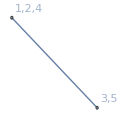
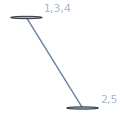
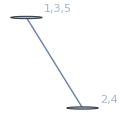
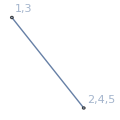
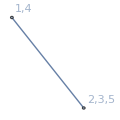
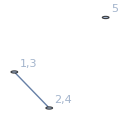
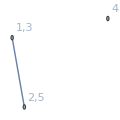
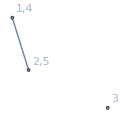
{-Graphics-51478,-Graphics-38308,-Graphics-36898,-Graphics-36194,-Graphics-31984,-Graphics-35406,-Graphics-33834,-Graphics-24922,-Graphics-11680,-Graphics-448,-Graphics-36138,-Graphics-36030,-Graphics-35434,-Graphics-33916,-Graphics-31492,-Graphics-31444,-Graphics-25168,-Graphics-22318,-Graphics-11950,-Graphics-7738,-Graphics-51475,-Graphics-49210,-Graphics-38281,-Graphics-36817,-Graphics-36166,-Graphics-36112,-Graphics-36086,-Graphics-31954,-Graphics-31738,-Graphics-31714,-Graphics-30334,-Graphics-29797,-Graphics-29633,-Graphics-29608,-Graphics-29560,-Graphics-49207,-Graphics-30253,-Graphics-29767,-Graphics-29533,-Graphics-29525,-Graphics-29514,-Graphics-29272,-Graphics-28794,-Graphics-9598,-Graphics-9112,-Graphics-29523,-Graphics-29515,-Graphics-29281,-Graphics-28795,-Graphics-9841,-Graphics-29524}

```mathematica
Table[WWPrint[key],{key,Sort[stubborn,With[{g=newAssoc[#1]["graph"],h=newAssoc[#2]["graph"]},If[VertexCount[g]==VertexCount[h],EdgeCount[g]<EdgeCount[h],VertexCount[g]<VertexCount[h]]]&]}]
```

```mathematica
eqs=Table[newAssoc[k[[1]]]["colofour2"]==k[[2]],{k,{
{49207,k1},{30253,k2},{29767,k3},{29533,k4},{29525,k5},
{51478,a1},{38308,a2},{36898,a3},{36194,a4},{31984,a5},
{51475,c1},{36817,c2},{29797,c3},{29633,c4},{38281,c5},
{49210,d1},{36086,d2},{31954,d3},{30334,d4},{29560,d4}
}}]
```

{1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)==k1,1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α1-10 β+2 β1+4 γ+2 γ1-10 δ+4 δ1+4 ϵ1)==k2,1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-10 α+2 α1+4 β+2 β1-10 γ+4 γ1+4 δ1+2 ϵ1)==k3,1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+4 α1+2 β1-10 γ+2 γ1+4 δ+2 δ1-10 ϵ+4 ϵ1)==k4,1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α+2 α1-10 β+4 β1+4 γ1+2 δ1-10 ϵ+2 ϵ1)==k5,1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)==a1,1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)==a2,1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)==a3,1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)==a4,1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)==a5,1/6 (-2 b01-2 b02+b03+4 b04+b05-b06-b07-b08+2 b09-b10-3 b11-3 b12+3 b13-3 b14+3 b15+4 b16+4 b17-2 b18-2 b19-2 b20-b21-b22-b23+5 b24-b25+b26+b27+b28-2 b29+b30+3 b36+3 b37-3 b38-3 b39-3 b40+8 α-4 α1-4 β-4 β1-4 γ+2 γ1+8 δ+2 δ1-4 ϵ+2 ϵ1)==c1,1/6 (b01-2 b02-2 b03+b04+4 b05-b06-b07-b08-b09+2 b10+3 b11-3 b12-3 b13+3 b14-3 b15-2 b16+4 b17+4 b18-2 b19-2 b20-b21-b22-b23-b24+5 b25+b26+b27+b28+b29-2 b30-3 b36+3 b37+3 b38-3 b39-3 b40-4 α+2 α1+8 β+2 β1-4 γ+2 γ1+8 δ-4 δ1-4 ϵ-4 ϵ1)==c2,1/6 (-2 b01+b02+4 b03+b04-2 b05-b06-b07+2 b08-b09-b10-3 b11+3 b12-3 b13+3 b14-3 b15+4 b16-2 b17-2 b18-2 b19+4 b20-b21-b22+5 b23-b24-b25+b26+b27-2 b28+b29+b30+3 b36-3 b37-3 b38-3 b39+3 b40+8 α+2 α1-4 β+2 β1+8 γ-4 γ1-4 δ-4 δ1-4 ϵ+2 ϵ1)==c3,1/6 (4 b01+b02-2 b03-2 b04+b05+2 b06-b07-b08-b09-b10-3 b11+3 b12-3 b13-3 b14+3 b15-2 b16-2 b17+4 b18+4 b19-2 b20+5 b21-b22-b23-b24-b25-2 b26+b27+b28+b29+b30-3 b36-3 b37+3 b38+3 b39-3 b40-4 α+2 α1+8 β-4 β1-4 γ-4 γ1-4 δ+2 δ1+8 ϵ+2 ϵ1)==c4,1/6 (b01+4 b02+b03-2 b04-2 b05-b06+2 b07-b08-b09-b10+3 b11-3 b12+3 b13-3 b14-3 b15-2 b16-2 b17-2 b18+4 b19+4 b20-b21+5 b22-b23-b24-b25+b26-2 b27+b28+b29+b30-3 b36-3 b37-3 b38+3 b39+3 b40-4 α-4 α1-4 β+2 β1+8 γ+2 γ1-4 δ+2 δ1+8 ϵ-4 ϵ1)==c5,1/2 (-b01-b02+b04+b09-b11-b12+b13-b14+b15+2 b16+2 b17-b21-b22-b23+b24-b25+b26+b27-b29-b34+b36+b37-b38-b39-b40+4 α-2 α1-2 β1+4 δ-2 ϵ)==d1,1/2 (b01-b03-b04+b06-b11+b12-b13-b14+b15+2 b18+2 b19+b21-b22-b23-b24-b25-b26+b28+b29-b31-b36-b37+b38+b39-b40-2 α+4 β-2 β1-2 γ1+4 ϵ)==d2,1/2 (-b01+b03-b05+b08-b11+b12-b13+b14-b15+2 b16+2 b20-b21-b22+b23-b24-b25+b26-b28+b30-b33+b36-b37-b38-b39+b40+4 α-2 β+4 γ-2 γ1-2 δ1)==d3,1/2 (-b02-b03+b05+b10+b11-b12-b13+b14-b15+2 b17+2 b18-b21-b22-b23-b24+b25+b27+b28-b30-b35-b36+b37+b38-b39-b40+4 β-2 γ+4 δ-2 δ1-2 ϵ1)==d4,1/2 (b02-b04-b05+b07+b11-b12+b13-b14-b15+2 b19+2 b20-b21+b22-b23-b24-b25-b27+b29+b30-b32-b36-b37-b38+b39+b40-2 α1+4 γ-2 δ+4 ϵ-2 ϵ1)==d4}

```mathematica
eqrep=With[{k=Map[#[[1]]->#[[2]]&,Reduce[eqs,{b01,b02,b03,b04,b05, b16,b17,b18,b19,b20,  b25,b26,b27,b28,b29,b36,b37,b37,b38,b39,b40}]]},Table[k[[i]],{i,Length[k]}]]
```

{b01→-(4 a1)/3+(8 a2)/3+(8 a3)/3-(16 a4)/3-(4 a5)/3-b06+b07+b10+(10 b11)/3-(8 b12)/3+(4 b13)/3+(4 b14)/3-(8 b15)/3-b30/3+(4 b31)/3-(4 b32)/3+(2 b33)/3+b34/3-(4 b35)/3-(4 c1)/3+4 c2-2 c3-(16 c4)/3+4 c5+(2 d1)/3+(8 d2)/3+(4 d3)/3-(16 d4)/3+(8 α)/3-(4 α1)/3+(4 β)/3+(8 β1)/3-(8 γ)/3+(8 γ1)/3-(8 δ)/3-(4 δ1)/3+(2 ϵ)/3-(10 ϵ1)/3,b02→-(4 a1)/3-(16 a2)/3-(4 a3)/3+(8 a4)/3+(8 a5)/3+b06-b07+b08-(8 b11)/3+(10 b12)/3-(8 b13)/3+(4 b14)/3+(4 b15)/3-b30/3-(5 b31)/3+(5 b32)/3-(4 b33)/3+b34/3+(2 b35)/3-(4 c1)/3-2 c2+4 c3+(14 c4)/3-6 c5+(2 d1)/3-(10 d2)/3-(8 d3)/3+(14 d4)/3-(10 α)/3+(8 α1)/3-(8 β)/3-(4 β1)/3+(4 γ)/3-(10 γ1)/3+(10 δ)/3-(4 δ1)/3+(2 ϵ)/3+(8 ϵ1)/3,b03→(8 a1)/3+(8 a2)/3-(4 a3)/3-(4 a4)/3-(16 a5)/3+b07-b08+b09+(4 b11)/3-(8 b12)/3+(10 b13)/3-(8 b14)/3+(4 b15)/3-b30/3+b31/3-(4 b32)/3+(5 b33)/3-(5 b34)/3+(2 b35)/3+(14 c1)/3-2 c2-6 c3-(4 c4)/3+4 c5-(10 d1)/3+(2 d2)/3+(10 d3)/3-(4 d4)/3+(2 α)/3-(10 α1)/3+(10 β)/3-(4 β1)/3+(4 γ)/3+(8 γ1)/3-(8 δ)/3+(8 δ1)/3-(10 ϵ)/3-(4 ϵ1)/3,b04→-(16 a1)/3-(4 a2)/3+(8 a3)/3-(4 a4)/3+(8 a5)/3+b08-b09+b10+(4 b11)/3+(4 b12)/3-(8 b13)/3+(10 b14)/3-(8 b15)/3-b30/3+b31/3+(2 b32)/3-(4 b33)/3+(4 b34)/3-(4 b35)/3-(16 c1)/3+4 c2+4 c3-(4 c4)/3-2 c5+(8 d1)/3+(2 d2)/3-(8 d3)/3-(4 d4)/3+(2 α)/3+(8 α1)/3-(8 β)/3+(8 β1)/3-(8 γ)/3-(4 γ1)/3+(4 δ)/3-(10 δ1)/3+(8 ϵ)/3-(4 ϵ1)/3,b05→(8 a1)/3-(4 a2)/3-(16 a3)/3+(8 a4)/3-(4 a5)/3+b06+b09-b10-(8 b11)/3+(4 b12)/3+(4 b13)/3-(8 b14)/3+(10 b15)/3-b30/3-(5 b31)/3+(2 b32)/3+(2 b33)/3-(5 b34)/3+(5 b35)/3+(14 c1)/3-6 c2-2 c3+(14 c4)/3-2 c5-(10 d1)/3-(10 d2)/3+(4 d3)/3+(14 d4)/3-(10 α)/3-(4 α1)/3+(4 β)/3-(10 β1)/3+(10 γ)/3-(4 γ1)/3+(4 δ)/3+(8 δ1)/3-(10 ϵ)/3+(8 ϵ1)/3,b16→2 a1+2 a5+b11-b21+2 c1+2 c3+2 d1+2 d3+k1+k3-α1+2 β-β1+γ-γ1+δ-δ1+2 ϵ-2 ϵ1,b17→2 a1+2 a3+b12-b22+2 c1+2 c2+2 d1+2 d4+k1+k2+α-α1+β-β1+2 γ-2 γ1-δ1+2 ϵ-ϵ1,b18→2 a3+2 a4+b13-b23+2 c2+2 c4+2 d2+2 d4+k2+k5+2 α-2 α1-β1+2 γ-γ1+δ-δ1+ϵ-ϵ1,b19→2 a2+2 a4+b14-b24+2 c4+2 c5+2 d2+2 d4+k4+k5+2 α-α1+β-β1+γ-γ1+2 δ-2 δ1-ϵ1,b20→-(8 a1)/3-(2 a2)/3-(8 a3)/3-(8 a4)/3-(2 a5)/3-b11/3-b12/3-b13/3-b14/3+(2 b15)/3+b21+b22+b23+b24-(2 b30)/3-b31/3+b32/3+b33/3-b34/3+b35/3-(5 c1)/3-3 c2-c3-(5 c4)/3-c5-(8 d1)/3-(8 d2)/3+(2 d3)/3-(2 d4)/3-k1-k2-k5-(11 α)/3+(7 α1)/3-(4 β)/3+(4 β1)/3-(10 γ)/3+(7 γ1)/3-(4 δ)/3+(7 δ1)/3-(11 ϵ)/3+(7 ϵ1)/3,b25→(8 a1)/3+(8 a2)/3+(8 a3)/3+(8 a4)/3+(8 a5)/3+b11/3+b12/3+b13/3+b14/3+b15/3-b21-b22-b23-b24+(2 b30)/3+b31/3-b32/3-b33/3+b34/3-b35/3+(5 c1)/3+3 c2+3 c3+(5 c4)/3+3 c5+(8 d1)/3+(8 d2)/3+(4 d3)/3+(8 d4)/3+k1+k2+k3+k4+k5+(14 α)/3-(10 α1)/3+(10 β)/3-(10 β1)/3+(10 γ)/3-(10 γ1)/3+(10 δ)/3-(10 δ1)/3+(14 ϵ)/3-(10 ϵ1)/3,b26→b30+b31-b32+b34-b35-2 c1+2 c2-2 c4+2 c5+2 d1+2 d2-4 d4+2 α-2 γ-2 δ+2 ϵ,b27→b30-b33+b34-2 c1+2 c3+2 d1-2 d3-2 β+2 ϵ,b28→b30+b31-b32-2 c4+2 c5+2 d2-2 d4+2 α-2 δ,b29→b30+b31-b33+b34-b35-2 c1+2 c2+2 c3-2 c4+2 d1+2 d2-2 d3-2 d4+2 α-2 β-2 γ+2 ϵ,b36→(2 a1)/3+(2 a2)/3+(2 a3)/3+(8 a4)/3+(2 a5)/3-(2 b11)/3+b12/3+b13/3+b14/3+b15/3-b23-b24+(2 b30)/3+b31/3-b32/3-b33/3+b34/3-b35/3-c1/3+c2+c3+(5 c4)/3+c5+(2 d1)/3+(8 d2)/3-(2 d3)/3+(8 d4)/3+k2+k4+k5+(8 α)/3-(7 α1)/3+(4 β)/3-(7 β1)/3+(7 γ)/3-(7 γ1)/3+(7 δ)/3-(7 δ1)/3+(8 ϵ)/3-(4 ϵ1)/3,b37→-2 a1-2 a3-2 a4-2 a5-b12+b21+b22+b23-2 c1-2 c2-2 c3-2 c4-2 d1-2 d4-k1-k2-α+α1-β+β1-2 γ+2 γ1-2 δ+δ1-2 ϵ+ϵ1,b38→-2 a1-2 a2-2 a3-2 a4-b13+b22+b23+b24-2 c1-2 c2-2 c4-2 c5-2 d2-2 d4-k2-k5-2 α+2 α1-2 β+β1-2 γ+γ1-δ+δ1-ϵ+ϵ1,b39→(8 a1)/3+(2 a2)/3+(2 a3)/3+(2 a4)/3+(2 a5)/3+b11/3+b12/3+b13/3-(2 b14)/3+b15/3-b21-b22+(2 b30)/3+b31/3-b32/3-b33/3+b34/3-b35/3+(5 c1)/3+c2+c3-c4/3+c5+(8 d1)/3+(2 d2)/3+(4 d3)/3+(2 d4)/3+k1+k2+k3+(8 α)/3-(7 α1)/3+(7 β)/3-(7 β1)/3+(7 γ)/3-(7 γ1)/3+(4 δ)/3-(4 δ1)/3+(8 ϵ)/3-(7 ϵ1)/3,b40→(2 a1)/3+(2 a2)/3+(8 a3)/3+(2 a4)/3+(2 a5)/3+b11/3+b12/3+b13/3+b14/3-(2 b15)/3-b22-b23+(2 b30)/3+b31/3-b32/3-b33/3+b34/3-b35/3-c1/3+3 c2+c3-c4/3+c5+(8 d1)/3+(8 d2)/3-(2 d3)/3+(2 d4)/3+k1+k2+k5+(11 α)/3-(7 α1)/3+(4 β)/3-(4 β1)/3+(4 γ)/3-(7 γ1)/3+(4 δ)/3-(7 δ1)/3+(11 ϵ)/3-(7 ϵ1)/3}

```mathematica
newAssoc[29523]["colofour2"]/.eqrep//Simplify
```

k1

```mathematica
Table[key->newAssoc[key]["colofour2"]/.eqrep//Simplify,{key,Sort[stubborn,With[{g=newAssoc[#1]["graph"],h=newAssoc[#2]["graph"]},If[VertexCount[g]==VertexCount[h],EdgeCount[g]<EdgeCount[h],VertexCount[g]<VertexCount[h]]]&]}]//TableForm
```

51478→a1
38308→a2
36898→a3
36194→a4
31984→a5
35406→a3+a4+α1
33834→a2+a4+δ1
24922→a2+a5+β1
11680→a1+a5+ϵ1
448→a1+a3+γ1
36138→a4+α1
36030→a4+δ1
35434→a3+α1
33916→a2+δ1
31492→a5+β1
31444→a5+ϵ1
25168→a2+β1
22318→a3+γ1
11950→a1+ϵ1
7738→a1+γ1
51475→c1
49210→d1
38281→c5
36817→c2
36166→α1
36112→δ1
36086→d2
31954→d3
31738→β1
31714→ϵ1
30334→d4
29797→c3
29633→c4
29608→γ1
29560→d4
49207→k1
30253→k2
29767→k3
29533→k4
29525→k5
29514→k4+k5
29272→k3+k4
28794→k2+k5
9598→k1+k3
9112→k1+k2
29523→k5
29515→k4
29281→k3
28795→k2
9841→k1
29524→0

```mathematica
Table[newAssoc[key]["colofour3"]=(newAssoc[key]["colofour2"]/.eqrep//Simplify);,{key,Keys[newAssoc]}];
```

```mathematica
Monitor[Table[newAssoc[key]["colortable4"]=(newAssoc[key]["colortable3"]/.eqrep//Simplify);,{key,Keys[newAssoc]}],key];
```

```mathematica
newAssoc[35406]
```

<|signature→35406,matrix→{{2,1,2,1,0},{1,2,1,2,0},{2,1,2,1,0},{1,2,1,2,0},{0,0,0,0,2}},graph→-Graphics-,vertexsets→{{5},{1,3},{2,4}},vertices→{1,2,3},edges→{{2,3}},relations→{x35406==x36138+x36898,x35406==x35434+x36194,x35406==x13284-x57528},links→{36898,36138,36194,35434},colofour→-(2 b01)/3+b03/3-(2 b05)/3+b07/3+b08/3+b09/3+(5 b13)/6-b18/6-b23/6-b27/6-b29/6-b31/6-b35/6+b48/6,colortable→{{x2187y1z2/3-x2430y1z2/6+x243y1z2/3-x333y1z2/6-(2 x6561y1z2)/3+(5 x6642y1z2)/6-(2 x81y1z2)/3-x8757y1z2/6+x9y1z2/3,b09/3-b23/6-b29/6-b31/6+b48/6+(b03-x2187y1z2)/3+1/6 (-b18+x2430y1z2)+(b08-x243y1z2)/3+1/6 (-b35+x333y1z2)-(2 (b01-x6561y1z2))/3+(5 (b13-x6642y1z2))/6-(2 (b05-x81y1z2))/3+1/6 (-b27+x8757y1z2)+(b07-x9y1z2)/3},{x19683y1z3/3-x19692y1z3/6+x2187y1z3/3-x21951y1z3/6-x2430y1z3/6+x243y1z3/3-x333y1z3/6-(2 x81y1z3)/3+x9y1z3/3,-(2 b01)/3+(5 b13)/6-b27/6-b31/6+b48/6+(b09-x19683y1z3)/3+1/6 (-b23+x19692y1z3)+(b03-x2187y1z3)/3+1/6 (-b29+x21951y1z3)+1/6 (-b18+x2430y1z3)+(b08-x243y1z3)/3+1/6 (-b35+x333y1z3)-(2 (b05-x81y1z3))/3+(b07-x9y1z3)/3},{x19683y1z4/3-x19692y1z4/6+x243y1z4/3-x26487y1z4/6-x333y1z4/6-(2 x6561y1z4)/3+(5 x6642y1z4)/6-(2 x81y1z4)/3+x9y1z4/3,b03/3-b18/6-b27/6-b29/6+b48/6+(b09-x19683y1z4)/3+1/6 (-b23+x19692y1z4)+(b08-x243y1z4)/3+1/6 (-b31+x26487y1z4)+1/6 (-b35+x333y1z4)-(2 (b01-x6561y1z4))/3+(5 (b13-x6642y1z4))/6-(2 (b05-x81y1z4))/3+(b07-x9y1z4)/3},{x19683y1z5/3-x19692y1z5/6+x2187y1z5/3-x21951y1z5/6-x2430y1z5/6+x243y1z5/3-x26487y1z5/6+x28764y1z5/6-x333y1z5/6-(2 x6561y1z5)/3+(5 x6642y1z5)/6-(2 x81y1z5)/3-x8757y1z5/6+x9y1z5/3,(b09-x19683y1z5)/3+1/6 (-b23+x19692y1z5)+(b03-x2187y1z5)/3+1/6 (-b29+x21951y1z5)+1/6 (-b18+x2430y1z5)+(b08-x243y1z5)/3+1/6 (-b31+x26487y1z5)+(b48-x28764y1z5)/6+1/6 (-b35+x333y1z5)-(2 (b01-x6561y1z5))/3+(5 (b13-x6642y1z5))/6-(2 (b05-x81y1z5))/3+1/6 (-b27+x8757y1z5)+(b07-x9y1z5)/3},{x19683y2z3/3-x19692y2z3/6+x2187y2z3/3-x21951y2z3/6-(2 x6561y2z3)/3+(5 x6642y2z3)/6-(2 x81y2z3)/3-x8757y2z3/6+x9y2z3/3,b08/3-b18/6-b31/6-b35/6+b48/6+(b09-x19683y2z3)/3+1/6 (-b23+x19692y2z3)+(b03-x2187y2z3)/3+1/6 (-b29+x21951y2z3)-(2 (b01-x6561y2z3))/3+(5 (b13-x6642y2z3))/6-(2 (b05-x81y2z3))/3+1/6 (-b27+x8757y2z3)+(b07-x9y2z3)/3},{x19683y2z4/3-x19692y2z4/6+x2187y2z4/3-x2430y2z4/6+x243y2z4/3-x26487y2z4/6-(2 x6561y2z4)/3-x8757y2z4/6+x9y2z4/3,-(2 b05)/3+(5 b13)/6-b29/6-b35/6+b48/6+(b09-x19683y2z4)/3+1/6 (-b23+x19692y2z4)+(b03-x2187y2z4)/3+1/6 (-b18+x2430y2z4)+(b08-x243y2z4)/3+1/6 (-b31+x26487y2z4)-(2 (b01-x6561y2z4))/3+1/6 (-b27+x8757y2z4)+(b07-x9y2z4)/3},{x19683y2z5/3-x19692y2z5/6+x2187y2z5/3-x21951y2z5/6-x2430y2z5/6+x243y2z5/3-x26487y2z5/6+x28764y2z5/6-x333y2z5/6-(2 x6561y2z5)/3+(5 x6642y2z5)/6-(2 x81y2z5)/3-x8757y2z5/6+x9y2z5/3,(b09-x19683y2z5)/3+1/6 (-b23+x19692y2z5)+(b03-x2187y2z5)/3+1/6 (-b29+x21951y2z5)+1/6 (-b18+x2430y2z5)+(b08-x243y2z5)/3+1/6 (-b31+x26487y2z5)+(b48-x28764y2z5)/6+1/6 (-b35+x333y2z5)-(2 (b01-x6561y2z5))/3+(5 (b13-x6642y2z5))/6-(2 (b05-x81y2z5))/3+1/6 (-b27+x8757y2z5)+(b07-x9y2z5)/3},{x19683y3z4/3+x2187y3z4/3-x21951y3z4/6-x2430y3z4/6+x243y3z4/3-x26487y3z4/6-(2 x6561y3z4)/3+(5 x6642y3z4)/6-(2 x81y3z4)/3,b07/3-b23/6-b27/6-b35/6+b48/6+(b09-x19683y3z4)/3+(b03-x2187y3z4)/3+1/6 (-b29+x21951y3z4)+1/6 (-b18+x2430y3z4)+(b08-x243y3z4)/3+1/6 (-b31+x26487y3z4)-(2 (b01-x6561y3z4))/3+(5 (b13-x6642y3z4))/6-(2 (b05-x81y3z4))/3},{x19683y3z5/3-x19692y3z5/6+x2187y3z5/3-x21951y3z5/6-x2430y3z5/6+x243y3z5/3-x26487y3z5/6+x28764y3z5/6-x333y3z5/6-(2 x6561y3z5)/3+(5 x6642y3z5)/6-(2 x81y3z5)/3-x8757y3z5/6+x9y3z5/3,(b09-x19683y3z5)/3+1/6 (-b23+x19692y3z5)+(b03-x2187y3z5)/3+1/6 (-b29+x21951y3z5)+1/6 (-b18+x2430y3z5)+(b08-x243y3z5)/3+1/6 (-b31+x26487y3z5)+(b48-x28764y3z5)/6+1/6 (-b35+x333y3z5)-(2 (b01-x6561y3z5))/3+(5 (b13-x6642y3z5))/6-(2 (b05-x81y3z5))/3+1/6 (-b27+x8757y3z5)+(b07-x9y3z5)/3},{x19683y4z5/3-x19692y4z5/6+x2187y4z5/3-x21951y4z5/6-x2430y4z5/6+x243y4z5/3-x26487y4z5/6+x28764y4z5/6-x333y4z5/6-(2 x6561y4z5)/3+(5 x6642y4z5)/6-(2 x81y4z5)/3-x8757y4z5/6+x9y4z5/3,(b09-x19683y4z5)/3+1/6 (-b23+x19692y4z5)+(b03-x2187y4z5)/3+1/6 (-b29+x21951y4z5)+1/6 (-b18+x2430y4z5)+(b08-x243y4z5)/3+1/6 (-b31+x26487y4z5)+(b48-x28764y4z5)/6+1/6 (-b35+x333y4z5)-(2 (b01-x6561y4z5))/3+(5 (b13-x6642y4z5))/6-(2 (b05-x81y4z5))/3+1/6 (-b27+x8757y4z5)+(b07-x9y4z5)/3}},colortable2→{{(b07-b23)/3+1/3 (-b03/2-b05/2+b09/2+b29/2)+1/3 (-b01/2-b08/2+b09/2+b31/2)-x333y1z2/6+(2 x6642y1z2)/3-x8757y1z2/6,b09/3+b23/6+1/3 (b03/2-b05/2+b09/2+b29/2)-2/3 (-b03/2+b05/2+b09/2+b29/2)-b29/6-2/3 (b01/2-b08/2+b09/2+b31/2)+1/3 (-b01/2+b08/2+b09/2+b31/2)-b31/6+b48/6+1/6 (-b35+x333y1z2)+(5 (b13-x6642y1z2))/6+1/6 (-b18+x6642y1z2)+1/6 (-b27+x8757y1z2)},{-2/3 (b05-b13)+2/3 (-b01/2+b03/2+b07/2-b27/2)+2/3 (-b01/2+b08/2+b09/2-b31/2)-x21951y1z3/6-x2430y1z3/3-x333y1z3/6,-(2 b01)/3+b13/6+1/3 (b01/2+b03/2-b07/2+b27/2)+1/3 (b01/2-b03/2+b07/2+b27/2)-b27/6+1/3 (b01/2+b08/2-b09/2+b31/2)+1/3 (b01/2-b08/2+b09/2+b31/2)-b31/6+b48/6+1/6 (-b29+x21951y1z3)+1/6 (-b18+x2430y1z3)+1/6 (-b23+x2430y1z3)+1/6 (-b35+x333y1z3)},{(b08-b18)/3+1/3 (-b01/2+b03/2-b07/2+b27/2)+1/3 (b03/2-b05/2-b09/2+b29/2)-x26487y1z4/6-x333y1z4/6+(2 x6642y1z4)/3,b03/3+b18/6-2/3 (b01/2+b03/2-b07/2+b27/2)+1/3 (-b01/2+b03/2+b07/2+b27/2)-b27/6-2/3 (b03/2+b05/2-b09/2+b29/2)+1/3 (b03/2-b05/2+b09/2+b29/2)-b29/6+b48/6+1/6 (-b31+x26487y1z4)+1/6 (-b35+x333y1z4)+(5 (b13-x6642y1z4))/6+1/6 (-b23+x6642y1z4)},{-2/3 (b05-b20)+(b07-b21)/3+(b08-b24)/3-2/3 (b01/2+b04/2-b10/2-b30/2)+1/3 (b02/2+b09/2-b10/2-b32/2)+1/3 (b03/2+b06/2-b10/2-b33/2)+1/6 (-b17/2+b21/2-b23/2+b37/2)+1/6 (-b18/2-b22/2+b24/2+b38/2)+1/6 (-b35+b40)+5/6 (b12/2+b13/2-b20/2-b45/2)-x21951y1z5/6-x26487y1z5/6+x28764y1z5/6-x8757y1z5/6,-(2 b20)/3+b21/3+b24/3-2/3 (b01/2-b04/2+b10/2+b30/2)+1/3 (-b02/2+b09/2+b10/2+b32/2)+1/3 (b03/2-b06/2+b10/2+b33/2)+1/6 (b17/2-b21/2-b23/2-b37/2)+1/6 (-b18/2+b22/2-b24/2-b38/2)-b40/6+5/6 (-b12/2+b13/2+b20/2+b45/2)+1/6 (-b29+x21951y1z5)+1/6 (-b31+x26487y1z5)+(b48-x28764y1z5)/6+1/6 (-b27+x8757y1z5)},{(b03-b18)/3+1/3 (-b01/2+b08/2-b09/2+b31/2)+1/3 (-b05/2-b07/2+b08/2+b35/2)-x21951y2z3/6+(2 x6642y2z3)/3-x8757y2z3/6,b08/3+b18/6-2/3 (b01/2+b08/2-b09/2+b31/2)+1/3 (-b01/2+b08/2+b09/2+b31/2)-b31/6-2/3 (b05/2-b07/2+b08/2+b35/2)+1/3 (-b05/2+b07/2+b08/2+b35/2)-b35/6+b48/6+1/6 (-b29+x21951y2z3)+(5 (b13-x6642y2z3))/6+1/6 (-b23+x6642y2z3)+1/6 (-b27+x8757y2z3)},{-2/3 (b01-b13)+2/3 (b03/2-b05/2+b09/2-b29/2)+2/3 (-b05/2+b07/2+b08/2-b35/2)-x2430y2z4/3-x26487y2z4/6-x8757y2z4/6,-(2 b05)/3+b13/6+1/3 (b03/2+b05/2-b09/2+b29/2)+1/3 (-b03/2+b05/2+b09/2+b29/2)-b29/6+1/3 (b05/2+b07/2-b08/2+b35/2)+1/3 (b05/2-b07/2+b08/2+b35/2)-b35/6+b48/6+1/6 (-b18+x2430y2z4)+1/6 (-b23+x2430y2z4)+1/6 (-b31+x26487y2z4)+1/6 (-b27+x8757y2z4)},{-2/3 (b01-b14)+(b03-b15)/3+(b07-b17)/3-2/3 (-b02/2+b05/2+b06/2-b26/2)+1/3 (-b02/2+b04/2+b08/2-b28/2)+1/3 (-b02/2+b09/2+b10/2-b32/2)+1/6 (b17/2-b21/2-b23/2+b37/2)+5/6 (b13/2-b14/2+b16/2-b41/2)+1/6 (-b27+b42)+1/6 (-b11/2+b15/2-b18/2+b43/2)-x21951y2z5/6-x26487y2z5/6+x28764y2z5/6-x333y2z5/6,-(2 b14)/3+b15/3+b17/3-2/3 (b02/2+b05/2-b06/2+b26/2)+1/3 (b02/2-b04/2+b08/2+b28/2)+1/3 (b02/2+b09/2-b10/2+b32/2)+1/6 (-b17/2+b21/2-b23/2-b37/2)+5/6 (b13/2+b14/2-b16/2+b41/2)-b42/6+1/6 (b11/2-b15/2-b18/2-b43/2)+1/6 (-b29+x21951y2z5)+1/6 (-b31+x26487y2z5)+(b48-x28764y2z5)/6+1/6 (-b35+x333y2z5)},{(b09-b23)/3+1/3 (-b01/2-b03/2+b07/2+b27/2)+1/3 (-b05/2+b07/2-b08/2+b35/2)-x21951y3z4/6-x26487y3z4/6+(2 x6642y3z4)/3,b07/3+b23/6-2/3 (b01/2-b03/2+b07/2+b27/2)+1/3 (-b01/2+b03/2+b07/2+b27/2)-b27/6-2/3 (b05/2+b07/2-b08/2+b35/2)+1/3 (-b05/2+b07/2+b08/2+b35/2)-b35/6+b48/6+1/6 (-b29+x21951y3z4)+1/6 (-b31+x26487y3z4)+(5 (b13-x6642y3z4))/6+1/6 (-b18+x6642y3z4)},{(b03-b11)/3-(2 (b05-b12))/3+(b09-b19)/3+1/3 (b02/2-b04/2+b08/2-b28/2)-2/3 (b01/2-b04/2+b10/2-b30/2)+1/3 (-b04/2+b06/2+b07/2-b34/2)+1/6 (b19/2-b23/2-b25/2+b39/2)+1/6 (b11/2-b15/2-b18/2+b43/2)+1/6 (-b29+b44)+5/6 (-b12/2+b13/2+b20/2-b45/2)-x26487y3z5/6+x28764y3z5/6-x333y3z5/6-x8757y3z5/6,b11/3-(2 b12)/3+b19/3+1/3 (-b02/2+b04/2+b08/2+b28/2)-2/3 (b01/2+b04/2-b10/2+b30/2)+1/3 (b04/2-b06/2+b07/2+b34/2)+1/6 (-b19/2-b23/2+b25/2-b39/2)+1/6 (-b11/2+b15/2-b18/2-b43/2)-b44/6+5/6 (b12/2+b13/2-b20/2+b45/2)+1/6 (-b31+x26487y3z5)+(b48-x28764y3z5)/6+1/6 (-b35+x333y3z5)+1/6 (-b27+x8757y3z5)},{-2/3 (b01-b16)+(b08-b22)/3+(b09-b25)/3-2/3 (b02/2+b05/2-b06/2-b26/2)+1/3 (b03/2-b06/2+b10/2-b33/2)+1/3 (b04/2-b06/2+b07/2-b34/2)+1/6 (-b31+b36)+1/6 (-b18/2+b22/2-b24/2+b38/2)+1/6 (-b19/2-b23/2+b25/2+b39/2)+5/6 (b13/2+b14/2-b16/2-b41/2)-x21951y4z5/6+x28764y4z5/6-x333y4z5/6-x8757y4z5/6,-(2 b16)/3+b22/3+b25/3-2/3 (-b02/2+b05/2+b06/2+b26/2)+1/3 (b03/2+b06/2-b10/2+b33/2)+1/3 (-b04/2+b06/2+b07/2+b34/2)-b36/6+1/6 (-b18/2-b22/2+b24/2-b38/2)+1/6 (b19/2-b23/2-b25/2-b39/2)+5/6 (b13/2-b14/2+b16/2+b41/2)+1/6 (-b29+x21951y4z5)+(b48-x28764y4z5)/6+1/6 (-b35+x333y4z5)+1/6 (-b27+x8757y4z5)}},comp→GreaterEqual,colortable3→{{0,1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1)},{1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1),0},{0,1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1)},{1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1),1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)},{0,1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1)},{1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1),0},{1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1),1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)},{0,1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1)},{1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1),1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)},{1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1),1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)}},colofour2→1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1),colofour3→a3+a4+α1,colortable4→{{0,a3+a4+α1},{a3+a4+α1,0},{0,a3+a4+α1},{a3,a4+α1},{0,a3+a4+α1},{a3+a4+α1,0},{a4,a3+α1},{0,a3+a4+α1},{a3,a4+α1},{a4,a3+α1}}|>

```mathematica
ColorTablePrint4[35406]
```

-Graphics-35406a3+a4+α1GreaterEqual
( | = | ≠
1<->2 | 0 | a3+a4+α1
1<->3 | a3+a4+α1 | 0
1<->4 | 0 | a3+a4+α1
1<->5 | a3 | a4+α1
2<->3 | 0 | a3+a4+α1
2<->4 | a3+a4+α1 | 0
2<->5 | a4 | a3+α1
3<->4 | 0 | a3+a4+α1
3<->5 | a3 | a4+α1
4<->5 | a4 | a3+α1)

```mathematica
Table[ColorTablePrint4[key],{key,Sort[stubborn,With[{g=newAssoc[#1]["graph"],h=newAssoc[#2]["graph"]},If[VertexCount[g]==VertexCount[h],EdgeCount[g]<EdgeCount[h],VertexCount[g]<VertexCount[h]]]&]}]
```

{-Graphics-51478a1GreaterEqual
( | = | ≠
1<->2 | a1 | 0
1<->3 | 0 | a1
1<->4 | a1 | 0
1<->5 | 0 | a1
2<->3 | 0 | a1
2<->4 | a1 | 0
2<->5 | 0 | a1
3<->4 | 0 | a1
3<->5 | a1 | 0
4<->5 | 0 | a1),-Graphics-38308a2GreaterEqual
( | = | ≠
1<->2 | 0 | a2
1<->3 | a2 | 0
1<->4 | a2 | 0
1<->5 | 0 | a2
2<->3 | 0 | a2
2<->4 | 0 | a2
2<->5 | a2 | 0
3<->4 | a2 | 0
3<->5 | 0 | a2
4<->5 | 0 | a2),-Graphics-36898a3GreaterEqual
( | = | ≠
1<->2 | 0 | a3
1<->3 | a3 | 0
1<->4 | 0 | a3
1<->5 | a3 | 0
2<->3 | 0 | a3
2<->4 | a3 | 0
2<->5 | 0 | a3
3<->4 | 0 | a3
3<->5 | a3 | 0
4<->5 | 0 | a3),-Graphics-36194a4GreaterEqual
( | = | ≠
1<->2 | 0 | a4
1<->3 | a4 | 0
1<->4 | 0 | a4
1<->5 | 0 | a4
2<->3 | 0 | a4
2<->4 | a4 | 0
2<->5 | a4 | 0
3<->4 | 0 | a4
3<->5 | 0 | a4
4<->5 | a4 | 0),-Graphics-31984a5GreaterEqual
( | = | ≠
1<->2 | 0 | a5
1<->3 | 0 | a5
1<->4 | a5 | 0
1<->5 | 0 | a5
2<->3 | a5 | 0
2<->4 | 0 | a5
2<->5 | a5 | 0
3<->4 | 0 | a5
3<->5 | a5 | 0
4<->5 | 0 | a5),-Graphics-35406a3+a4+α1GreaterEqual
( | = | ≠
1<->2 | 0 | a3+a4+α1
1<->3 | a3+a4+α1 | 0
1<->4 | 0 | a3+a4+α1
1<->5 | a3 | a4+α1
2<->3 | 0 | a3+a4+α1
2<->4 | a3+a4+α1 | 0
2<->5 | a4 | a3+α1
3<->4 | 0 | a3+a4+α1
3<->5 | a3 | a4+α1
4<->5 | a4 | a3+α1),-Graphics-33834a2+a4+δ1GreaterEqual
( | = | ≠
1<->2 | 0 | a2+a4+δ1
1<->3 | a2+a4+δ1 | 0
1<->4 | a2 | a4+δ1
1<->5 | 0 | a2+a4+δ1
2<->3 | 0 | a2+a4+δ1
2<->4 | a4 | a2+δ1
2<->5 | a2+a4+δ1 | 0
3<->4 | a2 | a4+δ1
3<->5 | 0 | a2+a4+δ1
4<->5 | a4 | a2+δ1),-Graphics-24922a2+a5+β1GreaterEqual
( | = | ≠
1<->2 | 0 | a2+a5+β1
1<->3 | a2 | a5+β1
1<->4 | a2+a5+β1 | 0
1<->5 | 0 | a2+a5+β1
2<->3 | a5 | a2+β1
2<->4 | 0 | a2+a5+β1
2<->5 | a2+a5+β1 | 0
3<->4 | a2 | a5+β1
3<->5 | a5 | a2+β1
4<->5 | 0 | a2+a5+β1),-Graphics-11680a1+a5+ϵ1GreaterEqual
( | = | ≠
1<->2 | a1 | a5+ϵ1
1<->3 | 0 | a1+a5+ϵ1
1<->4 | a1+a5+ϵ1 | 0
1<->5 | 0 | a1+a5+ϵ1
2<->3 | a5 | a1+ϵ1
2<->4 | a1 | a5+ϵ1
2<->5 | a5 | a1+ϵ1
3<->4 | 0 | a1+a5+ϵ1
3<->5 | a1+a5+ϵ1 | 0
4<->5 | 0 | a1+a5+ϵ1),-Graphics-448a1+a3+γ1GreaterEqual
( | = | ≠
1<->2 | a1 | a3+γ1
1<->3 | a3 | a1+γ1
1<->4 | a1 | a3+γ1
1<->5 | a3 | a1+γ1
2<->3 | 0 | a1+a3+γ1
2<->4 | a1+a3+γ1 | 0
2<->5 | 0 | a1+a3+γ1
3<->4 | 0 | a1+a3+γ1
3<->5 | a1+a3+γ1 | 0
4<->5 | 0 | a1+a3+γ1),-Graphics-36138a4+α1GreaterEqual
( | = | ≠
1<->2 | 0 | a4+α1
1<->3 | a4+α1 | 0
1<->4 | 0 | a4+α1
1<->5 | 0 | a4+α1
2<->3 | 0 | a4+α1
2<->4 | a4+α1 | 0
2<->5 | a4 | α1
3<->4 | 0 | a4+α1
3<->5 | 0 | a4+α1
4<->5 | a4 | α1),-Graphics-36030a4+δ1GreaterEqual
( | = | ≠
1<->2 | 0 | a4+δ1
1<->3 | a4+δ1 | 0
1<->4 | 0 | a4+δ1
1<->5 | 0 | a4+δ1
2<->3 | 0 | a4+δ1
2<->4 | a4 | δ1
2<->5 | a4+δ1 | 0
3<->4 | 0 | a4+δ1
3<->5 | 0 | a4+δ1
4<->5 | a4 | δ1),-Graphics-35434a3+α1GreaterEqual
( | = | ≠
1<->2 | 0 | a3+α1
1<->3 | a3+α1 | 0
1<->4 | 0 | a3+α1
1<->5 | a3 | α1
2<->3 | 0 | a3+α1
2<->4 | a3+α1 | 0
2<->5 | 0 | a3+α1
3<->4 | 0 | a3+α1
3<->5 | a3 | α1
4<->5 | 0 | a3+α1),-Graphics-33916a2+δ1GreaterEqual
( | = | ≠
1<->2 | 0 | a2+δ1
1<->3 | a2+δ1 | 0
1<->4 | a2 | δ1
1<->5 | 0 | a2+δ1
2<->3 | 0 | a2+δ1
2<->4 | 0 | a2+δ1
2<->5 | a2+δ1 | 0
3<->4 | a2 | δ1
3<->5 | 0 | a2+δ1
4<->5 | 0 | a2+δ1),-Graphics-31492a5+β1GreaterEqual
( | = | ≠
1<->2 | 0 | a5+β1
1<->3 | 0 | a5+β1
1<->4 | a5+β1 | 0
1<->5 | 0 | a5+β1
2<->3 | a5 | β1
2<->4 | 0 | a5+β1
2<->5 | a5+β1 | 0
3<->4 | 0 | a5+β1
3<->5 | a5 | β1
4<->5 | 0 | a5+β1),-Graphics-31444a5+ϵ1GreaterEqual
( | = | ≠
1<->2 | 0 | a5+ϵ1
1<->3 | 0 | a5+ϵ1
1<->4 | a5+ϵ1 | 0
1<->5 | 0 | a5+ϵ1
2<->3 | a5 | ϵ1
2<->4 | 0 | a5+ϵ1
2<->5 | a5 | ϵ1
3<->4 | 0 | a5+ϵ1
3<->5 | a5+ϵ1 | 0
4<->5 | 0 | a5+ϵ1),-Graphics-25168a2+β1GreaterEqual
( | = | ≠
1<->2 | 0 | a2+β1
1<->3 | a2 | β1
1<->4 | a2+β1 | 0
1<->5 | 0 | a2+β1
2<->3 | 0 | a2+β1
2<->4 | 0 | a2+β1
2<->5 | a2+β1 | 0
3<->4 | a2 | β1
3<->5 | 0 | a2+β1
4<->5 | 0 | a2+β1),-Graphics-22318a3+γ1GreaterEqual
( | = | ≠
1<->2 | 0 | a3+γ1
1<->3 | a3 | γ1
1<->4 | 0 | a3+γ1
1<->5 | a3 | γ1
2<->3 | 0 | a3+γ1
2<->4 | a3+γ1 | 0
2<->5 | 0 | a3+γ1
3<->4 | 0 | a3+γ1
3<->5 | a3+γ1 | 0
4<->5 | 0 | a3+γ1),-Graphics-11950a1+ϵ1GreaterEqual
( | = | ≠
1<->2 | a1 | ϵ1
1<->3 | 0 | a1+ϵ1
1<->4 | a1+ϵ1 | 0
1<->5 | 0 | a1+ϵ1
2<->3 | 0 | a1+ϵ1
2<->4 | a1 | ϵ1
2<->5 | 0 | a1+ϵ1
3<->4 | 0 | a1+ϵ1
3<->5 | a1+ϵ1 | 0
4<->5 | 0 | a1+ϵ1),-Graphics-7738a1+γ1GreaterEqual
( | = | ≠
1<->2 | a1 | γ1
1<->3 | 0 | a1+γ1
1<->4 | a1 | γ1
1<->5 | 0 | a1+γ1
2<->3 | 0 | a1+γ1
2<->4 | a1+γ1 | 0
2<->5 | 0 | a1+γ1
3<->4 | 0 | a1+γ1
3<->5 | a1+γ1 | 0
4<->5 | 0 | a1+γ1),-Graphics-51475c1GreaterEqual
( | = | ≠
1<->2 | c1 | 0
1<->3 | 0 | c1
1<->4 | c1 | 0
1<->5 | 0 | c1
2<->3 | 0 | c1
2<->4 | c1 | 0
2<->5 | 0 | c1
3<->4 | 0 | c1
3<->5 | 0 | c1
4<->5 | 0 | c1),-Graphics-49210d1GreaterEqual
( | = | ≠
1<->2 | d1 | 0
1<->3 | 0 | d1
1<->4 | 0 | d1
1<->5 | 0 | d1
2<->3 | 0 | d1
2<->4 | 0 | d1
2<->5 | 0 | d1
3<->4 | 0 | d1
3<->5 | d1 | 0
4<->5 | 0 | d1),-Graphics-38281c5GreaterEqual
( | = | ≠
1<->2 | 0 | c5
1<->3 | c5 | 0
1<->4 | c5 | 0
1<->5 | 0 | c5
2<->3 | 0 | c5
2<->4 | 0 | c5
2<->5 | 0 | c5
3<->4 | c5 | 0
3<->5 | 0 | c5
4<->5 | 0 | c5),-Graphics-36817c2GreaterEqual
( | = | ≠
1<->2 | 0 | c2
1<->3 | c2 | 0
1<->4 | 0 | c2
1<->5 | c2 | 0
2<->3 | 0 | c2
2<->4 | 0 | c2
2<->5 | 0 | c2
3<->4 | 0 | c2
3<->5 | c2 | 0
4<->5 | 0 | c2),-Graphics-36166α1GreaterEqual
( | = | ≠
1<->2 | 0 | α1
1<->3 | α1 | 0
1<->4 | 0 | α1
1<->5 | 0 | α1
2<->3 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->4 | 0 | α1
3<->5 | 0 | α1
4<->5 | 0 | α1),-Graphics-36112δ1GreaterEqual
( | = | ≠
1<->2 | 0 | δ1
1<->3 | δ1 | 0
1<->4 | 0 | δ1
1<->5 | 0 | δ1
2<->3 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->4 | 0 | δ1
3<->5 | 0 | δ1
4<->5 | 0 | δ1),-Graphics-36086d2GreaterEqual
( | = | ≠
1<->2 | 0 | d2
1<->3 | d2 | 0
1<->4 | 0 | d2
1<->5 | 0 | d2
2<->3 | 0 | d2
2<->4 | 0 | d2
2<->5 | 0 | d2
3<->4 | 0 | d2
3<->5 | 0 | d2
4<->5 | d2 | 0),-Graphics-31954d3GreaterEqual
( | = | ≠
1<->2 | 0 | d3
1<->3 | 0 | d3
1<->4 | d3 | 0
1<->5 | 0 | d3
2<->3 | d3 | 0
2<->4 | 0 | d3
2<->5 | 0 | d3
3<->4 | 0 | d3
3<->5 | 0 | d3
4<->5 | 0 | d3),-Graphics-31738β1GreaterEqual
( | = | ≠
1<->2 | 0 | β1
1<->3 | 0 | β1
1<->4 | β1 | 0
1<->5 | 0 | β1
2<->3 | 0 | β1
2<->4 | 0 | β1
2<->5 | β1 | 0
3<->4 | 0 | β1
3<->5 | 0 | β1
4<->5 | 0 | β1),-Graphics-31714ϵ1GreaterEqual
( | = | ≠
1<->2 | 0 | ϵ1
1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
1<->5 | 0 | ϵ1
2<->3 | 0 | ϵ1
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->4 | 0 | ϵ1
3<->5 | ϵ1 | 0
4<->5 | 0 | ϵ1),-Graphics-30334d4GreaterEqual
( | = | ≠
1<->2 | 0 | d4
1<->3 | 0 | d4
1<->4 | 0 | d4
1<->5 | d4 | 0
2<->3 | 0 | d4
2<->4 | d4 | 0
2<->5 | 0 | d4
3<->4 | 0 | d4
3<->5 | 0 | d4
4<->5 | 0 | d4),-Graphics-29797c3GreaterEqual
( | = | ≠
1<->2 | 0 | c3
1<->3 | 0 | c3
1<->4 | 0 | c3
1<->5 | 0 | c3
2<->3 | c3 | 0
2<->4 | 0 | c3
2<->5 | c3 | 0
3<->4 | 0 | c3
3<->5 | c3 | 0
4<->5 | 0 | c3),-Graphics-29633c4GreaterEqual
( | = | ≠
1<->2 | 0 | c4
1<->3 | 0 | c4
1<->4 | 0 | c4
1<->5 | 0 | c4
2<->3 | 0 | c4
2<->4 | c4 | 0
2<->5 | c4 | 0
3<->4 | 0 | c4
3<->5 | 0 | c4
4<->5 | c4 | 0),-Graphics-29608γ1GreaterEqual
( | = | ≠
1<->2 | 0 | γ1
1<->3 | 0 | γ1
1<->4 | 0 | γ1
1<->5 | 0 | γ1
2<->3 | 0 | γ1
2<->4 | γ1 | 0
2<->5 | 0 | γ1
3<->4 | 0 | γ1
3<->5 | γ1 | 0
4<->5 | 0 | γ1),-Graphics-29560d4GreaterEqual
( | = | ≠
1<->2 | 0 | d4
1<->3 | 0 | d4
1<->4 | 0 | d4
1<->5 | 0 | d4
2<->3 | 0 | d4
2<->4 | 0 | d4
2<->5 | d4 | 0
3<->4 | d4 | 0
3<->5 | 0 | d4
4<->5 | 0 | d4),-Graphics-49207k1GreaterEqual
( | = | ≠
1<->2 | k1 | 0
1<->3 | 0 | k1
1<->4 | 0 | k1
1<->5 | 0 | k1
2<->3 | 0 | k1
2<->4 | 0 | k1
2<->5 | 0 | k1
3<->4 | 0 | k1
3<->5 | 0 | k1
4<->5 | 0 | k1),-Graphics-30253k2GreaterEqual
( | = | ≠
1<->2 | 0 | k2
1<->3 | 0 | k2
1<->4 | 0 | k2
1<->5 | k2 | 0
2<->3 | 0 | k2
2<->4 | 0 | k2
2<->5 | 0 | k2
3<->4 | 0 | k2
3<->5 | 0 | k2
4<->5 | 0 | k2),-Graphics-29767k3GreaterEqual
( | = | ≠
1<->2 | 0 | k3
1<->3 | 0 | k3
1<->4 | 0 | k3
1<->5 | 0 | k3
2<->3 | k3 | 0
2<->4 | 0 | k3
2<->5 | 0 | k3
3<->4 | 0 | k3
3<->5 | 0 | k3
4<->5 | 0 | k3),-Graphics-29533k4GreaterEqual
( | = | ≠
1<->2 | 0 | k4
1<->3 | 0 | k4
1<->4 | 0 | k4
1<->5 | 0 | k4
2<->3 | 0 | k4
2<->4 | 0 | k4
2<->5 | 0 | k4
3<->4 | k4 | 0
3<->5 | 0 | k4
4<->5 | 0 | k4),-Graphics-29525k5GreaterEqual
( | = | ≠
1<->2 | 0 | k5
1<->3 | 0 | k5
1<->4 | 0 | k5
1<->5 | 0 | k5
2<->3 | 0 | k5
2<->4 | 0 | k5
2<->5 | 0 | k5
3<->4 | 0 | k5
3<->5 | 0 | k5
4<->5 | k5 | 0),-Graphics-29514k4+k5GreaterEqual
( | = | ≠
1<->2 | 0 | k4+k5
1<->3 | 0 | k4+k5
1<->4 | 0 | k4+k5
1<->5 | 0 | k4+k5
2<->3 | 0 | k4+k5
2<->4 | 0 | k4+k5
2<->5 | 0 | k4+k5
3<->4 | k4 | k5
3<->5 | 0 | k4+k5
4<->5 | k5 | k4),-Graphics-29272k3+k4GreaterEqual
( | = | ≠
1<->2 | 0 | k3+k4
1<->3 | 0 | k3+k4
1<->4 | 0 | k3+k4
1<->5 | 0 | k3+k4
2<->3 | k3 | k4
2<->4 | 0 | k3+k4
2<->5 | 0 | k3+k4
3<->4 | k4 | k3
3<->5 | 0 | k3+k4
4<->5 | 0 | k3+k4),-Graphics-28794k2+k5GreaterEqual
( | = | ≠
1<->2 | 0 | k2+k5
1<->3 | 0 | k2+k5
1<->4 | 0 | k2+k5
1<->5 | k2 | k5
2<->3 | 0 | k2+k5
2<->4 | 0 | k2+k5
2<->5 | 0 | k2+k5
3<->4 | 0 | k2+k5
3<->5 | 0 | k2+k5
4<->5 | k5 | k2),-Graphics-9598k1+k3GreaterEqual
( | = | ≠
1<->2 | k1 | k3
1<->3 | 0 | k1+k3
1<->4 | 0 | k1+k3
1<->5 | 0 | k1+k3
2<->3 | k3 | k1
2<->4 | 0 | k1+k3
2<->5 | 0 | k1+k3
3<->4 | 0 | k1+k3
3<->5 | 0 | k1+k3
4<->5 | 0 | k1+k3),-Graphics-9112k1+k2GreaterEqual
( | = | ≠
1<->2 | k1 | k2
1<->3 | 0 | k1+k2
1<->4 | 0 | k1+k2
1<->5 | k2 | k1
2<->3 | 0 | k1+k2
2<->4 | 0 | k1+k2
2<->5 | 0 | k1+k2
3<->4 | 0 | k1+k2
3<->5 | 0 | k1+k2
4<->5 | 0 | k1+k2),-Graphics-29523k5GreaterEqual
( | = | ≠
1<->2 | 0 | k5
1<->3 | 0 | k5
1<->4 | 0 | k5
1<->5 | 0 | k5
2<->3 | 0 | k5
2<->4 | 0 | k5
2<->5 | 0 | k5
3<->4 | 0 | k5
3<->5 | 0 | k5
4<->5 | k5 | 0),-Graphics-29515k4GreaterEqual
( | = | ≠
1<->2 | 0 | k4
1<->3 | 0 | k4
1<->4 | 0 | k4
1<->5 | 0 | k4
2<->3 | 0 | k4
2<->4 | 0 | k4
2<->5 | 0 | k4
3<->4 | k4 | 0
3<->5 | 0 | k4
4<->5 | 0 | k4),-Graphics-29281k3GreaterEqual
( | = | ≠
1<->2 | 0 | k3
1<->3 | 0 | k3
1<->4 | 0 | k3
1<->5 | 0 | k3
2<->3 | k3 | 0
2<->4 | 0 | k3
2<->5 | 0 | k3
3<->4 | 0 | k3
3<->5 | 0 | k3
4<->5 | 0 | k3),-Graphics-28795k2GreaterEqual
( | = | ≠
1<->2 | 0 | k2
1<->3 | 0 | k2
1<->4 | 0 | k2
1<->5 | k2 | 0
2<->3 | 0 | k2
2<->4 | 0 | k2
2<->5 | 0 | k2
3<->4 | 0 | k2
3<->5 | 0 | k2
4<->5 | 0 | k2),-Graphics-9841k1GreaterEqual
( | = | ≠
1<->2 | k1 | 0
1<->3 | 0 | k1
1<->4 | 0 | k1
1<->5 | 0 | k1
2<->3 | 0 | k1
2<->4 | 0 | k1
2<->5 | 0 | k1
3<->4 | 0 | k1
3<->5 | 0 | k1
4<->5 | 0 | k1),-Graphics-295240GreaterEqual
( | = | ≠
1<->2 | 0 | 0
1<->3 | 0 | 0
1<->4 | 0 | 0
1<->5 | 0 | 0
2<->3 | 0 | 0
2<->4 | 0 | 0
2<->5 | 0 | 0
3<->4 | 0 | 0
3<->5 | 0 | 0
4<->5 | 0 | 0)}

```mathematica
Table[ColorTablePrint4[key],{key,Take[Keys[newAssoc],-10]}]
```

{-Graphics-544921/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1)Greater
( | = | ≠
1<->2 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
1<->3 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
1<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
1<->5 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
2<->3 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
2<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
2<->5 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
3<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
3<->5 | 1/3 (8 a1+5 a2-4 a3+5 a4-4 a5-3 b08-3 b10-2 b11-2 b12+4 b13-5 b14+4 b15+2 b30+b31-b32+2 b33-2 b34+2 b35+8 c1-6 c2-6 c3+2 c4+6 c5-4 d1+2 d2+4 d3+2 d4+3 z+2 α-4 α1+4 β-4 β1+4 γ+2 γ1-2 δ+5 δ1-4 ϵ+2 ϵ1) | 0
4<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)),-Graphics-552511/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1)Greater
( | = | ≠
1<->2 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1) | 0
1<->3 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1) | 0
1<->4 | 0 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1)
1<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
2<->3 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1) | 0
2<->4 | 0 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1)
2<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
3<->4 | 0 | 1/2 (4 a1-6 a3+2 a4-4 a5+b06+b07-b08+b09-b10-2 b11+2 b13-4 b14+4 b15-b30-b31+2 b33-3 b34+2 b35+8 c1-8 c2-6 c3+4 c4-6 d1-4 d2+4 d3+4 d4-4 α-2 α1+4 β-4 β1+4 γ+4 δ1-6 ϵ+2 ϵ1)
3<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
4<->5 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)),-Graphics-552521/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)Greater
( | = | ≠
1<->2 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1) | 0
1<->3 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1) | 0
1<->4 | 0 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)
1<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
2<->3 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1) | 0
2<->4 | 0 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)
2<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
3<->4 | 0 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)
3<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
4<->5 | 0 | 1/6 (2 a1+8 a2-10 a3-4 a4-22 a5+3 b06+3 b07-3 b08+3 b09-3 b10-2 b11-8 b12+10 b13-8 b14+4 b15+6 b21-b30+b31-4 b32+8 b33-5 b34+2 b35+8 c1-12 c2-30 c3-4 c4+12 c5-22 d1+2 d2+4 d3-4 d4-6 k1-6 k3-4 α-4 α1+4 β+2 β1-2 γ+14 γ1-14 δ+14 δ1-22 ϵ+8 ϵ1)),-Graphics-560101/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)Greater
( | = | ≠
1<->2 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1) | 0
1<->3 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1) | 0
1<->4 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
1<->5 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
2<->3 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1) | 0
2<->4 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
2<->5 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
3<->4 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
3<->5 | 0 | 1/3 (a1-2 a2-2 a3+a4+a5-b11+2 b12-b13-b14+2 b15-2 b30-b31+b32+b33-b34+b35+4 c1-3 c2+4 c4-3 c5-2 d1-5 d2+2 d3+4 d4-5 α+α1+2 β-2 β1+2 γ-2 γ1+2 δ+δ1-2 ϵ+ϵ1)
4<->5 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)),-Graphics-560111/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)Greater
( | = | ≠
1<->2 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1) | 0
1<->3 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1) | 0
1<->4 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
1<->5 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
2<->3 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1) | 0
2<->4 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
2<->5 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
3<->4 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
3<->5 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)
4<->5 | 0 | 1/3 (-4 a1+2 a2+2 a3-4 a4-4 a5+b11-2 b12+b13+b14-2 b15+3 b21-b30+b31-b32+2 b33+b34-b35-4 c1+3 c2-6 c3-4 c4+3 c5-4 d1+2 d2-2 d3-4 d4-3 k1-3 k3-α+2 α1-2 β+5 β1-5 γ+5 γ1-5 δ+2 δ1-4 ϵ+2 ϵ1)),-Graphics-560121/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)Greater
( | = | ≠
1<->2 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 0
1<->3 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 0
1<->4 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
1<->5 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
2<->3 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 0
2<->4 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
2<->5 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
3<->4 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
3<->5 | 0 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1)
4<->5 | 1/3 (5 a1-4 a2-4 a3+5 a4+5 a5-2 b11+4 b12-2 b13-2 b14+4 b15-3 b21-b30-2 b31+2 b32-b33-2 b34+2 b35+8 c1-6 c2+6 c3+8 c4-6 c5+2 d1-7 d2+4 d3+8 d4+3 k1+3 k3-4 α-α1+4 β-7 β1+7 γ-7 γ1+7 δ-δ1+2 ϵ-ϵ1) | 0),-Graphics-567701/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)Greater
( | = | ≠
1<->2 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
1<->3 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
1<->4 | 0 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
1<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
2<->3 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
2<->4 | 0 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
2<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
3<->4 | 0 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)
3<->5 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1) | 0
4<->5 | 0 | 1/6 (10 a1+4 a2-14 a3+4 a4-14 a5+3 b06+3 b07-3 b08+3 b09-3 b10-4 b11-4 b12+8 b13-10 b14+8 b15+b30-b31-2 b32+4 b33-7 b34+4 b35+16 c1-18 c2-18 c3+4 c4+6 c5-14 d1-2 d2+8 d3+4 d4-2 α-8 α1+8 β-8 β1+8 γ+4 γ1-4 δ+10 δ1-14 ϵ+4 ϵ1)),-Graphics-575281/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1)Greater
( | = | ≠
1<->2 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
1<->3 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
1<->4 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
1<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
2<->3 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
2<->4 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
2<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
3<->4 | 1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1) | 0
3<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
4<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)),-Graphics-582881/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)Greater
( | = | ≠
1<->2 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
1<->3 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
1<->4 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
1<->5 | 0 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
2<->3 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
2<->4 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
2<->5 | 0 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
3<->4 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1) | 0
3<->5 | 0 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)
4<->5 | 0 | 1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)),-Graphics-59048a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵGreater
( | = | ≠
1<->2 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
1<->3 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
1<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
1<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
2<->3 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
2<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
2<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
3<->4 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
3<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0
4<->5 | a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ | 0)}

```mathematica
ineqsbis=Table[newAssoc[key]["comp"][newAssoc[key]["colofour3"],0],{key,Keys[newAssoc]}]
```

{z>0,b06>0,-b06+z>0,1/3 (-16 a1-4 a2+8 a3-4 a4+8 a5+3 b08-3 b09+3 b10+4 b11+4 b12-8 b13+10 b14-8 b15-b30+b31+2 b32-4 b33+4 b34-4 b35-16 c1+12 c2+12 c3-4 c4-6 c5+8 d1+2 d2-8 d3-4 d4+2 α+8 α1-8 β+8 β1-8 γ-4 γ1+4 δ-10 δ1+8 ϵ-4 ϵ1)>0,1888,1/3 (-4 a1-4 a2+5 a3+5 a4+8 a5-3 b07-3 b09-2 b11+4 b12-5 b13+4 b14-2 b15+2 b30+b31+2 b32-4 b33+4 b34-b35-10 c1+6 c2+12 c3+2 c4-6 c5+8 d1+2 d2-8 d3+2 d4+3 z+2 α+5 α1-8 β+2 β1-2 γ-4 γ1+4 δ-4 δ1+8 ϵ+2 ϵ1)>0,1/6 (-14 a1-14 a2+4 a3+4 a4+10 a5+3 b06-3 b07+3 b08-3 b09+3 b10-4 b11+8 b12-10 b13+8 b14-4 b15+b30-b31+4 b32-8 b33+5 b34-2 b35-20 c1+6 c2+18 c3+4 c4-18 c5+10 d1-2 d2-16 d3+4 d4-2 α+10 α1-16 β+4 β1-4 γ-8 γ1+8 δ-8 δ1+10 ϵ+4 ϵ1)>0,a1+a2+a3+a4+a5-b06/2-b07/2-b08/2-b09/2-b10/2+b30/2+b31/2+b34/2+c2+c3+c5+d1+d2+z+α+ϵ>0}
 |  |  |  |

```mathematica
ineqsbissimp=Simplify[Fold[And,ineqsbis]];
```

```mathematica
ExpressionToTable[ineqsbissimp]
```

a1≥0
a2≥0
a3≥0
a4≥0
a5≥0
b06>0
b07>0
b08>0
b09>0
b10>0
b11>0
b12>0
b13>0
b14>0
b15>0
b21>0
b22>0
b23>0
b24>0
b30>0
b31>0
b32>0
b33>0
b34>0
b35>0
c1≥0
c2≥0
c3≥0
c4≥0
c5≥0
d1≥0
d2≥0
d3≥0
d4≥0
k1≥0
k2≥0
k3≥0
k4≥0
k5≥0
z>0
α>0
α1≥0
β>0
β1≥0
γ>0
γ1≥0
δ>0
δ1≥0
ϵ>0
ϵ1≥0
a2+c5>0
a2+d4>0
a3+d4>0
b22<b06
b21<b07
b23<b07
b22<b08
b24<b08
b23<b09
b21<b10
b24<b10
a1+c1>0
a3+c2>0
a5+c3>0
a4+c4>0
c4+k5>0
a1+d1>0
a4+d2>0
d2+k5>0
a5+d3>0
c1+k1>0
d1+k1>0
c2+k2>0
d4+k2>0
c3+k3>0
d3+k3>0
c5+k4>0
d4+k4>0
b06<z
b07<z
b08<z
b09<z
b10<z
α1+δ1<α
β1+ϵ1<β
α1+γ1<γ
β1+δ1<δ
γ1+ϵ1<ϵ
b06+b08<b22+z
b07+b09<b23+z
b07+b10<b21+z
b08+b10<b24+z
c2+d2+α<b35+α1
c5+d2+α<b32+δ1
c1+d3+β<b30+ϵ1
c1+d3+β<b34+ϵ1
c5+d3+β<b32+β1
c1+d4+γ<b34+γ1
α1+γ1+δ1<α+γ
c4+d4+γ<b31+α1
α1+β1+δ1<α+δ
β1+δ1+ϵ1<β+δ
c3+d4+δ<b33+β1
c4+d4+δ<b30+δ1
c4+d4+δ<b31+δ1
c2+d1+ϵ<b35+γ1
c3+d1+ϵ<b33+ϵ1
β1+γ1+ϵ1<β+ϵ
α1+γ1+ϵ1<γ+ϵ
α1+β1+δ1+ϵ1<α+β
α1+β1+γ1+ϵ1<β+γ
α1+β1+γ1+δ1<γ+δ
α1+γ1+δ1+ϵ1<α+ϵ
β1+γ1+δ1+ϵ1<δ+ϵ
c4+2 d4+γ+δ<b31+α1+δ1
c5+d2+d3+α+β<b32+β1+δ1
c1+d3+d4+β+γ<b34+γ1+ϵ1
α1+β1+γ1+δ1+ϵ1<α+β+γ
α1+β1+γ1+δ1+ϵ1<β+γ+δ
c2+d1+d2+α+ϵ<b35+α1+γ1
α1+β1+γ1+δ1+ϵ1<α+β+ϵ
c3+d1+d4+δ+ϵ<b33+β1+ϵ1
α1+β1+γ1+δ1+ϵ1<α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<γ+δ+ϵ
b32+2 (c4+d4+δ)<b30+b31+2 (c5+d2+α)
a1+a2+a3+c1+c2+c5+α+β<b22
a1+a2+a4+c1+c5+d2+α+β<b24
a1+a2+a3+c1+c5+d4+β+γ<b22
a1+a2+a4+c1+c4+c5+β+γ<b24
a1+a4+a5+c1+c4+d3+β+γ<b21
a1+a2+a4+c1+c4+d4+γ+δ<b24
a1+a4+a5+c1+c3+c4+γ+δ<b21
a3+a4+a5+c3+c4+d4+γ+δ<b23
a1+a2+a3+c2+c5+d1+α+ϵ<b22
a3+a4+a5+c2+c3+d2+α+ϵ<b23
b33+2 (c1+d3+β)<b30+b34+2 (c3+d1+ϵ)
a3+a4+a5+c2+c3+c4+δ+ϵ<b23
a1+a4+a5+c3+c4+d1+δ+ϵ<b21
b32+2 (c4+d4+δ)<b30+b31+c5+d2+α+δ1
a3+a4+c2+c4+d2+d4+α+γ<b23+α1
a2+a4+c4+c5+d2+d4+α+δ<b24+δ1
c1+c4+d3+d4+β+δ<b30+β1+δ1+ϵ1
a1+a5+c1+c3+d1+d3+β+ϵ<b21+ϵ1
b33+2 (c1+d3+β)<b30+b34+c3+d1+ϵ+ϵ1
a1+a3+c1+c2+d1+d4+γ+ϵ<b22+γ1
a1+a2+a3+c1+c2+c5+d4+α+β+γ<b22+α1
a1+a2+a4+c1+c4+c5+d2+α+β+γ<b24+α1
b32+c1+2 c4+3 d4+γ+2 δ<b30+b31+2 c5+2 d2+2 α+γ1
a1+a2+a4+c1+c4+c5+d4+β+γ+δ<b24+β1
a1+a4+a5+c1+c3+c4+d3+β+γ+δ<b21+β1
a1+a2+a3+c1+c2+c5+d1+α+β+ϵ<b22+ϵ1
a3+a4+a5+c2+c3+c4+d2+α+δ+ϵ<b23+δ1
a1+a4+a5+c1+c3+c4+d1+γ+δ+ϵ<b21+γ1
a3+a4+a5+c2+c3+c4+d4+γ+δ+ϵ<b23+γ1
b33+2 c1+c4+2 d3+d4+2 β+γ<b30+b34+2 c3+2 d1+α1+2 ϵ
b32+c1+2 c4+3 d4+γ+2 δ<b30+b31+c5+d2+α+α1+γ1+δ1
a1+a2+a4+c1+c4+c5+d2+d4+α+β+δ<b24+β1+δ1
a1+a2+a4+c1+c4+c5+d2+d4+α+γ+δ<b24+α1+δ1
a3+a4+a5+c2+c3+c4+d2+d4+α+γ+δ<b23+α1+δ1
a1+a2+a3+c1+c2+c5+d1+d4+α+γ+ϵ<b22+α1+γ1
a3+a4+a5+c2+c3+c4+d2+d4+α+γ+ϵ<b23+α1+γ1
a1+a2+a3+c1+c2+c5+d1+d4+β+γ+ϵ<b22+γ1+ϵ1
a1+a4+a5+c1+c3+c4+d1+d3+β+γ+ϵ<b21+γ1+ϵ1
a1+a4+a5+c1+c3+c4+d1+d3+β+δ+ϵ<b21+β1+ϵ1
b33+2 c1+c4+2 d3+d4+2 β+γ<b30+b34+c3+d1+α1+γ1+ϵ+ϵ1
a1+a2+a4+c1+c4+c5+d2+d4+α+β+γ+δ<b24+α1+β1+δ1
b32+b35+2 (c1+c4+2 d4+γ+δ)<b30+b31+b34+2 c2+2 c5+2 d1+2 d2+2 α+2 ϵ
a1+a2+a3+c1+c2+c5+d1+d4+α+β+γ+ϵ<b22+α1+γ1+ϵ1
a3+a4+a5+c2+c3+c4+d2+d4+α+γ+δ+ϵ<b23+α1+γ1+δ1
a1+a4+a5+c1+c3+c4+d1+d3+β+γ+δ+ϵ<b21+β1+γ1+ϵ1
b32+b35+2 (c1+c4+2 d4+γ+δ)<b30+b31+b34+c2+2 c5+d1+2 d2+2 α+γ1+ϵ
b33+b35+2 (c1+c4+d3+d4+β+γ)<b30+b31+b34+2 c2+2 c3+2 d1+2 d2+2 α+2 ϵ
b33+b35+2 (c1+c4+d3+d4+β+γ)<b30+b31+b34+c2+2 c3+2 d1+d2+α+α1+2 ϵ
b24+α1+β1+γ1+2 δ1+ϵ1<a2+a4+b14+c4+2 c5+2 d2+d4+k4+k5+2 α+β+γ+δ
b23+2 α1+β1+γ1+δ1+ϵ1<a3+a4+b13+2 c2+c4+2 d2+d4+k2+k5+2 α+γ+δ+ϵ
b21+α1+β1+γ1+δ1+2 ϵ1<a1+a5+b11+2 c1+c3+d1+2 d3+k1+k3+2 β+γ+δ+ϵ
b22+α1+β1+2 γ1+δ1+ϵ1<a1+a3+b12+2 c1+c2+d1+2 d4+k1+k2+α+β+2 γ+ϵ
b23+2 α1+β1+γ1+δ1+ϵ1<a3+a4+b13+c2+2 c4+d2+2 d4+k2+k5+α+2 γ+δ+ϵ
b24+α1+β1+γ1+2 δ1+ϵ1<a2+a4+b14+2 c4+c5+d2+2 d4+k4+k5+α+β+γ+2 δ
b24+α1+β1+γ1+δ1+ϵ1<a2+a4+b14+c4+c5+d2+d4+k4+k5+α+β+γ+δ
b33+b35+2 c1+2 c4+2 d3+3 d4+2 β+2 γ+δ<b30+b31+b34+2 c2+c3+2 d1+2 d2+2 α+β1+2 ϵ
b32+b35+2 c1+2 c4+d3+4 d4+β+2 γ+2 δ<b30+b31+b34+2 c2+c5+2 d1+2 d2+2 α+β1+2 ϵ
b22+α1+β1+2 γ1+δ1+ϵ1<a1+a3+b12+c1+2 c2+2 d1+d4+k1+k2+α+β+γ+2 ϵ
b22+α1+β1+γ1+δ1+ϵ1<a1+a3+b12+c1+c2+d1+d4+k1+k2+α+β+γ+ϵ
b23+α1+β1+γ1+δ1+ϵ1<a3+a4+b13+c2+c4+d2+d4+k2+k5+α+γ+δ+ϵ
b21+α1+β1+γ1+δ1+2 ϵ1<a1+a5+b11+c1+2 c3+2 d1+d3+k1+k3+β+γ+δ+2 ϵ
b21+α1+β1+γ1+δ1+ϵ1<a1+a5+b11+c1+c3+d1+d3+k1+k3+β+γ+δ+ϵ
b32+b35+2 c1+2 c4+d3+4 d4+β+2 γ+2 δ<b30+b31+b34+c2+c5+d1+2 d2+2 α+β1+γ1+ϵ+ϵ1
b06+b07+b08+b09+b10<2 a1+2 a2+2 a3+2 a4+2 a5+b30+b31+b34+2 c2+2 c3+2 c5+2 d1+2 d2+2 z+2 α+2 ϵ
b33+b35+2 c1+2 c4+2 d3+3 d4+2 β+2 γ+δ<b30+b31+b34+c2+c3+2 d1+d2+α+α1+β1+δ1+2 ϵ
a1+2 a2+a4+b13+c1+c4+2 c5+2 d2+d4+k4+k5+2 α+β+γ+δ<a5+b12+b24+c3+2 α1+β1+δ1+ϵ1
2 a3+a4+a5+b14+2 c2+c3+c4+2 d2+d4+k2+k5+2 α+γ+δ+ϵ<a1+b15+b23+c1+α1+γ1+2 δ1+ϵ1
2 a1+a4+a5+b15+2 c1+c3+c4+d1+2 d3+k1+k3+2 β+γ+δ+ϵ<a3+b14+b21+c2+α1+2 β1+γ1+ϵ1
2 a1+a2+a3+b13+2 c1+c2+c5+d1+2 d4+k1+k2+α+β+2 γ+ϵ<a5+b14+b22+c3+2 α1+β1+γ1+ϵ1
a3+2 a4+a5+b12+c2+c3+2 c4+d2+2 d4+k2+k5+α+2 γ+δ+ϵ<a2+b11+b23+c5+α1+β1+2 γ1+δ1
a1+a2+2 a4+b15+c1+2 c4+c5+d2+2 d4+k4+k5+α+β+γ+2 δ<a3+b11+b24+c2+α1+2 β1+γ1+δ1
a1+a2+2 a3+b11+c1+2 c2+c5+2 d1+d4+k1+k2+α+β+γ+2 ϵ<a4+b15+b22+c4+α1+γ1+δ1+2 ϵ1
a1+a4+2 a5+b12+c1+2 c3+c4+2 d1+d3+k1+k3+β+γ+δ+2 ϵ<a2+b13+b21+c5+β1+2 γ1+δ1+ϵ1
b22+b23+2 α1+β1+γ1+δ1+ϵ1<a1+a2+2 a3+a4+b13+c1+2 c2+c4+c5+d2+2 d4+k2+k5+2 α+β+2 γ+δ+ϵ
a1+a2+2 a3+2 a4+b13+c1+2 c2+2 c4+c5+2 d2+2 d4+k2+k5+2 α+β+2 γ+δ+ϵ<b08+b23+2 α1+β1+γ1+δ1+ϵ1
b23+b24+2 α1+β1+γ1+δ1+ϵ1<a1+a2+a3+2 a4+b13+c1+c2+2 c4+c5+2 d2+d4+k2+k5+2 α+β+2 γ+δ+ϵ
2 a2+a3+2 a4+a5+b14+c2+c3+2 c4+2 c5+2 d2+2 d4+k4+k5+2 α+β+γ+2 δ+ϵ<b09+b24+α1+β1+γ1+2 δ1+ϵ1
b23+b24+α1+β1+γ1+2 δ1+ϵ1<a2+a3+2 a4+a5+b14+c2+c3+2 c4+c5+2 d2+d4+k4+k5+2 α+β+γ+2 δ+ϵ
b32+b33+b35+3 c1+3 c4+2 d3+4 d4+2 β+2 γ+2 δ<2 b30+b31+b34+c2+c3+c5+2 d1+2 d2+2 α+α1+β1+γ1+δ1+2 ϵ+ϵ1
2 a1+a2+a3+2 a5+b11+2 c1+c2+2 c3+c5+2 d1+2 d3+k1+k3+α+2 β+γ+δ+2 ϵ<b06+b21+α1+β1+γ1+δ1+2 ϵ1
b21+b22+α1+β1+γ1+δ1+2 ϵ1<2 a1+a2+a3+a5+b11+2 c1+c2+c3+c5+2 d1+d3+k1+k3+α+2 β+γ+δ+2 ϵ
2 a1+2 a3+a4+a5+b12+2 c1+2 c2+c3+c4+2 d1+2 d4+k1+k2+α+β+2 γ+δ+2 ϵ<b07+b22+α1+β1+2 γ1+δ1+ϵ1
b21+b22+α1+β1+2 γ1+δ1+ϵ1<2 a1+a3+a4+a5+b12+2 c1+c2+c3+c4+2 d1+d4+k1+k2+α+β+2 γ+δ+2 ϵ
b22+b23+α1+β1+2 γ1+δ1+ϵ1<a1+2 a3+a4+a5+b12+c1+2 c2+c3+c4+d1+2 d4+k1+k2+α+β+2 γ+δ+2 ϵ
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+2 d4+k2+k5+3 α+2 β+3 γ+δ+ϵ<b22+b23+b24+3 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+2 d4+k2+k5+2 α+2 β+3 γ+δ+ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+2 d4+k2+k5+3 α+2 β+2 γ+δ+ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+c5+2 d2+3 d4+k2+k5+2 α+β+3 γ+2 δ+ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+3 d4+k2+k5+3 α+β+3 γ+2 δ+ϵ<b22+b23+b24+3 α1+β1+γ1+2 δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+3 d4+k2+k5+2 α+2 β+3 γ+2 δ+ϵ<b22+b23+b24+2 α1+2 β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+3 d4+k2+k5+3 α+2 β+3 γ+2 δ+ϵ<b22+b23+b24+3 α1+2 β1+γ1+2 δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+2 d2+3 d4+k2+k5+3 α+2 β+2 γ+2 δ+ϵ<b22+b23+b24+2 α1+2 β1+γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+2 d4+k1+k2+α+β+3 γ+2 δ+3 ϵ<b21+b22+b23+α1+β1+3 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+2 d4+k1+k2+α+β+2 γ+2 δ+3 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+2 d4+k1+k2+α+β+3 γ+2 δ+2 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+c1+2 c2+2 c4+2 c5+d1+2 d2+2 d4+k2+k5+3 α+β+2 γ+δ+2 ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+2 d4+k2+k5+3 α+β+3 γ+δ+2 ϵ<b22+b23+b24+3 α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+2 d4+k1+k2+2 α+β+3 γ+δ+3 ϵ<b21+b22+b23+2 α1+β1+3 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+c4+2 d1+d2+2 d4+k1+k2+2 α+β+2 γ+δ+3 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+2 d4+k2+k5+3 α+2 β+2 γ+δ+2 ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+2 d4+k2+k5+3 α+2 β+3 γ+δ+2 ϵ<b22+b23+b24+3 α1+β1+2 γ1+δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+2 d4+k2+k5+2 α+2 β+3 γ+δ+2 ϵ<b22+b23+b24+2 α1+β1+2 γ1+δ1+2 ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+c3+2 c4+2 d1+d3+2 d4+k1+k2+α+2 β+3 γ+δ+2 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d3+2 d4+k1+k2+α+2 β+3 γ+δ+3 ϵ<b21+b22+b23+α1+β1+3 γ1+δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+c1+2 c2+2 c4+c5+d1+2 d2+3 d4+k2+k5+2 α+β+2 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+β1+γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k2+k5+3 α+β+2 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+β1+γ1+2 δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+c5+d1+2 d2+3 d4+k2+k5+2 α+β+3 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k2+k5+3 α+β+3 γ+2 δ+2 ϵ<b22+b23+b24+3 α1+β1+2 γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+2 d4+k1+k2+2 α+β+3 γ+2 δ+3 ϵ<b21+b22+b23+2 α1+β1+3 γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+2 d4+k1+k2+2 α+β+3 γ+2 δ+2 ϵ<b21+b22+b23+2 α1+β1+2 γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+2 d4+k1+k2+2 α+β+2 γ+2 δ+3 ϵ<b21+b22+b23+α1+β1+2 γ1+2 δ1+ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k2+k5+2 α+2 β+2 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+2 β1+γ1+δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k2+k5+2 α+2 β+3 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+2 β1+2 γ1+δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k2+k5+3 α+2 β+2 γ+2 δ+2 ϵ<b22+b23+b24+2 α1+2 β1+γ1+2 δ1+2 ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d3+2 d4+k1+k2+α+2 β+3 γ+2 δ+2 ϵ<b21+b22+b23+α1+2 β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d3+2 d4+k1+k2+α+2 β+3 γ+2 δ+3 ϵ<b21+b22+b23+α1+2 β1+3 γ1+δ1+2 ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d3+2 d4+k1+k2+α+2 β+2 γ+2 δ+3 ϵ<b21+b22+b23+α1+2 β1+2 γ1+δ1+2 ϵ1
b22+b23+b24+c3+2 α1+β1+γ1+δ1+ϵ1<2 a1+2 a2+2 a3+2 a4+b13+b33+2 c1+2 c2+2 c4+2 c5+2 d2+2 d4+k2+k5+2 α+2 β+2 γ+δ+ϵ
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+3 γ+δ+2 ϵ<b21+b22+b23+2 α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+c3+c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+2 γ+δ+2 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+3 γ+δ+3 ϵ<b21+b22+b23+2 α1+β1+3 γ1+δ1+2 ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+2 γ+δ+3 ϵ<b21+b22+b23+α1+β1+2 γ1+δ1+2 ϵ1
b21+b22+b23+c5+α1+β1+2 γ1+δ1+ϵ1<2 a1+2 a3+2 a4+2 a5+b12+b32+2 c1+2 c2+2 c3+2 c4+2 d1+2 d4+k1+k2+α+β+2 γ+2 δ+2 ϵ
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+3 γ+2 δ+2 ϵ<b21+b22+b23+2 α1+2 β1+2 γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+2 γ+2 δ+2 ϵ<b21+b22+b23+α1+2 β1+2 γ1+2 δ1+ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+2 α+2 β+2 γ+2 δ+3 ϵ<b21+b22+b23+α1+2 β1+2 γ1+2 δ1+2 ϵ1
2 a1+2 a2+2 a3+2 a4+b13+2 c1+2 c2+2 c4+2 c5+d1+2 d2+3 d4+k1+k2+k4+k5+3 α+2 β+3 γ+2 δ+2 ϵ<b22+b23+b24+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1
2 a1+2 a3+2 a4+2 a5+b12+2 c1+2 c2+2 c3+2 c4+2 d1+d2+d3+2 d4+k1+k2+k3+k5+2 α+2 β+3 γ+2 δ+3 ϵ<b21+b22+b23+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1
6 a1+4 a4+b06+b09+2 b13+4 b15+b30+2 b35+4 c1+4 c4+4 d4+4 γ+4 δ1+4 ϵ1<4 a3+2 a5+b07+b08+b10+2 b11+4 b14+b31+b34+6 c2+2 c3+2 d1+2 d2+2 α+2 α1+4 β1+2 ϵ
6 a3+4 a5+b08+b10+2 b11+4 b14+b31+b34+6 c2+2 c3+2 d1+2 d2+2 α+2 α1+4 β1+2 ϵ<4 a1+2 a4+b06+b07+b09+2 b13+4 b15+b30+2 b35+4 c1+2 c4+2 d4+2 γ+4 δ1+2 ϵ1
4 a1+6 a4+b06+b09+2 b12+4 b15+b30+2 b35+4 c1+4 c4+4 d4+4 γ+4 δ1+4 ϵ1<2 a2+4 a3+b07+b08+b10+4 b11+2 b14+b31+b34+6 c2+2 c5+2 d1+2 d2+2 α+4 β1+2 γ1+2 ϵ
4 a2+6 a3+b07+b10+4 b11+2 b14+b31+b34+6 c2+2 c5+2 d1+2 d2+2 α+4 β1+2 γ1+2 ϵ<2 a1+4 a4+b06+b08+b09+2 b12+4 b15+b30+2 b35+2 c1+4 c4+2 d4+2 γ+2 δ1+4 ϵ1
3 a1+2 a2+2 a3+3 a4+a5+b13+3 c1+2 c2+c3+3 c4+c5+2 d1+2 d2+3 d4+k1+k2+k5+3 α+2 β+4 γ+3 δ+3 ϵ<b21+b22+b23+b24+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1
3 a1+a2+2 a3+3 a4+2 a5+b12+3 c1+2 c2+2 c3+3 c4+c5+2 d1+2 d2+3 d4+k1+k2+k5+3 α+2 β+4 γ+3 δ+3 ϵ<b21+b22+b23+b24+3 α1+2 β1+3 γ1+3 δ1+2 ϵ1
2 a1+2 a4+b12+b13+b15+2 b30+b31+b34+2 d1+2 d2+2 α+γ+2 δ1+2 ϵ+2 ϵ1<a2+a3+a5+2 b11+2 b14+b32+b33+b35+c1+c4+2 d3+d4+α1+2 β+β1+γ1+2 δ
a1+a2+a3+a5+2 b11+b32+b33+b35+4 c1+c4+2 d3+4 d4+2 β+β1+2 γ+γ1+2 δ<2 a4+b12+b13+b14+b15+2 b30+b31+b34+2 d1+2 d2+2 α+2 α1+2 δ1+2 ϵ+2 ϵ1
a2+a3+a4+a5+2 b14+b32+b33+b35+c1+4 c4+2 d3+4 d4+α1+2 β+β1+2 γ+2 δ<2 a1+b11+b12+b13+b15+2 b30+b31+b34+2 d1+2 d2+2 α+2 γ1+2 δ1+2 ϵ+2 ϵ1
a2+4 a3+a5+2 b11+2 b14+b32+b33+b35+c1+c4+2 d3+4 d4+α1+2 β+β1+2 γ+γ1+2 δ<2 a1+2 a4+b12+b13+4 b15+2 b30+b31+b34+2 d1+2 d2+2 α+2 δ1+2 ϵ+2 ϵ1
2 a1+2 a4+b12+b13+b15+2 b30+b31+b34+2 d1+2 d2+2 α+2 α1+2 γ1+2 δ1+2 ϵ+2 ϵ1<a2+a3+a5+2 b11+2 b14+b32+b33+b35+c1+c4+2 d3+4 d4+2 β+β1+2 γ+2 δ
4 a1+6 a4+b06+b09+2 b12+4 b15+b30+2 b35+4 c1+6 c4+6 d4+4 γ+2 δ+2 δ1+4 ϵ1<2 a2+4 a3+b07+b08+b10+4 b11+2 b14+b31+b34+6 c2+2 c5+2 d1+2 d2+2 α+4 β1+2 γ1+2 ϵ
3 a1+2 a2+2 a3+3 a4+a5+b13+3 c1+2 c2+c3+3 c4+2 c5+2 d1+2 d2+d3+3 d4+k1+k2+k5+3 α+3 β+4 γ+3 δ+3 ϵ<b21+b22+b23+b24+3 α1+3 β1+3 γ1+2 δ1+3 ϵ1
3 a1+2 a2+2 a3+3 a4+a5+b13+3 c1+2 c2+c3+3 c4+2 c5+2 d1+2 d2+d3+2 d4+k1+k2+k5+3 α+3 β+4 γ+2 δ+3 ϵ<b21+b22+b23+b24+3 α1+2 β1+3 γ1+2 δ1+3 ϵ1
b21+b22+b23+b24+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1<3 a1+a2+2 a3+3 a4+a5+b12+b13+3 c1+2 c2+c3+3 c4+c5+2 d1+2 d2+2 d4+k1+k2+k5+3 α+2 β+4 γ+2 δ+3 ϵ
3 a1+a2+2 a3+3 a4+2 a5+b12+3 c1+2 c2+c3+3 c4+c5+2 d1+2 d2+d3+2 d4+k1+k2+k5+3 α+3 β+4 γ+2 δ+3 ϵ<b21+b22+b23+b24+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1
3 a1+a2+2 a3+3 a4+2 a5+b12+3 c1+2 c2+2 c3+3 c4+c5+2 d1+2 d2+d3+3 d4+k1+k2+k5+3 α+3 β+4 γ+3 δ+3 ϵ<b21+b22+b23+b24+3 α1+3 β1+3 γ1+3 δ1+2 ϵ1
2 a4+2 a5+b12+b14+b15+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+δ+2 ϵ+2 ϵ1<a1+a2+a3+2 b11+2 b13+b32+b33+b35+4 c1+c4+2 d3+d4+2 β+β1+2 γ+γ1+δ1
a1+a2+a3+a4+2 b13+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+γ1+2 δ+δ1<2 a5+b11+b12+b14+b15+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 ϵ+2 ϵ1
a1+4 a2+a3+2 b11+2 b13+b32+b33+b35+4 c1+c4+2 d3+4 d4+2 β+β1+2 γ+γ1+2 δ+δ1<2 a4+2 a5+4 b12+b14+b15+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+2 ϵ+2 ϵ1
a1+a3+a4+a5+2 b12+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+α1+2 β+2 γ+2 δ+ϵ1<2 a2+b11+b13+b14+b15+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 δ1+2 ϵ
a1+a2+a4+a5+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+2 δ+δ1+ϵ1<2 a3+b11+b12+b13+b14+2 b30+b31+b34+3 c2+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 ϵ
a3+a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+4 c4+2 d3+4 d4+α1+2 β+β1+2 γ+2 δ+ϵ1<2 a1+2 a2+b11+4 b13+b15+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 γ1+2 δ1+2 ϵ
2 a1+2 a2+b11+b13+b15+2 b30+b31+b34+3 c5+2 d1+2 d2+d3+2 α+β+2 γ1+2 δ1+2 ϵ<a3+a4+a5+2 b12+2 b14+b32+b33+b35+c1+4 c4+4 d4+α1+β1+2 γ+2 δ+ϵ1
6 a1+4 a4+b06+b09+2 b13+4 b15+b30+2 b35+6 c1+4 c4+2 d3+4 d4+2 β+4 γ+4 δ1+2 ϵ1<4 a3+2 a5+b07+b08+b10+2 b11+4 b14+b31+b34+6 c2+2 c3+2 d1+2 d2+2 α+2 α1+4 β1+2 ϵ
6 a1+6 a4+b06+b09+2 b12+2 b13+4 b15+b30+2 b35+4 c1+4 c4+4 d4+4 γ+4 δ1+4 ϵ1<2 a2+4 a3+2 a5+b07+b08+b10+4 b11+4 b14+b31+b34+6 c2+2 c3+2 c5+2 d1+2 d2+2 α+4 β1+2 ϵ
2 a3+2 a5+b11+b12+b14+2 b32+2 b33+2 b35+5 c1+5 c4+4 d3+8 d4+4 β+4 γ+4 δ<a1+a2+a4+2 b13+2 b15+4 b30+2 b31+2 b34+3 c5+4 d1+4 d2+4 α+α1+β1+γ1+4 δ1+4 ϵ+ϵ1
2 a2+2 a3+b11+b13+b14+2 b32+2 b33+2 b35+5 c1+5 c4+4 d3+8 d4+4 β+4 γ+4 δ<a1+a4+a5+2 b12+2 b15+4 b30+2 b31+2 b34+3 c3+4 d1+4 d2+4 α+α1+β1+γ1+δ1+4 ϵ+4 ϵ1
2 a4+2 a5+b12+b14+b15+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 δ1+2 ϵ+2 ϵ1<a1+a2+a3+2 b11+2 b13+b32+b33+b35+4 c1+c4+2 d3+4 d4+2 β+2 γ+γ1+2 δ
2 a1+2 a2+b11+b13+b15+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<a3+a4+a5+2 b12+2 b14+b32+b33+b35+c1+4 c4+2 d3+4 d4+α1+2 β+2 γ+2 δ
2 a2+6 a3+b07+b10+4 b11+2 b14+2 b24+b31+b34+6 c2+2 c5+2 d1+2 d2+2 α+4 β1+2 γ1+2 ϵ<4 a1+6 a4+b06+b08+b09+2 b12+4 b15+b30+2 b35+4 c1+6 c4+4 d4+4 γ+2 δ+2 δ1+4 ϵ1
4 a1+6 a4+b06+b09+2 b12+4 b15+2 b32+2 b35+4 c1+8 c4+8 d4+4 γ+4 δ+2 δ1+4 ϵ1<2 a2+4 a3+b07+b08+b10+4 b11+2 b14+b30+3 b31+b34+6 c2+4 c5+2 d1+4 d2+4 α+4 β1+2 γ1+2 ϵ
4 a2+6 a3+b07+b10+4 b11+2 b14+b30+3 b31+b34+8 c2+6 c5+4 d1+6 d2+6 α+4 β1+2 γ1+4 ϵ<2 a1+4 a4+b06+b08+b09+2 b12+4 b15+2 b32+2 b35+4 c1+8 c4+8 d4+4 γ+4 δ+2 δ1+4 ϵ1
4 a2+6 a3+b07+b10+4 b11+2 b14+b30+3 b31+b34+6 c2+6 c5+2 d1+6 d2+6 α+4 β1+4 γ1+2 ϵ<2 a1+4 a4+b06+b08+b09+2 b12+4 b15+2 b32+2 b35+4 c1+8 c4+8 d4+4 γ+4 δ+2 δ1+4 ϵ1
2 a1+2 a4+b12+b13+b15+2 b32+2 b35+5 c1+5 c4+d3+8 d4+β+4 γ+4 δ+2 δ1<a2+a3+a5+2 b11+2 b14+b30+2 b31+b33+2 b34+3 c2+3 c5+d1+4 d2+4 α+α1+4 β1+γ1+ϵ+ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+b34+3 c3+5 c4+2 d1+5 d4+2 α1+γ+4 δ+2 ϵ+2 ϵ1<a1+4 a2+a3+2 b11+2 b13+b30+2 b31+b33+b35+c1+6 c5+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1
a1+4 a2+a3+2 b11+2 b13+b30+2 b31+b33+b35+c1+6 c5+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1<2 a4+2 a5+4 b12+b14+b15+2 b32+b34+3 c3+5 c4+2 d1+5 d4+2 α1+γ+4 δ+2 ϵ+2 ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+b34+3 c3+5 c4+2 d1+5 d4+γ+4 δ+2 ϵ+2 ϵ1<a1+a2+a3+2 b11+2 b13+b30+2 b31+b33+b35+c1+3 c5+d2+2 d3+α+α1+2 β+β1+4 γ1+δ1
4 a4+6 a5+b06+b08+4 b12+2 b14+b30+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+4 ϵ1<2 a1+4 a2+b07+b09+b10+2 b11+4 b13+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+2 δ1
4 a4+6 a5+b06+b08+4 b12+2 b14+b30+2 b32+b34+8 c3+4 c4+4 d1+4 d4+4 α1+4 δ+4 ϵ+2 ϵ1<2 a1+4 a2+b07+b09+b10+2 b11+4 b13+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+2 δ1
4 a4+6 a5+b06+b08+4 b12+2 b14+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+2 ϵ1<2 a1+4 a2+b07+b09+b10+2 b11+4 b13+b30+b31+2 b33+2 c1+6 c5+2 d2+2 d3+2 α+2 β+4 γ1+2 δ1
4 a1+6 a2+b07+b09+2 b11+4 b13+b30+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+4 δ1<2 a4+4 a5+b06+b08+b10+4 b12+2 b14+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+2 ϵ1
4 a1+6 a2+b07+b09+2 b11+4 b13+b30+b31+2 b33+4 c1+8 c5+4 d2+4 d3+4 α+4 β+4 γ1+2 δ1<2 a4+4 a5+b06+b08+b10+4 b12+2 b14+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+2 ϵ1
4 a1+a2+a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+c4+2 d3+d4+2 β+2 γ+γ1+4 δ1+ϵ1<2 a3+2 a5+b11+b12+4 b14+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+δ+2 ϵ
2 a3+2 a5+b11+b12+b14+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+δ+2 ϵ<4 a1+a2+a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+c4+2 d3+d4+2 β+2 γ+γ1+4 δ1+ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+c4+2 d3+7 d4+2 β+β1+5 γ+γ1+2 δ+δ1<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+2 ϵ+2 ϵ1
4 a1+a2+a4+2 b13+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+γ1+2 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+4 b14+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 ϵ
a1+4 a4+a5+2 b12+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+α1+2 β+2 γ+2 δ+δ1+ϵ1<2 a2+2 a3+4 b11+b13+b14+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 ϵ
2 a2+2 a3+b11+b13+b14+2 b30+b31+b34+3 c2+3 c5+2 d1+5 d2+5 α+2 β1+2 γ1+2 ϵ<a1+a4+a5+2 b12+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+α1+2 β+2 γ+2 δ+δ1+ϵ1
2 a3+2 a5+b11+b12+b14+2 b30+b31+b34+3 c2+3 c3+5 d1+2 d2+2 α+2 α1+2 β1+5 ϵ<a1+a2+a4+2 b13+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+γ1+2 δ+δ1+ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+7 c4+2 d3+7 d4+α1+2 β+β1+5 γ+2 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 γ1+2 δ1+2 ϵ
2 a1+2 a2+b11+b13+b15+b31+2 b33+5 c1+3 c5+2 d2+4 d3+2 α+4 β+γ+2 δ1<a3+a4+a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c3+c4+d1+d4+4 α1+β1+γ1+2 δ+ϵ+ϵ1
a1+4 a4+a5+2 b12+2 b15+b30+b32+b33+b35+c1+4 c4+4 d4+α1+2 γ+2 δ+δ1+4 ϵ1<2 a2+2 a3+4 b11+b13+b14+b31+b34+3 c2+3 c5+2 d1+2 d2+d3+2 α+β+2 β1+2 γ1+2 ϵ
2 a2+2 a3+b11+b13+b14+b31+b34+3 c2+3 c5+2 d1+2 d2+d3+2 α+β+2 β1+2 γ1+2 ϵ<a1+4 a4+a5+2 b12+2 b15+b30+b32+b33+b35+c1+4 c4+4 d4+α1+2 γ+2 δ+δ1+4 ϵ1
6 a3+2 a5+b08+b10+2 b11+4 b14+2 b21+b31+b34+6 c2+2 c3+2 d1+2 d2+2 α+2 α1+4 β1+2 ϵ<6 a1+4 a4+b06+b07+b09+2 b13+4 b15+b30+2 b35+6 c1+4 c4+2 d3+2 d4+2 β+4 γ+4 δ1+2 ϵ1
6 a1+4 a4+b06+b09+2 b13+4 b15+2 b33+2 b35+8 c1+4 c4+4 d3+4 d4+4 β+4 γ+4 δ1+2 ϵ1<4 a3+2 a5+b07+b08+b10+2 b11+4 b14+b30+b31+3 b34+6 c2+4 c3+4 d1+2 d2+2 α+2 α1+4 β1+4 ϵ
6 a3+4 a5+b08+b10+2 b11+4 b14+b30+b31+3 b34+6 c2+6 c3+6 d1+2 d2+2 α+4 α1+4 β1+6 ϵ<4 a1+2 a4+b06+b07+b09+2 b13+4 b15+2 b33+2 b35+8 c1+4 c4+4 d3+4 d4+4 β+4 γ+4 δ1+2 ϵ1
6 a3+4 a5+b08+b10+2 b11+4 b14+b30+b31+3 b34+8 c2+6 c3+6 d1+4 d2+4 α+2 α1+4 β1+6 ϵ<4 a1+2 a4+b06+b07+b09+2 b13+4 b15+2 b33+2 b35+8 c1+4 c4+4 d3+4 d4+4 β+4 γ+4 δ1+2 ϵ1
2 a1+2 a4+b12+b13+b15+2 b33+2 b35+5 c1+5 c4+4 d3+5 d4+4 β+4 γ+δ+2 δ1+2 ϵ1<a2+4 a3+a5+2 b11+2 b14+b30+2 b31+b32+2 b34+6 c2+3 c3+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ
a2+4 a3+a5+2 b11+2 b14+b30+2 b31+b32+2 b34+6 c2+3 c3+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ<2 a1+2 a4+b12+b13+4 b15+2 b33+2 b35+5 c1+5 c4+4 d3+5 d4+4 β+4 γ+δ+2 δ1+2 ϵ1
2 a1+2 a4+b12+b13+b15+2 b33+2 b35+5 c1+5 c4+4 d3+5 d4+4 β+4 γ+δ+2 ϵ1<a2+a3+a5+2 b11+2 b14+b30+2 b31+b32+2 b34+3 c2+3 c3+4 d1+d2+α+α1+4 β1+γ1+δ1+4 ϵ
2 a3+2 a5+b11+b12+b14+b31+b34+3 c2+3 c3+2 d1+2 d2+d3+2 α+2 α1+β+δ+2 ϵ<a1+a2+a4+2 b13+2 b15+b30+b32+b33+b35+c1+c4+d4+β1+2 γ+γ1+4 δ1+ϵ1
2 a2+2 a3+b11+b13+b14+b31+b34+3 c2+3 c5+2 d1+2 d2+d3+2 α+β+2 γ1+δ+2 ϵ<a1+a4+a5+2 b12+2 b15+b30+b32+b33+b35+c1+c4+d4+α1+β1+2 γ+δ1+4 ϵ1
2 a1+2 a2+b11+b13+b15+2 b32+2 b33+2 b35+8 c1+5 c4+4 d3+8 d4+4 β+4 γ+4 δ<a3+a4+a5+2 b12+2 b14+4 b30+2 b31+2 b34+3 c2+3 c3+4 d1+4 d2+4 α+4 α1+β1+γ1+δ1+4 ϵ+ϵ1
2 a1+2 a4+b12+b13+b15+2 b32+2 b35+5 c1+5 c4+d3+8 d4+β+4 γ+4 δ+2 δ1+2 ϵ1<a2+4 a3+a5+2 b11+2 b14+b30+2 b31+b33+2 b34+6 c2+3 c5+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ
a2+4 a3+a5+2 b11+2 b14+b30+2 b31+b33+2 b34+6 c2+3 c5+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ<2 a1+2 a4+b12+b13+4 b15+2 b32+2 b35+5 c1+5 c4+d3+8 d4+β+4 γ+4 δ+2 δ1+2 ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+2 b33+2 b35+5 c1+8 c4+4 d3+8 d4+4 β+4 γ+4 δ<a1+a2+a3+2 b11+2 b13+4 b30+2 b31+2 b34+3 c2+3 c5+4 d1+4 d2+4 α+α1+β1+4 γ1+δ1+4 ϵ+ϵ1
2 a2+2 a3+b11+b13+b14+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 δ1+2 ϵ<a1+a4+a5+2 b12+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+2 δ+ϵ1
2 a3+2 a5+b11+b12+b14+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 ϵ+2 ϵ1<a1+a2+a4+2 b13+2 b15+b32+b33+b35+4 c1+4 c4+2 d3+4 d4+2 β+2 γ+2 δ+δ1
6 a4+4 a5+b06+b08+4 b12+2 b15+2 b32+2 b35+2 c1+2 c3+8 c4+8 d4+2 α1+4 γ+4 δ+4 ϵ1<4 a2+2 a3+b07+b09+b10+4 b11+2 b13+b30+3 b31+b34+4 c2+6 c5+2 d1+4 d2+4 α+2 β1+4 γ1+2 ϵ
6 a2+4 a3+b07+b10+4 b11+2 b13+b30+3 b31+b34+6 c2+6 c5+2 d1+6 d2+6 α+4 β1+4 γ1+2 ϵ<4 a4+2 a5+b06+b08+b09+4 b12+2 b15+2 b32+2 b35+2 c1+2 c3+8 c4+8 d4+2 α1+4 γ+4 δ+4 ϵ1
2 a1+6 a4+b06+b09+2 b12+4 b15+2 b22+2 b32+2 b35+4 c1+8 c4+8 d4+4 γ+4 δ+2 δ1+4 ϵ1<4 a2+6 a3+b07+b08+b10+4 b11+2 b14+b30+3 b31+b34+8 c2+6 c5+4 d1+4 d2+6 α+4 β1+2 γ1+4 ϵ
a3+a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+6 c3+c4+4 d1+d4+4 α1+β1+2 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+4 b13+b15+b31+2 b33+5 c1+3 c5+2 d2+4 d3+2 α+4 β+γ+2 γ1+2 δ1
2 a1+2 a2+b11+b13+b15+b31+2 b33+5 c1+3 c5+2 d2+4 d3+2 α+4 β+γ+2 γ1+2 δ1<a3+a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+6 c3+c4+4 d1+d4+4 α1+β1+2 δ+4 ϵ+ϵ1
4 a1+6 a2+b07+b09+2 b11+4 b13+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+2 δ1<2 a4+4 a5+b06+b08+b10+4 b12+2 b14+b30+2 b32+b34+6 c3+2 c4+2 d1+2 d4+4 α1+2 δ+2 ϵ+2 ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+2 b35+2 c1+3 c3+5 c4+d3+8 d4+2 α1+β+4 γ+4 δ<a1+a2+a3+2 b11+2 b13+b30+2 b31+b33+2 b34+3 c2+3 c5+d1+4 d2+4 α+β1+4 γ1+δ1+ϵ+ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+2 b35+2 c1+3 c3+5 c4+8 d4+2 α1+4 γ+4 δ+2 ϵ1<a1+4 a2+a3+2 b11+2 b13+b30+2 b31+b33+2 b34+3 c2+6 c5+d1+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1+ϵ
a1+4 a2+a3+2 b11+2 b13+b30+2 b31+b33+2 b34+3 c2+6 c5+d1+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1+ϵ<2 a4+2 a5+4 b12+b14+b15+2 b32+2 b35+2 c1+3 c3+5 c4+8 d4+2 α1+4 γ+4 δ+2 ϵ1
a1+4 a2+2 b11+2 b13+3 b23+b30+2 b31+b33+c1+6 c5+d1+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1<2 a3+5 a4+5 a5+4 b12+b14+b15+2 b32+b34+2 b35+6 c3+8 c4+8 d4+2 α1+4 γ+4 δ+2 ϵ+2 ϵ1
2 a4+2 a5+b12+b14+b15+2 b32+b34+2 b35+3 c3+5 c4+5 d4+2 α1+γ+4 δ+2 ϵ1<a1+a2+a3+2 b11+2 b13+b30+2 b31+b33+c1+3 c2+3 c5+d1+4 d2+2 d3+4 α+2 β+β1+γ1+δ1+ϵ
a1+4 a2+a3+2 b11+2 b13+b30+2 b31+b33+c1+3 c2+6 c5+d1+4 d2+2 d3+4 α+2 β+β1+γ1+δ1+ϵ<2 a4+2 a5+4 b12+b14+b15+2 b32+b34+2 b35+3 c3+5 c4+5 d4+2 α1+γ+4 δ+2 ϵ1
2 a3+2 a5+b11+b12+b14+2 b32+b34+3 c2+3 c3+2 c4+2 d1+5 d4+2 β1+γ+4 δ+2 ϵ<a1+a2+a4+2 b13+2 b15+b30+2 b31+b33+b35+c1+3 c5+d2+2 d3+α+α1+2 β+γ1+4 δ1+ϵ1
6 a4+4 a5+b06+b08+4 b12+2 b15+b30+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+4 ϵ1<4 a2+2 a3+b07+b09+b10+4 b11+2 b13+b31+2 b33+2 c1+2 c2+6 c5+2 d2+4 d3+2 α+4 β+2 β1+4 γ1
4 a3+6 a5+b08+b10+2 b12+4 b14+2 b32+b34+2 c2+6 c3+2 c4+2 d1+4 d4+4 α1+2 β1+4 δ+2 ϵ<4 a1+2 a2+b06+b07+b09+4 b13+2 b15+b30+b31+2 b33+4 c1+4 c5+2 d2+2 d3+2 α+2 β+2 γ1+4 δ1
2 a4+6 a5+b06+b08+4 b12+2 b14+2 b24+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+2 ϵ1<4 a1+6 a2+b07+b09+b10+2 b11+4 b13+b30+b31+2 b33+4 c1+8 c5+4 d2+2 d3+4 α+4 β+4 γ1+2 δ1
4 a1+a2+a4+2 b13+2 b15+b30+b33+b35+4 c1+c4+3 c5+d2+2 d3+d4+α+2 β+2 γ+γ1+δ1+ϵ1<2 a3+2 a5+b11+b12+4 b14+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+δ+2 ϵ
4 a1+a2+a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+3 c5+d2+2 d3+α+2 β+2 γ+γ1+4 δ1+ϵ1<2 a3+2 a5+b11+b12+4 b14+2 b32+b34+3 c2+3 c3+2 c4+2 d1+2 d4+2 α1+2 β1+4 δ+2 ϵ
2 a3+2 a5+b11+b12+b14+2 b32+b34+3 c2+3 c3+2 c4+2 d1+2 d4+2 α1+2 β1+4 δ+2 ϵ<4 a1+a2+a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+3 c5+d2+2 d3+α+2 β+2 γ+γ1+4 δ1+ϵ1
a4+4 a5+2 b12+2 b14+3 b22+b30+b32+2 b34+6 c3+c4+4 d1+d2+4 α1+β1+2 δ+4 ϵ+ϵ1<5 a1+5 a2+2 a3+b11+4 b13+b15+b31+2 b33+2 b35+8 c1+6 c5+4 d3+2 d4+2 α+4 β+4 γ+2 γ1+2 δ1
2 a3+2 a5+b11+b12+b14+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+δ+2 ϵ<a1+a2+a4+2 b13+2 b15+b30+b33+b35+c1+c4+3 c5+d2+2 d3+d4+α+2 β+2 γ+γ1+δ1+ϵ1
4 a3+6 a5+b08+b10+2 b12+4 b14+b30+b31+3 b34+6 c2+6 c3+6 d1+2 d2+2 α+4 α1+4 β1+6 ϵ<4 a1+2 a2+b06+b07+b09+4 b13+2 b15+2 b33+2 b35+8 c1+2 c4+2 c5+4 d3+4 d4+4 β+4 γ+2 γ1+4 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+7 c4+d2+2 d3+7 d4+α+2 β+β1+5 γ+2 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 α1+2 γ1+2 δ1+2 ϵ
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+4 c4+d2+2 d3+4 d4+α+α1+2 β+β1+2 γ+2 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 γ1+2 δ1+2 ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+d1+2 d3+7 d4+2 β+β1+5 γ+2 δ+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α+2 α1+2 γ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+4 c1+3 c2+c4+d1+2 d3+4 d4+2 β+β1+2 γ+γ1+2 δ+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α+2 α1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+c4+3 c5+2 d3+7 d4+5 β+5 γ+γ1+2 δ+δ1<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 ϵ+2 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+4 c4+5 d3+4 d4+α1+5 β+2 γ+2 δ+δ1+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+4 c1+7 c4+2 d3+7 d4+2 β+2 γ+γ1+5 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 ϵ
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c3+7 c4+2 d3+7 d4+α1+2 β+5 γ+5 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 δ1+2 ϵ
4 a3+a5+2 b11+2 b14+3 b24+b30+2 b31+2 b34+6 c2+3 c3+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ<5 a1+2 a2+5 a4+b12+b13+4 b15+2 b32+2 b33+2 b35+8 c1+8 c4+d3+8 d4+4 β+4 γ+4 δ+2 δ1+2 ϵ1
a2+4 a3+2 b11+2 b14+3 b21+b30+2 b31+2 b34+6 c2+3 c5+4 d1+4 d2+4 α+α1+4 β1+γ1+4 ϵ<5 a1+5 a4+2 a5+b12+b13+4 b15+2 b32+2 b33+2 b35+8 c1+8 c4+4 d3+5 d4+4 β+4 γ+4 δ+2 δ1+2 ϵ1
a1+4 a4+a5+2 b12+2 b15+b30+b32+b35+c1+3 c3+4 c4+d1+4 d4+α1+2 γ+2 δ+δ1+ϵ+ϵ1<2 a2+2 a3+4 b11+b13+b14+b31+2 b33+b34+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+2 γ1
2 a2+2 a3+b11+b13+b14+b31+2 b33+b34+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+2 γ1<a1+a4+a5+2 b12+2 b15+b30+b32+b35+c1+3 c3+c4+d1+4 d4+α1+2 γ+2 δ+δ1+ϵ+ϵ1
a1+4 a4+a5+2 b12+2 b15+b30+b32+2 b34+b35+3 c3+4 c4+d1+4 d4+α1+2 γ+2 δ+δ1+ϵ+4 ϵ1<2 a2+2 a3+4 b11+b13+b14+b31+2 b33+2 c1+3 c2+3 c5+2 d2+4 d3+2 α+4 β+2 β1+2 γ1
2 a2+2 a3+b11+b13+b14+b31+2 b33+2 c1+3 c2+3 c5+2 d2+4 d3+2 α+4 β+2 β1+2 γ1<a1+4 a4+a5+2 b12+2 b15+b30+b32+2 b34+b35+3 c3+4 c4+d1+4 d4+α1+2 γ+2 δ+δ1+ϵ+4 ϵ1
2 a2+2 a3+b11+b13+b14+b31+2 b33+2 c1+3 c2+3 c5+2 d2+4 d3+2 α+4 β+2 β1+γ<a1+a4+a5+2 b12+2 b15+b30+b32+2 b34+b35+3 c3+c4+d1+d4+α1+γ1+2 δ+δ1+ϵ+4 ϵ1
6 a1+4 a2+b07+b09+4 b13+2 b15+2 b33+2 b35+8 c1+2 c4+2 c5+4 d3+4 d4+4 β+4 γ+2 γ1+4 δ1<2 a3+4 a5+b06+b08+b10+2 b12+4 b14+b30+b31+3 b34+4 c2+6 c3+4 d1+2 d2+2 α+4 α1+2 β1+4 ϵ
6 a1+2 a4+b06+b09+2 b13+4 b15+2 b23+2 b33+2 b35+8 c1+4 c4+4 d3+4 d4+4 β+4 γ+4 δ1+2 ϵ1<6 a3+4 a5+b07+b08+b10+2 b11+4 b14+b30+b31+3 b34+8 c2+6 c3+4 d1+4 d2+4 α+2 α1+4 β1+6 ϵ
2 a1+2 a2+b11+b13+b15+2 b33+2 b35+5 c1+2 c4+3 c5+4 d3+5 d4+4 β+4 γ+2 γ1+δ<a3+a4+a5+2 b12+2 b14+b30+2 b31+b32+2 b34+3 c2+3 c3+4 d1+d2+α+4 α1+β1+δ1+4 ϵ+ϵ1
2 a1+2 a4+b12+b13+b15+2 b32+2 b33+2 b35+5 c1+5 c4+d3+5 d4+β+4 γ+δ+2 δ1+2 ϵ1<a2+a3+a5+2 b11+2 b14+b30+2 b31+2 b34+3 c2+3 c3+3 c5+4 d1+4 d2+4 α+α1+β1+γ1+4 ϵ
a2+4 a3+a5+2 b11+2 b14+b30+2 b31+2 b34+6 c2+3 c3+3 c5+4 d1+4 d2+4 α+α1+β1+γ1+4 ϵ<2 a1+2 a4+b12+b13+4 b15+2 b32+2 b33+2 b35+5 c1+5 c4+d3+5 d4+β+4 γ+δ+2 δ1+2 ϵ1
2 a1+2 a4+b12+b13+b15+2 b32+2 b33+2 b35+8 c1+8 c4+4 d3+8 d4+4 β+4 γ+4 δ<a2+a3+a5+2 b11+2 b14+4 b30+2 b31+2 b34+3 c2+3 c3+3 c5+4 d1+4 d2+4 α+α1+4 β1+γ1+δ1+4 ϵ+ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+7 c4+5 d3+4 d4+5 β+5 γ+2 δ+δ1+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+2 d3+7 d4+2 β+5 γ+5 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 ϵ
6 a2+6 a3+b07+b10+4 b11+2 b13+2 b14+b30+3 b31+b34+6 c2+6 c5+2 d1+6 d2+6 α+4 β1+4 γ1+2 ϵ<2 a1+4 a4+2 a5+b06+b08+b09+4 b12+4 b15+2 b32+2 b35+4 c1+2 c3+8 c4+8 d4+4 γ+4 δ+4 ϵ1
a3+a4+4 a5+2 b12+2 b14+b30+b32+2 b34+3 c2+6 c3+c4+4 d1+d2+d4+α+α1+β1+2 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+4 b13+b15+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+γ+2 γ1+2 δ1
2 a1+2 a2+b11+b13+b15+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+γ+2 γ1+2 δ1<a3+a4+a5+2 b12+2 b14+b30+b32+2 b34+3 c2+3 c3+c4+4 d1+d2+d4+α+α1+β1+2 δ+4 ϵ+ϵ1
a3+a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+3 c2+6 c3+4 d1+d2+α+4 α1+β1+2 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+4 b13+b15+2 b33+2 b35+5 c1+2 c4+3 c5+4 d3+2 d4+4 β+4 γ+2 γ1+2 δ1
2 a1+2 a2+b11+b13+b15+2 b33+2 b35+5 c1+2 c4+3 c5+4 d3+2 d4+4 β+4 γ+2 γ1+2 δ1<a3+a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+3 c2+6 c3+4 d1+d2+α+4 α1+β1+2 δ+4 ϵ+ϵ1
6 a1+4 a2+b07+b09+4 b13+2 b15+b30+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+4 δ1<2 a3+4 a5+b06+b08+b10+2 b12+4 b14+2 b32+b34+2 c2+6 c3+2 c4+2 d1+4 d4+4 α1+2 β1+4 δ+2 ϵ
6 a2+4 a3+b07+b10+4 b11+2 b13+b31+2 b33+2 c1+2 c2+6 c5+2 d2+4 d3+2 α+4 β+2 β1+4 γ1<4 a4+2 a5+b06+b08+b09+4 b12+2 b15+b30+2 b32+b34+4 c3+4 c4+2 d1+2 d4+2 α1+2 δ+2 ϵ+4 ϵ1
2 a1+6 a2+b07+b09+2 b11+4 b13+2 b21+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+2 δ1<4 a4+6 a5+b06+b08+b10+4 b12+2 b14+b30+2 b32+b34+8 c3+4 c4+4 d1+2 d4+4 α1+4 δ+4 ϵ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+d1+4 d2+2 d3+7 α+5 β+β1+γ1+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+5 d4+2 α1+γ+4 δ+2 ϵ1
6 a4+4 a5+b06+b08+4 b12+2 b15+b30+2 b32+b34+6 c3+6 c4+2 d1+6 d4+2 α1+2 γ+4 δ+2 ϵ+4 ϵ1<4 a2+2 a3+b07+b09+b10+4 b11+2 b13+b31+2 b33+2 c1+2 c2+6 c5+2 d2+4 d3+2 α+4 β+2 β1+4 γ1
6 a4+6 a5+b06+b08+4 b12+2 b14+2 b15+b30+2 b32+b34+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ+4 ϵ1<2 a1+4 a2+2 a3+b07+b09+b10+4 b11+4 b13+b31+2 b33+4 c1+2 c2+6 c5+2 d2+4 d3+2 α+4 β+4 γ1
6 a1+6 a2+b07+b09+2 b11+4 b13+2 b15+b30+b31+2 b33+4 c1+6 c5+2 d2+4 d3+2 α+4 β+4 γ1+4 δ1<2 a3+2 a4+4 a5+b06+b08+b10+4 b12+4 b14+2 b32+b34+2 c2+6 c3+4 c4+2 d1+4 d4+4 α1+4 δ+2 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+2 d4+2 α1+4 δ+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+4 c1+3 c2+6 c5+d1+d2+2 d3+4 α+2 β+β1+2 γ+γ1+δ1+ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+d1+4 d2+2 d3+7 α+5 β+β1+2 γ+γ1+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+5 α1+4 δ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+3 c2+6 c5+d1+4 d2+2 d3+4 α+5 β+β1+2 γ+γ1+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+2 α1+4 δ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+d2+2 d3+d4+α+5 β+5 γ+γ1+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+δ+2 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+2 d4+2 α1+2 β1+δ+2 ϵ<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+6 c5+4 d2+2 d3+4 α+2 β+2 γ+γ1+δ1+ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+c4+6 c5+4 d2+2 d3+d4+4 α+5 β+2 γ+γ1+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+δ+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+d4+4 α+5 β+5 γ+γ1+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+5 α1+2 β1+δ+2 ϵ
a3+4 a5+2 b12+2 b14+3 b24+b30+b32+2 b34+3 c2+6 c3+4 d1+d4+4 α1+β1+2 δ+4 ϵ+ϵ1<5 a1+5 a2+2 a4+b11+4 b13+b15+b31+2 b33+2 b35+8 c1+2 c4+6 c5+2 d2+4 d3+2 α+4 β+4 γ+2 γ1+2 δ1
6 a1+4 a2+b07+b09+4 b13+2 b15+b30+b31+2 b33+6 c1+6 c5+2 d2+4 d3+2 α+4 β+2 γ+2 γ1+4 δ1<2 a3+4 a5+b06+b08+b10+2 b12+4 b14+2 b32+b34+2 c2+6 c3+2 c4+2 d1+2 d4+4 α1+2 β1+4 δ+2 ϵ
8 a1+5 a2+5 a4+4 b13+4 b15+2 b30+b31+2 b33+2 b35+8 c1+2 c4+6 c5+2 d2+4 d3+2 d4+2 α+4 β+4 γ+2 γ1+5 δ1+2 ϵ1<4 a3+4 a5+2 b11+2 b12+5 b14+3 b24+b32+2 b34+6 c2+6 c3+4 d1+4 α1+4 β1+2 δ+4 ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+2 d3+7 d4+α+2 β+β1+5 γ+γ1+2 δ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d1+2 d2+5 α1+2 δ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+d2+2 d3+7 d4+α+5 β+2 γ+γ1+5 δ<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 α1+5 β1+2 δ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+2 d3+7 d4+α+5 β+5 γ+γ1+2 δ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d1+2 d2+5 α1+2 β1+2 δ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+2 d3+4 d4+α+5 β+2 γ+γ1+2 δ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d1+2 d2+2 α1+2 β1+2 δ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+4 c4+3 c5+d2+2 d3+4 d4+α+5 β+2 γ+γ1+2 δ+δ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 α1+2 β1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+d2+2 d3+4 d4+α+5 β+5 γ+2 δ+δ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+5 α1+2 β1+2 γ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+4 c1+7 c4+3 c5+d2+2 d3+7 d4+α+2 β+2 γ+γ1+5 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 α1+2 β1+2 δ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+4 α+2 β+5 γ+γ1+2 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+5 α1+2 β1+2 δ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+4 α+5 β+2 γ+γ1+2 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+5 β1+2 δ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+4 α+2 β+2 γ+γ1+2 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+2 δ1+2 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+d3+2 α1+2 β1+2 ϵ<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+4 c4+3 c5+d2+4 d4+α+2 β+2 γ+γ1+2 δ+δ1+ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+d2+2 d3+4 d4+α+5 β+5 γ+γ1+2 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+5 β1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+3 c5+d2+2 d3+4 d4+α+2 β+5 γ+γ1+2 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+2 α1+2 β1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+4 c1+4 c4+3 c5+d2+2 d3+4 d4+α+2 β+2 γ+γ1+2 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 α1+2 β1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+d2+2 d3+4 d4+α+2 β+5 γ+2 δ+δ1+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+5 α1+2 β1+2 γ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+d2+2 d3+7 d4+α+2 β+5 γ+5 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+5 α1+2 β1+2 γ1+2 δ1+2 ϵ
4 a1+a2+a3+10 a4+a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+4 c1+10 c4+4 d2+10 d4+3 k2+3 k5+4 α+2 β+8 γ+5 δ+ϵ+ϵ1<4 b11+b14+3 b23+3 b24+b31+b34+2 d1+d3+5 α1+5 β1+5 γ1+2 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+d2+2 d3+7 d4+α+2 β+5 γ+5 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 α1+2 β1+2 γ1+5 δ1+2 ϵ
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+d2+2 d3+4 d4+α+α1+2 β+2 γ+5 δ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 β1+2 γ1+5 δ1+2 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+d1+5 d3+4 d4+α1+5 β+2 γ+5 δ+ϵ<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+5 β1+2 γ1+2 δ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+d1+2 d3+7 d4+α+2 β+β1+5 γ+2 δ+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+5 α1+2 γ1+2 δ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+d1+2 d3+4 d4+α+5 β+2 γ+γ1+2 δ+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α1+2 β1+2 δ1+5 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+4 c1+3 c2+c4+3 c5+d1+2 d3+4 d4+α+2 β+β1+2 γ+γ1+2 δ+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α1+2 δ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+d1+2 d3+7 d4+5 β+5 γ+2 δ+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α+2 α1+2 β1+2 γ1+5 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+d1+5 d3+4 d4+5 β+5 γ+2 δ+δ1+ϵ<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+2 β1+5 γ1+2 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+4 c4+d1+5 d3+4 d4+α1+5 β+2 γ+2 δ+δ1+ϵ<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+d1+2 d3+4 d4+5 β+2 γ+γ1+2 δ+δ1+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+2 α+2 α1+2 β1+5 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+2 d3+7 d4+5 β+2 γ+γ1+5 δ+δ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+5 β1+2 ϵ+2 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+d1+2 d3+4 d4+2 β+5 γ+5 δ+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+2 β1+5 γ1+2 δ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+4 c1+3 c3+7 c4+d1+2 d3+4 d4+α1+2 β+2 γ+5 δ+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1+2 δ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+5 d3+4 d4+α1+5 β+2 γ+5 δ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+5 β1+2 γ1+2 δ1+2 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+d1+2 d3+4 d4+2 β+5 γ+2 δ+δ1+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+2 β1+5 γ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+4 c1+3 c3+4 c4+d1+2 d3+d4+α1+2 β+2 γ+2 δ+δ1+ϵ+ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+d1+2 d3+4 d4+α1+2 β+5 γ+5 δ+δ1+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+5 β1+2 γ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+3 c3+4 c4+d1+2 d3+4 d4+α1+2 β+5 γ+2 δ+δ1+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+4 c1+3 c3+4 c4+d1+2 d3+4 d4+α1+2 β+2 γ+2 δ+δ1+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+2 d3+7 d4+α1+2 β+5 γ+5 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 β1+5 γ1+2 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+d2+2 d3+4 d4+α+α1+2 β+2 γ+5 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 β1+2 γ1+5 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+2 d3+4 d4+α1+2 β+2 γ+5 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+2 β1+2 γ1+2 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+d2+2 d3+7 d4+α+2 β+β1+5 γ+2 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 α1+5 γ1+2 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+2 d3+7 d4+α1+2 β+β1+5 γ+2 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 d2+2 α+5 γ1+2 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+4 c4+d2+2 d3+4 d4+α+α1+2 β+β1+2 γ+2 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 γ1+2 δ1+2 ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+2 b33+2 b35+2 c1+2 c4+4 d3+5 d4+5 α1+β+2 β1+γ+δ+2 δ1<4 a1+4 a2+4 a4+2 b13+2 b15+4 b30+2 b31+2 b34+6 c5+4 d1+10 d2+3 k4+3 k5+10 α+γ1+4 ϵ+ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+2 b32+2 b33+2 b35+2 c1+2 c4+d3+8 d4+β+2 β1+γ+5 γ1+δ+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+4 b30+2 b31+2 b34+6 c3+10 d1+4 d2+3 k1+3 k3+4 α+α1+δ1+10 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+d1+4 d4+α1+5 γ+5 δ+δ1+ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+2 γ1
6 a3+6 a5+b08+b10+2 b11+2 b12+4 b14+b30+b31+3 b34+6 c2+6 c3+6 d1+2 d2+2 α+4 α1+4 β1+6 ϵ<4 a1+2 a2+2 a4+b06+b07+b09+4 b13+4 b15+2 b33+2 b35+8 c1+4 c4+2 c5+4 d3+4 d4+4 β+4 γ+4 δ1
a3+a5+2 b12+3 b24+b32+b33+b35+c1+c4+2 d3+d4+4 α1+β1+γ1+δ1+ϵ1<2 a1+5 a2+2 a4+b11+b13+b14+b15+2 b30+b31+b34+6 c5+2 d1+5 d2+3 k4+3 k5+5 α+β+γ+δ+2 ϵ
a3+a5+2 b11+3 b24+b32+b33+b35+c1+2 d3+d4+α1+4 β1+γ1+δ1+ϵ1<2 a1+2 a2+5 a4+b12+b13+b14+b15+2 b30+b31+b34+2 c4+3 c5+2 d1+5 d2+3 k4+3 k5+5 α+β+γ+δ+2 ϵ
a3+a5+2 b12+3 b24+b32+b33+b35+c1+c4+2 d3+d4+4 α1+β1+γ1+4 δ1+ϵ1<2 a1+5 a2+2 a4+b11+b13+b14+b15+2 b30+b31+b34+6 c5+2 d1+8 d2+3 k4+3 k5+8 α+β+γ+δ+2 ϵ
a3+a5+2 b11+3 b24+b32+b33+b35+c1+2 d3+d4+4 α1+4 β1+γ1+4 δ1+ϵ1<2 a1+2 a2+5 a4+b12+b13+b14+b15+2 b30+b31+b34+2 c4+6 c5+2 d1+8 d2+3 k4+3 k5+8 α+β+γ+δ+2 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+2 b33+2 b35+2 c1+2 c4+4 d3+5 d4+2 α1+β+2 β1+γ+δ<4 a1+4 a2+4 a4+2 b13+2 b15+4 b30+2 b31+2 b34+6 c5+4 d1+7 d2+3 k4+3 k5+7 α+γ1+δ1+4 ϵ+ϵ1
a2+a3+2 b13+3 b21+b32+b33+b35+c1+c4+4 d4+α1+β1+4 γ1+δ1+ϵ1<2 a1+2 a4+5 a5+b11+b12+b14+b15+2 b30+b31+b34+6 c3+5 d1+2 d2+d3+3 k1+3 k3+2 α+β+γ+δ+5 ϵ
a2+a3+2 b13+3 b21+b32+b33+b35+c1+c4+4 d4+α1+β1+4 γ1+δ1+4 ϵ1<2 a1+2 a4+5 a5+b11+b12+b14+b15+2 b30+b31+b34+6 c3+8 d1+2 d2+d3+3 k1+3 k3+2 α+β+γ+δ+8 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+2 b32+2 b33+2 b35+2 c1+2 c4+d3+8 d4+β+2 β1+γ+2 γ1+δ<4 a1+4 a4+4 a5+2 b12+2 b15+4 b30+2 b31+2 b34+6 c3+7 d1+4 d2+3 k1+3 k3+4 α+α1+δ1+7 ϵ+ϵ1
a2+a3+2 b14+3 b21+b32+b33+b35+c4+4 d4+α1+4 β1+γ1+δ1+ϵ1<5 a1+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+2 c1+3 c3+5 d1+2 d2+d3+3 k1+3 k3+2 α+β+γ+δ+5 ϵ
a2+a3+2 b14+3 b21+b32+b33+b35+c4+4 d4+α1+4 β1+4 γ1+δ1+4 ϵ1<5 a1+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+2 c1+6 c3+8 d1+2 d2+d3+3 k1+3 k3+2 α+β+γ+δ+8 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+5 d3+4 d4+5 β+5 γ+5 δ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 α1+5 β1+2 γ1+2 δ1+2 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+2 d3+4 d4+2 β+5 γ+5 δ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 δ1+2 ϵ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+2 d3+7 d4+5 β+5 γ+5 δ+δ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+5 β1+2 γ1+2 ϵ+2 ϵ1
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+2 d3+4 d4+5 β+5 γ+2 δ+δ1<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+2 d2+2 α+2 α1+2 β1+2 γ1+2 ϵ+2 ϵ1
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+d3+5 d4+2 α1+γ+4 δ+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+6 c2+6 c5+4 d1+4 d2+4 α+2 β+β1+γ1+δ1+4 ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+c1+6 c2+6 c5+4 d1+4 d2+2 d3+7 α+2 β+β1+γ1+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+5 d4+2 α1+γ+4 δ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+7 α+5 β+β1+γ1+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+5 d4+2 α1+γ+4 δ+5 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+2 b32+2 b33+2 b35+2 c1+2 c4+8 d4+5 β1+γ+5 γ1+δ+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+4 b30+2 b31+2 b34+6 c3+10 d1+4 d2+2 d3+3 k1+3 k3+4 α+α1+2 β+δ1+10 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+2 b32+2 b33+2 b35+2 c1+2 c4+8 d4+5 β1+γ+2 γ1+δ+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+4 b30+2 b31+2 b34+6 c3+7 d1+4 d2+2 d3+3 k1+3 k3+4 α+α1+2 β+δ1+7 ϵ
a2+a3+2 b14+3 b21+b32+b33+b35+c4+4 d4+α1+4 β1+γ1+δ1+4 ϵ1<5 a1+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+2 c1+3 c3+5 d1+2 d2+4 d3+3 k1+3 k3+2 α+4 β+γ+δ+5 ϵ
a2+a3+2 b13+3 b21+b32+b33+b35+c4+4 d4+α1+4 β1+4 γ1+δ1+4 ϵ1<2 a1+2 a4+5 a5+b11+b12+b14+b15+2 b30+b31+b34+2 c1+6 c3+5 d1+2 d2+4 d3+3 k1+3 k3+2 α+4 β+γ+δ+5 ϵ
5 a1+2 a4+5 a5+b11+b12+b15+2 b30+b31+b34+2 c1+6 c3+8 d1+2 d2+4 d3+3 k1+3 k3+2 α+4 β+γ+δ+8 ϵ<a2+a3+2 b13+2 b14+3 b21+b32+b33+b35+c4+4 d4+α1+4 β1+4 γ1+δ1+4 ϵ1
4 a4+a5+2 b12+2 b15+3 b22+b30+b32+b35+3 c3+4 c4+4 d4+α1+2 γ+2 δ+δ1+4 ϵ1<2 a1+5 a2+5 a3+4 b11+b13+b14+b31+2 b33+b34+2 c1+6 c2+6 c5+2 d1+2 d2+d3+2 α+4 β+2 β1+2 γ1+2 ϵ
6 a2+4 a3+b07+b10+4 b11+2 b13+b30+3 b31+b34+6 c2+8 c5+2 d1+6 d2+2 d3+6 α+2 β+2 β1+4 γ1+2 ϵ<4 a4+2 a5+b06+b08+b09+4 b12+2 b15+2 b32+2 b35+2 c1+2 c3+8 c4+8 d4+2 α1+4 γ+4 δ+4 ϵ1
5 a1+8 a2+5 a3+4 b11+4 b13+2 b30+4 b31+2 b33+b34+2 c1+6 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+2 β1+5 γ1+2 δ1+2 ϵ<4 a4+4 a5+5 b12+2 b14+2 b15+3 b22+4 b32+b35+6 c3+10 c4+10 d4+4 α1+2 γ+8 δ+4 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+4 α+5 β+β1+2 γ+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+2 α1+2 γ1+4 δ+5 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+7 α+2 β+β1+2 γ+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+5 α1+2 γ1+4 δ+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+4 α+2 β+β1+2 γ+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+2 α1+2 γ1+4 δ+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+d2+d4+α+α1+β1+5 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+γ+2 γ1+2 δ1
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 d4+4 β+γ+2 γ1+2 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+6 c2+6 c3+c4+4 d1+4 d2+4 α+α1+β1+2 δ+4 ϵ+ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+c4+4 d1+4 d2+d4+4 α+α1+β1+2 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+γ+2 γ1+2 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+d4+4 α+α1+β1+5 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+γ+2 γ1+5 δ1
a3+a5+2 b12+3 b24+b32+b33+b35+c1+2 d3+4 α1+4 β1+γ1+4 δ1+ϵ1<2 a1+5 a2+2 a4+b11+b13+b14+b15+2 b30+b31+b34+2 c4+6 c5+2 d1+5 d2+2 d4+3 k4+3 k5+5 α+β+γ+4 δ+2 ϵ
2 a1+5 a2+5 a4+b13+b14+b15+2 b30+b31+b34+2 c4+6 c5+2 d1+8 d2+2 d4+3 k4+3 k5+8 α+β+γ+4 δ+2 ϵ<a3+a5+2 b11+2 b12+3 b24+b32+b33+b35+c1+2 d3+4 α1+4 β1+γ1+4 δ1+ϵ1
a3+a5+2 b11+3 b24+b32+b33+b35+c1+2 d3+α1+4 β1+γ1+4 δ1+ϵ1<2 a1+2 a2+5 a4+b12+b13+b14+b15+2 b30+b31+b34+2 c4+3 c5+2 d1+5 d2+2 d4+3 k4+3 k5+5 α+β+γ+4 δ+2 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+2 b33+2 b35+2 c1+2 c4+4 d3+2 d4+5 α1+β+5 β1+γ+2 δ1<4 a1+4 a2+4 a4+2 b13+2 b15+4 b30+2 b31+2 b34+6 c5+4 d1+10 d2+3 k4+3 k5+10 α+γ1+2 δ+4 ϵ+ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+2 b33+2 b35+2 c1+2 c4+4 d3+2 d4+2 α1+β+5 β1+γ+2 δ1<4 a1+4 a2+4 a4+2 b13+2 b15+4 b30+2 b31+2 b34+6 c5+4 d1+7 d2+3 k4+3 k5+7 α+γ1+2 δ+4 ϵ+ϵ1
4 a1+a2+2 b13+2 b15+3 b23+b30+b33+b35+4 c1+3 c5+2 d3+d4+2 β+2 γ+γ1+4 δ1+ϵ1<5 a3+2 a4+5 a5+b11+b12+4 b14+b31+2 b32+b34+6 c2+6 c3+2 c4+2 d1+2 d2+2 α+2 α1+2 β1+4 δ+2 ϵ
4 a3+6 a5+b08+b10+2 b12+4 b14+b30+b31+3 b34+6 c2+8 c3+6 d1+2 d2+2 α+4 α1+2 β1+2 δ+6 ϵ<4 a1+2 a2+b06+b07+b09+4 b13+2 b15+2 b33+2 b35+8 c1+2 c4+2 c5+4 d3+2 d4+4 β+4 γ+2 γ1+4 δ1
5 a3+5 a4+8 a5+4 b12+4 b14+2 b30+b31+2 b32+4 b34+6 c2+12 c3+2 c4+8 d1+2 d2+2 d4+2 α+5 α1+2 β1+4 δ+8 ϵ+2 ϵ1<4 a1+4 a2+2 b11+5 b13+2 b15+3 b23+4 b33+b35+10 c1+6 c5+8 d3+8 β+2 γ+4 γ1+4 δ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+2 γ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+6 c3+4 c4+4 d1+d4+α1+2 γ+2 δ+δ1+4 ϵ+ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+c1+6 c3+4 c4+4 d1+4 d4+α1+2 γ+5 δ+δ1+4 ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+2 γ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+4 d4+α1+5 γ+5 δ+δ1+4 ϵ+ϵ1<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+d3+2 α+β+2 β1+5 γ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+d2+4 d4+α+α1+β1+2 γ+5 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+5 γ1+2 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+3 c2+6 c3+4 c4+4 d1+d2+4 d4+α+α1+β1+2 γ+5 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+2 γ1+2 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+4 α+β1+2 γ+2 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+5 γ1+2 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+4 α+β1+2 γ+5 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+2 γ1+5 δ1
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+4 α+β1+2 γ+2 δ+4 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+2 γ1+2 δ1
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+4 β+2 γ1+2 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+4 c4+d1+d2+4 d4+α+α1+β1+2 γ+2 δ+4 ϵ+ϵ1
4 a1+a2+a3+4 a4+a5+b12+b13+b15+b30+3 c1+c2+c3+3 c4+c5+2 d1+2 d2+3 d4+k1+k2+k5+3 α+2 β+4 γ+2 δ+3 ϵ<b11+b14+b21+b22+b23+b24+3 α1+3 β1+3 γ1+δ1+ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+α1+2 β+2 γ+5 δ+δ1+4 ϵ<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+5 β1+2 γ1+2 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+α1+2 β+5 γ+2 δ+δ1+4 ϵ<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+2 β1+5 γ1+2 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+α1+2 β+2 γ+2 δ+δ1+4 ϵ<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+2 β1+2 γ1+2 ϵ1
10 a1+a2+a3+4 a4+a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+4 c4+4 d1+2 d3+7 d4+3 k1+3 k2+α+5 β+8 γ+2 δ+δ1+4 ϵ<b11+4 b14+3 b21+3 b22+b31+b34+2 d2+5 α1+5 β1+5 γ1+2 ϵ1
b08+b10+2 b11+2 b14+2 b21+2 b22+2 b23+b31+b34+6 α1+6 β1+6 γ1+2 δ1+2 ϵ1<6 a1+6 a4+b06+b07+b09+2 b12+2 b13+2 b15+b30+6 c1+6 c4+2 d1+2 d2+6 d4+2 k1+2 k2+2 k5+4 α+4 β+8 γ+4 δ+4 ϵ
b07+b10+2 b11+2 b14+2 b22+2 b23+2 b24+b31+b34+6 α1+6 β1+6 γ1+2 δ1+2 ϵ1<6 a1+6 a4+b06+b08+b09+2 b12+2 b13+2 b15+b30+6 c1+6 c4+2 d1+2 d2+6 d4+2 k1+2 k2+2 k5+4 α+4 β+8 γ+4 δ+4 ϵ
4 a2+a3+2 b11+2 b13+3 b21+b30+2 b31+b33+3 c2+6 c5+4 d2+2 d3+4 α+2 β+β1+4 γ1+δ1<2 a1+5 a4+5 a5+4 b12+b14+b15+2 b32+b34+2 b35+2 c1+6 c3+8 c4+2 d1+5 d4+2 α1+4 γ+4 δ+2 ϵ+2 ϵ1
5 a1+8 a4+5 a5+4 b12+4 b15+2 b30+2 b32+b34+2 b35+2 c1+6 c3+8 c4+2 d1+8 d4+2 α1+4 γ+4 δ+2 δ1+2 ϵ+5 ϵ1<4 a2+4 a3+5 b11+2 b13+2 b14+3 b21+2 b31+b33+6 c2+6 c5+4 d2+2 d3+4 α+2 β+4 β1+4 γ1
2 a1+2 a2+b11+b13+b15+3 b23+2 b32+2 b33+2 b35+8 c1+2 c4+4 d3+5 d4+2 α1+4 β+γ+2 γ1+δ+5 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+4 b30+2 b31+2 b34+6 c2+6 c3+4 d1+10 d2+3 k2+3 k5+10 α+β1+7 ϵ+ϵ1
2 a3+6 a5+b08+b10+2 b12+4 b14+2 b22+2 b32+b34+2 c2+6 c3+2 c4+2 d1+2 d4+4 α1+2 β1+4 δ+2 ϵ<6 a1+4 a2+b06+b07+b09+4 b13+2 b15+b30+b31+2 b33+6 c1+6 c5+2 d2+2 d3+2 α+4 β+2 γ+2 γ1+4 δ1
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b33+2 b35+2 c1+8 c4+4 d3+5 d4+2 α1+β+γ+2 γ1+4 δ+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+4 b30+2 b31+2 b34+6 c2+6 c5+10 d1+4 d2+3 k1+3 k2+7 α+β1+δ1+10 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b32+2 b33+2 b35+8 c1+2 c4+4 d3+5 d4+4 β+γ+2 γ1+δ+2 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+4 b30+2 b31+2 b34+6 c2+6 c3+4 d1+7 d2+3 k2+3 k5+7 α+α1+β1+7 ϵ+ϵ1
a4+a5+2 b15+3 b22+b32+b33+b35+c1+4 c4+2 d3+d4+α1+β1+4 γ1+2 δ+δ1+4 ϵ1<2 a1+2 a2+5 a3+b11+b12+b13+b14+2 b30+b31+b34+6 c2+3 c5+8 d1+2 d2+3 k1+3 k2+5 α+β+γ+8 ϵ
a4+a5+2 b15+3 b22+b32+b33+b35+c1+4 c4+2 d3+d4+α1+β1+γ1+2 δ+δ1+4 ϵ1<2 a1+2 a2+5 a3+b11+b12+b13+b14+2 b30+b31+b34+6 c2+3 c5+5 d1+2 d2+3 k1+3 k2+5 α+β+γ+5 ϵ
a4+a5+2 b14+3 b22+b32+b33+b35+4 c4+2 d3+d4+4 α1+β1+γ1+2 δ+δ1+ϵ1<5 a1+2 a2+2 a3+b11+b12+b13+b15+2 b30+b31+b34+2 c1+3 c2+3 c5+5 d1+2 d2+3 k1+3 k2+5 α+β+γ+5 ϵ
a4+a5+2 b14+3 b22+b32+b33+b35+4 c4+2 d3+d4+4 α1+β1+4 γ1+2 δ+δ1+4 ϵ1<5 a1+2 a2+2 a3+b11+b12+b13+b15+2 b30+b31+b34+2 c1+6 c2+3 c5+8 d1+2 d2+3 k1+3 k2+5 α+β+γ+8 ϵ
a1+a2+2 b11+3 b23+b32+b33+b35+4 c1+2 d3+d4+α1+2 β+β1+4 γ1+δ1+ϵ1<2 a3+5 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+2 c4+2 d1+5 d2+3 k2+3 k5+5 α+γ+δ+5 ϵ
a1+a2+2 b15+3 b23+b32+b33+b35+4 c1+c4+2 d3+d4+α1+2 β+β1+γ1+4 δ1+ϵ1<5 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+6 c2+3 c3+2 d1+5 d2+3 k2+3 k5+5 α+γ+δ+5 ϵ
a1+a2+2 b15+3 b23+b32+b33+b35+4 c1+c4+2 d3+d4+4 α1+2 β+β1+γ1+4 δ1+ϵ1<5 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+6 c2+3 c3+2 d1+8 d2+3 k2+3 k5+8 α+γ+δ+5 ϵ
a1+a2+2 b11+3 b23+b32+b33+b35+4 c1+2 d3+d4+4 α1+2 β+β1+4 γ1+4 δ1+ϵ1<2 a3+5 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+6 c2+3 c3+2 c4+2 d1+8 d2+3 k2+3 k5+8 α+γ+δ+5 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b33+2 b35+2 c1+8 c4+4 d3+5 d4+2 α1+β+γ+4 δ+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+4 b30+2 b31+2 b34+6 c2+6 c5+7 d1+4 d2+3 k1+3 k2+7 α+β1+γ1+δ1+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b32+2 b33+2 b35+8 c1+2 c4+4 d3+2 d4+2 α1+4 β+5 γ1+δ+5 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+4 b30+2 b31+2 b34+6 c2+6 c3+4 d1+10 d2+3 k2+3 k5+10 α+β1+2 γ+7 ϵ+ϵ1
2 a1+2 a2+b11+b13+b15+3 b23+2 b32+2 b33+2 b35+8 c1+2 c4+4 d3+2 d4+2 α1+4 β+5 γ1+δ+2 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+4 b30+2 b31+2 b34+6 c2+6 c3+4 d1+7 d2+3 k2+3 k5+7 α+β1+2 γ+7 ϵ+ϵ1
a4+a5+2 b14+3 b22+b32+b33+b35+4 c4+2 d3+4 α1+β1+4 γ1+2 δ+δ1+ϵ1<5 a1+2 a2+2 a3+b11+b12+b13+b15+2 b30+b31+b34+2 c1+3 c2+3 c5+5 d1+2 d2+2 d4+3 k1+3 k2+5 α+β+4 γ+5 ϵ
a4+a5+2 b15+3 b22+b32+b33+b35+4 c4+2 d3+4 α1+β1+4 γ1+2 δ+δ1+4 ϵ1<2 a1+2 a2+5 a3+b11+b12+b13+b14+2 b30+b31+b34+2 c1+6 c2+3 c5+5 d1+2 d2+2 d4+3 k1+3 k2+5 α+β+4 γ+5 ϵ
5 a1+2 a2+5 a3+b11+b12+b13+2 b30+b31+b34+2 c1+6 c2+3 c5+8 d1+2 d2+2 d4+3 k1+3 k2+5 α+β+4 γ+8 ϵ<a4+a5+2 b14+2 b15+3 b22+b32+b33+b35+4 c4+2 d3+4 α1+β1+4 γ1+2 δ+δ1+4 ϵ1
a1+a2+2 b11+3 b23+b32+b33+b35+4 c1+2 d3+4 α1+2 β+β1+4 γ1+δ1+ϵ1<2 a3+5 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+2 c4+2 d1+5 d2+2 d4+3 k2+3 k5+5 α+4 γ+δ+5 ϵ
a1+a2+2 b15+3 b23+b32+b33+b35+4 c1+2 d3+4 α1+2 β+β1+4 γ1+4 δ1+ϵ1<5 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+6 c2+3 c3+2 c4+2 d1+5 d2+2 d4+3 k2+3 k5+5 α+4 γ+δ+5 ϵ
5 a3+5 a4+2 a5+b12+b13+b14+2 b30+b31+b34+6 c2+3 c3+2 c4+2 d1+8 d2+2 d4+3 k2+3 k5+8 α+4 γ+δ+5 ϵ<a1+a2+2 b11+2 b15+3 b23+b32+b33+b35+4 c1+2 d3+4 α1+2 β+β1+4 γ1+4 δ1+ϵ1
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b33+2 b35+2 c1+8 c4+4 d3+2 d4+5 α1+β+2 γ1+4 δ+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+4 b30+2 b31+2 b34+6 c2+6 c5+10 d1+4 d2+3 k1+3 k2+7 α+β1+2 γ+δ1+10 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b33+2 b35+2 c1+8 c4+4 d3+2 d4+5 α1+β+2 γ1+4 δ+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+4 b30+2 b31+2 b34+6 c2+6 c5+7 d1+4 d2+3 k1+3 k2+7 α+β1+2 γ+δ1+7 ϵ
10 a1+4 a2+a3+a4+a5+2 b11+2 b13+2 b15+b30+2 b31+b33+b35+10 c1+6 c5+4 d1+d2+8 d3+3 k1+3 k3+4 α+8 β+5 γ+δ1+4 ϵ<b12+4 b14+3 b21+3 b22+2 b32+b34+2 c4+2 d4+5 α1+5 β1+2 γ1+δ+5 ϵ1
a1+a2+a3+10 a4+4 a5+2 b12+2 b14+2 b15+b30+b32+2 b34+b35+6 c3+10 c4+d1+4 d2+10 d4+3 k4+3 k5+4 α+5 γ+8 δ+4 ϵ+ϵ1<4 b11+b13+3 b23+3 b24+b31+2 b33+2 c1+4 d3+2 α1+β+5 β1+5 γ1+5 δ1
3 a1+a2+a3+4 a4+2 a5+b12+b15+b30+2 c1+c2+3 c3+3 c4+c5+3 d1+2 d2+4 d4+k1+k2+k3+k4+k5+4 α+2 β+4 γ+4 δ+4 ϵ<b11+b21+b22+b23+b24+b33+3 α1+4 β1+4 γ1+3 δ1+2 ϵ1
6 a1+2 a3+6 a4+b06+b09+2 b12+2 b13+2 b15+b30+6 c1+2 c2+6 c4+2 d1+2 d2+6 d4+2 k1+2 k2+2 k5+4 α+4 β+8 γ+4 δ+4 ϵ<b07+b08+b10+2 b11+2 b14+2 b22+2 b23+b31+b34+6 α1+6 β1+6 γ1+2 δ1+2 ϵ1
6 a2+2 a3+b07+b10+4 b11+2 b13+2 b23+b31+2 b33+2 c1+2 c2+6 c5+2 d2+4 d3+2 α+4 β+2 β1+4 γ1<6 a4+4 a5+b06+b08+b09+4 b12+2 b15+b30+2 b32+b34+6 c3+6 c4+2 d1+4 d4+2 α1+2 γ+4 δ+2 ϵ+4 ϵ1
4 a2+4 a3+2 b11+2 b13+2 b14+3 b21+b30+2 b31+b33+2 b34+6 c2+6 c5+7 d2+4 α+α1+7 β1+7 γ1+δ1+ϵ1<5 a1+5 a4+5 a5+4 b12+4 b15+2 b32+2 b35+8 c1+6 c3+8 c4+2 d1+4 d3+8 d4+3 k1+3 k3+4 β+7 γ+7 δ+2 ϵ
4 a1+16 a2+4 a3+3 b07+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<8 a4+8 a5+3 b06+3 b08+10 b12+b14+4 b15+5 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1
4 a1+16 a2+4 a3+3 b07+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<8 a4+8 a5+3 b06+3 b08+10 b12+4 b14+b15+5 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1
4 a3+4 a5+3 b08+3 b10+2 b11+2 b12+5 b14+b32+2 b34+6 c2+6 c3+4 d1+4 α1+4 β1+2 δ+4 ϵ<8 a1+5 a2+5 a4+4 b13+4 b15+2 b30+b31+2 b33+2 b35+8 c1+2 c4+6 c5+2 d2+4 d3+2 d4+3 z+2 α+4 β+4 γ+2 γ1+5 δ1+2 ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+2 d4+5 α1+5 β1+δ+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+9 c5+7 d2+2 d3+3 k4+3 k5+7 α+5 β+2 γ+γ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+2 d4+2 α1+5 β1+δ+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+6 c5+4 d2+2 d3+3 k4+3 k5+4 α+5 β+2 γ+γ1+δ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+δ+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+6 c5+4 d2+2 d3+d4+3 k4+3 k5+4 α+5 β+5 γ+δ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+δ+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+9 c5+7 d2+2 d3+d4+3 k4+3 k5+7 α+5 β+5 γ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+5 α1+2 β1+2 γ1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+7 c1+3 c2+6 c5+d1+4 d2+2 d3+d4+3 k1+3 k2+7 α+5 β+5 γ+ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+2 d4+5 α1+2 β1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+4 c1+3 c2+6 c5+d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+2 γ+γ1+ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+5 α1+2 β1+2 γ1+4 δ+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+7 c1+3 c2+6 c5+d1+d2+2 d3+d4+3 k1+3 k2+4 α+5 β+5 γ+δ1+ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+2 d4+2 α1+2 β1+4 δ+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+4 c1+3 c2+6 c5+d1+d2+2 d3+3 k1+3 k2+4 α+5 β+2 γ+γ1+δ1+ϵ
5 a3+5 a4+14 a5+3 b08+7 b12+7 b14+5 b32+4 b34+6 c2+15 c3+8 c4+8 d1+8 d4+8 α1+2 β1+10 δ+8 ϵ+2 ϵ1<7 a1+7 a2+3 b07+3 b09+2 b11+8 b13+2 b15+b30+2 b31+4 b33+b35+10 c1+12 c5+4 d2+8 d3+4 α+8 β+2 γ+7 γ1+7 δ1
16 a1+4 a2+4 a4+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<8 a3+8 a5+3 b08+3 b10+b11+4 b12+10 b14+b31+2 b32+4 b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ
16 a1+4 a2+4 a4+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<8 a3+8 a5+3 b08+3 b10+4 b11+b12+10 b14+b31+2 b32+4 b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+2 α1+5 β1+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+c4+6 c5+4 d2+2 d3+d4+3 k4+3 k5+4 α+5 β+2 γ+γ1+2 δ
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+4 c4+3 c5+d2+2 d3+4 d4+3 k4+3 k5+α+5 β+5 γ+2 δ+δ1
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+3 k4+3 k5+4 α+5 β+5 γ+γ1+2 δ+ϵ1<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 δ1+2 ϵ
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+d3+5 α1+5 β1+2 γ1+2 δ1+2 ϵ<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+7 c4+3 c5+d2+7 d4+3 k4+3 k5+α+2 β+5 γ+5 δ+ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+d3+5 α1+2 β1+2 γ1+2 ϵ<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+4 c4+3 c5+d2+4 d4+3 k4+3 k5+α+2 β+5 γ+2 δ+δ1+ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+7 c4+3 c5+d2+2 d3+7 d4+3 k4+3 k5+α+5 β+5 γ+5 δ
4 a1+4 a2+4 a4+2 b13+2 b15+b32+b33+b35+7 c1+7 c4+3 c5+d2+2 d3+7 d4+3 k4+3 k5+α+5 β+5 γ+5 δ<2 a3+2 a5+b11+b12+b14+3 b24+2 b30+b31+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+d3+5 α1+2 β1+2 γ1+2 δ1+2 ϵ<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+4 c4+3 c5+4 d2+4 d4+3 k4+3 k5+4 α+2 β+5 γ+2 δ+ϵ1
2 a3+2 a5+b11+b12+b14+3 b24+2 b32+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+2 b31+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+3 k4+3 k5+4 α+5 β+5 γ+2 δ
2 a3+2 a5+b11+b12+b14+3 b24+b31+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<4 a1+4 a2+4 a4+2 b13+2 b15+b30+b32+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+3 k4+3 k5+4 α+5 β+5 γ+2 δ
4 a1+4 a2+4 a4+2 b13+2 b15+b30+b33+b35+4 c1+4 c4+6 c5+4 d2+2 d3+4 d4+3 k4+3 k5+4 α+5 β+5 γ+2 δ+ϵ<2 a3+2 a5+b11+b12+b14+3 b24+b31+2 b32+b34+3 c2+3 c3+2 d1+5 α1+5 β1+2 γ1+2 δ1+2 ϵ1
4 a3+4 a4+4 a5+2 b12+2 b14+b32+b33+b35+c1+3 c2+3 c3+7 c4+d2+2 d3+7 d4+3 k2+3 k5+α+2 β+5 γ+5 δ+ϵ<2 a1+2 a2+b11+b13+b15+3 b23+2 b30+b31+b34+3 c5+2 d1+2 α1+2 β1+5 γ1+5 δ1+2 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+7 c1+3 c3+4 c4+d1+5 d3+4 d4+3 k1+3 k3+5 β+5 γ+5 δ+ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b32+b33+b35+7 c1+3 c3+7 c4+d1+5 d3+4 d4+3 k1+3 k3+5 β+5 γ+5 δ+ϵ<2 a2+2 a3+b11+b13+b14+3 b21+2 b30+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 δ1+2 ϵ1
4 a1+4 a2+4 a3+2 b11+2 b13+b32+b33+b35+7 c1+3 c2+c4+3 c5+d1+2 d3+7 d4+3 k1+3 k2+α+5 β+5 γ+2 δ+ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b30+b31+b34+3 c3+2 d2+5 α1+2 β1+2 γ1+2 δ1+5 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+7 c1+3 c3+4 c4+d1+5 d3+d4+3 k1+3 k3+5 β+5 γ+2 δ+δ1+ϵ
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 δ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+4 c1+3 c3+4 c4+d1+2 d3+4 d4+3 k1+3 k3+2 β+5 γ+5 δ+ϵ+ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+2 β1+5 γ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+4 c1+3 c3+4 c4+d1+2 d3+d4+3 k1+3 k3+2 β+5 γ+2 δ+δ1+ϵ+ϵ1
4 a1+4 a4+3 b06+3 b09+2 b12+2 b13+5 b15+b32+b33+4 b35+10 c1+10 c4+2 d3+10 d4+2 β+8 γ+2 δ+4 δ1+4 ϵ1<5 a2+8 a3+5 a5+4 b11+4 b14+2 b30+4 b31+4 b34+12 c2+6 c3+6 c5+8 d1+8 d2+3 z+8 α+2 α1+5 β1+2 γ1+8 ϵ
5 a2+14 a3+5 a5+3 b10+7 b11+7 b14+4 b31+4 b34+15 c2+6 c3+6 c5+8 d1+8 d2+8 α+2 α1+8 β1+2 γ1+8 ϵ<7 a1+7 a4+3 b06+3 b09+2 b12+2 b13+8 b15+b30+b32+b33+4 b35+10 c1+10 c4+2 d3+10 d4+2 β+8 γ+2 δ+7 δ1+7 ϵ1
4 a2+16 a3+4 a5+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<8 a1+8 a4+3 b06+3 b09+b12+4 b13+10 b15+2 b32+2 b33+5 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1
4 a2+16 a3+4 a5+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<8 a1+8 a4+3 b06+3 b09+4 b12+b13+10 b15+2 b32+2 b33+5 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1
4 a4+4 a5+3 b06+3 b08+5 b12+2 b14+2 b15+4 b32+b35+6 c3+10 c4+10 d4+4 α1+2 γ+8 δ+4 ϵ1<5 a1+8 a2+5 a3+4 b11+4 b13+2 b30+4 b31+2 b33+b34+2 c1+6 c2+12 c5+2 d1+8 d2+4 d3+3 z+8 α+4 β+2 β1+5 γ1+2 δ1+2 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+5 d4+5 α1+2 β1+γ+2 γ1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+9 c2+6 c5+7 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+7 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+d3+5 d4+5 α1+γ+2 γ1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+9 c2+6 c5+7 d1+4 d2+3 k1+3 k2+7 α+2 β+β1+7 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+5 d4+5 α1+2 β1+γ+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+6 c2+6 c5+4 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+γ1+4 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+d3+5 d4+5 α1+γ+4 δ+2 δ1+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+6 c2+6 c5+4 d1+4 d2+3 k1+3 k2+7 α+2 β+β1+γ1+4 ϵ
4 a1+16 a4+4 a5+3 b06+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<8 a2+8 a3+3 b07+3 b10+10 b11+b13+4 b14+4 b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ
4 a1+16 a4+4 a5+3 b06+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<8 a2+8 a3+3 b07+3 b10+10 b11+4 b13+b14+4 b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ
5 a1+14 a4+5 a5+3 b06+7 b12+7 b15+5 b32+5 b35+8 c1+6 c3+17 c4+20 d4+2 α1+10 γ+10 δ+2 δ1+8 ϵ1<7 a2+7 a3+3 b07+3 b10+8 b11+2 b13+2 b14+b30+5 b31+b33+2 b34+12 c2+12 c5+4 d1+10 d2+2 d3+10 α+2 β+7 β1+7 γ1+4 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+β1+4 γ1+4 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k2+8 α+β+4 γ+δ+8 ϵ
a1+4 a2+10 a3+a4+a5+2 b11+2 b13+2 b14+b30+2 b31+b33+2 b34+12 c2+6 c5+4 d1+10 d2+3 k2+3 k5+10 α+2 β+β1+2 γ+7 ϵ<b12+4 b15+3 b22+3 b23+2 b32+2 b35+2 c1+2 c4+d3+2 d4+5 α1+2 γ1+δ+5 δ1+5 ϵ1
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+d3+2 d4+5 α1+2 γ1+4 δ+2 δ1+2 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+c1+6 c2+6 c5+4 d1+4 d2+3 k1+3 k2+7 α+2 β+β1+2 γ+4 ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+β1+2 γ+δ1+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+5 α1+2 γ1+4 δ+5 ϵ1
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+2 d4+2 α1+2 β1+2 γ1+4 δ+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+4 c1+3 c2+6 c5+4 d1+d2+2 d3+3 k1+3 k2+4 α+5 β+2 γ+δ1+4 ϵ
4 a4+4 a5+2 b12+2 b14+2 b15+3 b22+b30+b32+2 b34+b35+6 c3+4 c4+d4+7 α1+β1+γ1+2 δ+δ1+7 ϵ1<5 a1+5 a2+5 a3+4 b11+4 b13+b31+2 b33+8 c1+6 c2+6 c5+2 d1+2 d2+4 d3+3 k1+3 k2+5 α+7 β+4 γ+2 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+4 β1+4 γ1+δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+5 α+4 β+4 γ+δ+8 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+2 b35+3 c3+5 c4+2 d4+5 α1+2 β1+2 γ1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+2 b34+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+2 γ+4 ϵ
2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+3 c3+5 c4+2 d4+5 α1+2 β1+2 γ1+4 δ+2 δ1+5 ϵ1<4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+b35+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+2 γ+4 ϵ
4 a1+4 a2+4 a3+2 b11+2 b13+b30+2 b31+b33+4 c1+6 c2+6 c5+4 d1+4 d2+2 d3+3 k1+3 k2+7 α+5 β+2 γ+4 ϵ<2 a4+2 a5+b12+b14+b15+3 b22+2 b32+b34+2 b35+3 c3+5 c4+2 d4+5 α1+2 β1+2 γ1+δ+2 δ1+5 ϵ1
4 a1+4 a2+3 b07+3 b09+2 b11+5 b13+2 b15+4 b33+b35+10 c1+6 c5+8 d3+8 β+2 γ+4 γ1+4 δ1<5 a3+5 a4+8 a5+4 b12+4 b14+2 b30+b31+2 b32+4 b34+6 c2+12 c3+2 c4+8 d1+2 d2+2 d4+3 z+2 α+5 α1+2 β1+4 δ+8 ϵ+2 ϵ1
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+4 β+2 β1+γ+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+6 c2+6 c3+c4+4 d1+4 d2+d4+3 k2+3 k5+4 α+α1+5 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 d4+4 β+γ+5 γ1+2 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+6 c2+6 c3+c4+4 d1+4 d2+3 k2+3 k5+4 α+α1+β1+2 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 d4+2 α1+4 β+γ+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+9 c2+6 c3+c4+4 d1+7 d2+3 k2+3 k5+7 α+β1+2 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+γ+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+9 c2+6 c3+c4+4 d1+7 d2+d4+3 k2+3 k5+7 α+5 δ+7 ϵ
14 a1+5 a2+5 a4+3 b09+7 b13+7 b15+5 b33+5 b35+17 c1+8 c4+6 c5+10 d3+8 d4+10 β+10 γ+2 γ1+8 δ1+2 ϵ1<7 a3+7 a5+3 b08+3 b10+2 b11+2 b12+8 b14+b30+2 b31+b32+5 b34+12 c2+12 c3+10 d1+4 d2+4 α+7 α1+7 β1+2 δ+10 ϵ
4 a2+4 a3+3 b07+3 b10+5 b11+2 b13+2 b14+2 b31+b33+6 c2+6 c5+4 d2+2 d3+4 α+2 β+4 β1+4 γ1<5 a1+8 a4+5 a5+4 b12+4 b15+2 b30+2 b32+b34+2 b35+2 c1+6 c3+8 c4+2 d1+8 d4+3 z+2 α1+4 γ+4 δ+2 δ1+2 ϵ+5 ϵ1
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+4 β1+4 γ1+4 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k5+8 α+β+4 γ+4 δ+5 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+4 β+2 β1+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+4 c4+4 d1+d2+4 d4+3 k2+3 k5+α+α1+2 γ+5 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+5 γ1+2 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+6 c2+6 c3+c4+4 d1+4 d2+d4+3 k2+3 k5+4 α+β1+2 γ+2 δ+7 ϵ
4 a1+4 a2+2 b11+2 b13+2 b15+3 b23+b30+2 b31+b33+b35+4 c1+6 c5+5 d3+α1+2 β+β1+7 γ1+7 δ1+ϵ1<5 a3+5 a4+5 a5+4 b12+4 b14+2 b32+b34+6 c2+6 c3+8 c4+2 d1+2 d2+8 d4+3 k2+3 k5+2 α+4 γ+7 δ+5 ϵ
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+3 k2+3 k5+4 α+β1+2 γ+5 δ+7 ϵ+ϵ1<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+5 γ1+5 δ1
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+7 c4+4 d1+d2+7 d4+3 k2+3 k5+α+5 γ+5 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+2 b31+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+3 k2+3 k5+4 α+2 γ+5 δ+7 ϵ
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+5 γ1+5 δ1+2 ϵ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+3 k2+3 k5+4 α+2 γ+5 δ+7 ϵ
4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+6 c2+6 c3+4 c4+4 d1+4 d2+4 d4+3 k2+3 k5+4 α+2 γ+5 δ+7 ϵ<2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+2 b35+5 c1+3 c5+4 d3+2 α1+β+2 β1+5 γ1+5 δ1+2 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+d3+2 α+2 α1+β+5 β1+5 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+9 c3+4 c4+7 d1+4 d4+3 k1+3 k3+5 γ+5 δ+7 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+d3+2 α+β+5 β1+5 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+9 c3+4 c4+7 d1+d4+3 k1+3 k3+α1+2 γ+5 δ+7 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+d3+2 α+2 α1+β+5 β1+5 γ1+2 δ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+6 c3+4 c4+4 d1+4 d4+3 k1+3 k3+5 γ+5 δ+4 ϵ+ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+d3+2 α+β+5 β1+2 γ1+2 δ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+6 c3+4 c4+4 d1+d4+3 k1+3 k3+α1+2 γ+5 δ+4 ϵ+ϵ1
a1+a2+10 a3+a4+4 a5+2 b11+2 b12+2 b14+b30+2 b31+b32+2 b34+12 c2+6 c3+10 d1+4 d2+d4+3 k1+3 k2+7 α+β1+2 γ+2 δ+10 ϵ<b13+4 b15+3 b22+3 b23+2 b33+2 b35+2 c1+2 c4+4 d3+2 α1+β+5 γ1+5 δ1+5 ϵ1
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+5 γ1+5 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+7 c4+d1+d2+7 d4+3 k2+3 k5+α+5 γ+5 δ+4 ϵ+ϵ1
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+2 α1+4 β+2 β1+2 γ1+5 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+4 c4+d1+4 d2+4 d4+3 k2+3 k5+4 α+2 γ+5 δ+4 ϵ+ϵ1
2 a1+2 a2+b11+b13+b15+3 b23+b31+2 b33+5 c1+3 c5+4 d3+4 β+2 β1+2 γ1+5 δ1<4 a3+4 a4+4 a5+2 b12+2 b14+b30+b32+2 b34+b35+3 c2+6 c3+4 c4+d1+d2+4 d4+3 k2+3 k5+α+α1+2 γ+5 δ+4 ϵ+ϵ1
b11+b14+b21+b22+b23+b24+b31+b34+c2+4 α1+5 β1+4 γ1+2 δ1+2 ϵ1<4 a1+a2+4 a4+a5+b12+b13+2 b15+b35+5 c1+c3+5 c4+c5+2 d3+6 d4+k1+k2+k3+k4+k5+2 α+4 β+6 γ+4 δ+2 ϵ
4 a1+2 a2+a3+3 a4+a5+b13+b15+b30+3 c1+c2+c3+2 c4+3 c5+2 d1+3 d2+2 d3+2 d4+k1+k2+k3+k4+k5+4 α+4 β+4 γ+2 δ+4 ϵ<b14+b21+b22+b23+b24+b32+4 α1+4 β1+3 γ1+2 δ1+3 ϵ1
6 a2+6 a3+2 a4+b07+b10+2 b11+2 b13+2 b14+b30+b31+b34+8 c2+8 c5+2 d1+8 d2+2 k2+2 k4+2 k5+10 α+4 β+2 γ+2 δ+6 ϵ<b06+b08+b09+2 b12+2 b15+2 b23+2 b24+2 b32+2 b35+2 c1+6 α1+2 β1+2 γ1+6 δ1+6 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+2 α+5 β1+2 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+c1+6 c3+4 c4+4 d1+2 d3+d4+3 k1+3 k3+α1+2 β+2 γ+5 δ+4 ϵ
2 a1+6 a3+6 a5+b08+b10+2 b11+2 b12+2 b14+b30+b31+b34+8 c2+8 c3+8 d1+2 d2+2 k1+2 k2+2 k3+6 α+2 β+2 γ+4 δ+10 ϵ<b06+b07+b09+2 b13+2 b15+2 b21+2 b22+2 b33+2 b35+2 c4+2 α1+2 β1+6 γ1+6 δ1+6 ϵ1
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+3 k1+3 k3+α1+2 β+5 γ+5 δ+δ1+4 ϵ<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α+5 β1+5 γ1+2 ϵ1
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+2 β1+5 γ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+4 c1+3 c3+4 c4+4 d1+2 d3+d4+3 k1+3 k3+2 β+5 γ+2 δ+δ1+4 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+b31+b34+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b33+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+3 k1+3 k3+2 β+5 γ+5 δ+4 ϵ
2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+3 c2+3 c5+2 d2+2 α+2 α1+5 β1+5 γ1+2 δ1+2 ϵ1<4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+2 b34+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+3 k1+3 k3+2 β+5 γ+5 δ+4 ϵ
4 a1+4 a4+4 a5+2 b12+2 b15+b30+b32+b35+4 c1+6 c3+4 c4+4 d1+2 d3+4 d4+3 k1+3 k3+α+2 β+5 γ+5 δ+4 ϵ<2 a2+2 a3+b11+b13+b14+3 b21+b31+2 b33+b34+3 c2+3 c5+2 d2+2 α1+5 β1+5 γ1+2 δ1+2 ϵ1
6 a1+6 a4+b06+b07+b08+b09+b10+2 b12+2 b13+2 b15+b30+6 c1+6 c4+2 d1+2 d2+6 d4+2 k1+2 k2+2 k5+4 α+4 β+8 γ+4 δ+4 ϵ<2 b11+2 b14+2 b21+2 b22+2 b23+2 b24+b31+b34+2 z+6 α1+6 β1+6 γ1+2 δ1+2 ϵ1
4 a3+4 a5+2 b11+2 b12+2 b14+3 b24+b30+2 b31+b32+2 b34+6 c2+6 c3+7 d1+7 α1+7 β1+γ1+δ1+4 ϵ+ϵ1<5 a1+5 a2+5 a4+4 b13+4 b15+2 b33+2 b35+8 c1+8 c4+6 c5+2 d2+4 d3+8 d4+3 k4+3 k5+2 α+7 β+7 γ+4 δ
5 a1+14 a2+5 a3+3 b07+7 b11+7 b13+4 b31+5 b33+8 c1+6 c2+15 c5+8 d2+10 d3+8 α+10 β+2 β1+8 γ1+2 δ1<7 a4+7 a5+3 b06+3 b08+8 b12+2 b14+2 b15+b30+4 b32+2 b34+b35+12 c3+10 c4+4 d1+10 d4+7 α1+2 γ+8 δ+4 ϵ+7 ϵ1
4 a3+4 a4+16 a5+3 b08+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<8 a1+8 a2+3 b07+3 b09+b11+10 b13+4 b15+b31+5 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1
4 a3+4 a4+16 a5+3 b08+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<8 a1+8 a2+3 b07+3 b09+4 b11+10 b13+b15+b31+5 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1
8 a4+8 a5+3 b06+3 b08+10 b12+4 b14+4 b15+5 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1<4 a1+16 a2+4 a3+3 b07+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+3 z+10 α+8 β+4 β1+10 γ1+4 δ1
8 a3+8 a5+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+4 b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ<16 a1+4 a2+4 a4+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+3 z+8 β+8 γ+4 γ1+10 δ1+4 ϵ1
8 a1+8 a4+3 b06+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+5 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1<4 a2+16 a3+4 a5+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+3 z+10 α+4 α1+10 β1+4 γ1+10 ϵ
8 a2+8 a3+3 b07+3 b10+10 b11+4 b13+4 b14+4 b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ<4 a1+16 a4+4 a5+3 b06+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+3 z+4 α1+8 γ+8 δ+4 δ1+10 ϵ1
8 a1+8 a2+3 b07+3 b09+4 b11+10 b13+4 b15+b31+5 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1<4 a3+4 a4+16 a5+3 b08+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+3 z+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1
b06+b09+2 (b12+b15+b22+b23+b24+b32+b35+c1+c4+3 α1+β1+γ1+3 δ1+3 ϵ1)<6 a2+6 a3+b07+b08+b10+2 b11+2 b13+2 b14+b30+b31+b34+8 c2+8 c5+2 d1+8 d2+2 k2+2 k4+2 k5+10 α+4 β+2 γ+2 δ+6 ϵ
b06+b09+2 (b13+b15+b21+b22+b23+b33+b35+c1+c4+α1+β1+3 γ1+3 δ1+3 ϵ1)<6 a3+6 a5+b07+b08+b10+2 b11+2 b12+2 b14+b30+b31+b34+8 c2+8 c3+8 d1+2 d2+2 k1+2 k2+2 k3+6 α+2 β+2 γ+4 δ+10 ϵ
20 a4+20 a5+3 b06+3 b08+16 b12+4 b14+4 b15+8 b32+b34+2 b35+18 c3+20 c4+2 d1+20 d4+14 α1+4 γ+16 δ+2 ϵ+14 ϵ1<4 a1+16 a2+4 a3+3 b07+3 b09+3 b10+14 b11+14 b13+b30+5 b31+4 b33+4 c1+6 c2+24 c5+10 d2+8 d3+10 α+8 β+4 β1+16 γ1+4 δ1
14 a4+14 a5+3 b06+3 b08+10 b12+4 b14+4 b15+8 b32+b34+2 b35+18 c3+20 c4+2 d1+20 d4+8 α1+4 γ+16 δ+2 ϵ+8 ϵ1<4 a1+10 a2+4 a3+3 b07+3 b09+3 b10+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1
14 a4+14 a5+3 b06+3 b08+10 b12+4 b14+4 b15+2 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1<4 a1+10 a2+4 a3+3 b07+3 b09+3 b10+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+12 c5+4 d2+2 d3+4 α+2 β+4 β1+10 γ1+4 δ1
4 a3+4 a4+16 a5+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<8 a1+8 a2+3 b06+3 b07+3 b09+4 b11+10 b13+4 b15+b31+2 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1
4 a3+4 a4+16 a5+3 b06+3 b08+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<8 a1+8 a2+3 b07+3 b09+3 b10+4 b11+10 b13+4 b15+b31+2 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1
14 a1+14 a2+3 b07+3 b09+4 b11+10 b13+4 b15+b31+2 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 d4+2 α+10 β+4 γ+8 γ1+8 δ1<4 a3+4 a4+10 a5+3 b06+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+6 c2+12 c3+4 c4+4 d1+10 α1+4 β1+2 δ+4 ϵ+4 ϵ1
14 a1+14 a2+3 b07+3 b09+4 b11+10 b13+4 b15+b31+8 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+2 β1+4 γ+8 γ1+8 δ1+2 ϵ1<4 a3+4 a4+10 a5+3 b06+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+8 δ+10 ϵ
20 a3+20 a5+3 b08+3 b10+4 b11+4 b12+16 b14+b31+2 b32+7 b34+18 c2+18 c3+14 d1+2 d2+2 α+14 α1+14 β1+4 δ+14 ϵ<16 a1+4 a2+4 a4+3 b06+3 b07+3 b09+14 b13+14 b15+b30+4 b33+4 b35+22 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+16 δ1+4 ϵ1
14 a3+14 a5+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+7 b34+18 c2+18 c3+14 d1+2 d2+2 α+8 α1+8 β1+4 δ+14 ϵ<10 a1+4 a2+4 a4+3 b06+3 b07+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1
14 a1+14 a4+3 b06+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+14 c1+14 c4+4 d3+14 d4+2 α1+4 β+10 γ+2 γ1+4 δ+8 δ1+8 ϵ1<4 a2+10 a3+4 a5+3 b07+3 b08+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+10 β1+10 ϵ
20 a1+20 a4+3 b06+3 b09+4 b12+4 b13+16 b15+5 b30+2 b32+2 b33+8 b35+20 c1+20 c4+4 d3+20 d4+4 β+16 γ+4 δ+14 δ1+14 ϵ1<4 a2+16 a3+4 a5+3 b07+3 b08+3 b10+14 b11+14 b14+5 b31+5 b34+24 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+16 β1+4 γ1+10 ϵ
14 a1+14 a4+3 b06+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+20 c1+20 c4+4 d3+20 d4+4 β+16 γ+4 δ+8 δ1+8 ϵ1<4 a2+10 a3+4 a5+3 b07+3 b08+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ
14 a1+14 a4+3 b06+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+2 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1<4 a2+10 a3+4 a5+3 b07+3 b08+3 b10+8 b11+8 b14+b30+5 b31+5 b34+12 c2+6 c3+6 c5+4 d1+4 d2+4 α+4 α1+10 β1+4 γ1+4 ϵ
4 a2+16 a3+4 a5+3 b08+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<8 a1+8 a4+3 b06+3 b07+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+2 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1
4 a2+16 a3+4 a5+3 b07+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<8 a1+8 a4+3 b06+3 b08+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+2 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1
4 a1+16 a4+4 a5+3 b06+3 b09+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<8 a2+8 a3+3 b07+3 b08+3 b10+10 b11+4 b13+4 b14+b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ
4 a1+16 a4+4 a5+3 b06+3 b08+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<8 a2+8 a3+3 b07+3 b09+3 b10+10 b11+4 b13+4 b14+b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ
20 a2+20 a3+3 b07+3 b10+16 b11+4 b13+4 b14+5 b30+13 b31+2 b33+7 b34+30 c2+30 c5+14 d1+26 d2+4 d3+26 α+4 β+14 β1+14 γ1+14 ϵ<4 a1+16 a4+4 a5+3 b06+3 b08+3 b09+14 b12+14 b15+10 b32+10 b35+16 c1+6 c3+34 c4+40 d4+4 α1+20 γ+20 δ+4 δ1+16 ϵ1
20 a2+20 a3+3 b07+3 b10+16 b11+4 b13+4 b14+7 b31+2 b33+b34+18 c2+18 c5+2 d1+14 d2+4 d3+14 α+4 β+14 β1+14 γ1+2 ϵ<4 a1+16 a4+4 a5+3 b06+3 b08+3 b09+14 b12+14 b15+b30+4 b32+4 b35+4 c1+6 c3+22 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+16 ϵ1
14 a2+14 a3+3 b07+3 b10+10 b11+4 b13+4 b14+7 b31+2 b33+b34+18 c2+18 c5+2 d1+14 d2+4 d3+14 α+4 β+8 β1+8 γ1+2 ϵ<4 a1+10 a4+4 a5+3 b06+3 b08+3 b09+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1
14 a2+14 a3+3 b07+3 b10+10 b11+4 b13+4 b14+b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ<4 a1+10 a4+4 a5+3 b06+3 b08+3 b09+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+10 c4+4 d4+4 α1+2 γ+2 δ+4 δ1+10 ϵ1
14 a2+14 a3+3 b07+3 b10+10 b11+4 b13+4 b14+7 b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+2 α1+4 β+8 β1+8 γ1+2 δ1+2 ϵ<4 a1+10 a4+4 a5+3 b06+3 b08+3 b09+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+8 γ+8 δ+10 ϵ1
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+β+4 γ+δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+β1+7 γ1+4 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+7 γ+δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+β1+7 γ1+4 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+4 γ+δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+β+7 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+β1+4 γ1+7 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+β+4 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+β1+7 γ1+4 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+7 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+4 β+4 γ+δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+4 β1+4 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+4 β+4 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+4 β1+7 γ1+4 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+4 β+4 γ+δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+4 β1+4 γ1+4 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+4 β+4 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+4 β1+7 γ1+δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+5 α+4 β+4 γ+δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+4 β1+7 γ1+δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+2 d4+3 k1+3 k2+3 k3+5 α+4 β+7 γ+δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+4 β1+7 γ1+δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+2 d4+3 k1+3 k2+3 k3+5 α+4 β+7 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+7 β1+7 γ1+δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+3 k1+3 k2+3 k3+5 α+7 β+4 γ+δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+7 β1+4 γ1+δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+3 k1+3 k2+3 k3+5 α+7 β+4 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+7 β1+7 γ1+δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+2 d4+3 k1+3 k2+3 k3+5 α+7 β+7 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c4+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+3 c3+3 c5+5 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+4 β+7 γ+δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c4+2 d3+7 α1+4 β1+7 γ1+4 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+4 β+7 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+4 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+6 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+8 α+4 β+4 γ+δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+4 β1+4 γ1+4 δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+8 α+4 β+4 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+4 β1+7 γ1+4 δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+2 d4+3 k1+3 k2+3 k3+8 α+4 β+7 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+6 c2+3 c3+3 c5+8 d1+2 d2+4 d3+3 k1+3 k2+3 k3+8 α+7 β+4 γ+δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+7 β1+4 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+3 k1+3 k2+3 k3+8 α+7 β+4 γ+δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+2 d4+3 k1+3 k2+3 k3+8 α+7 β+7 γ+δ+8 ϵ
16 a1+4 a2+4 a4+3 b07+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<8 a3+8 a5+3 b06+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ
16 a1+4 a2+4 a4+3 b06+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<8 a3+8 a5+3 b07+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ
20 a3+20 a5+3 b08+3 b10+4 b11+4 b12+16 b14+5 b30+7 b31+2 b32+13 b34+30 c2+30 c3+26 d1+14 d2+14 α+14 α1+14 β1+4 δ+26 ϵ<16 a1+4 a2+4 a4+3 b06+3 b07+3 b09+14 b13+14 b15+10 b33+10 b35+34 c1+16 c4+6 c5+20 d3+16 d4+20 β+20 γ+4 γ1+16 δ1+4 ϵ1
14 a3+14 a5+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+b34+12 c2+12 c3+8 d1+2 d2+2 d4+2 α+8 α1+8 β1+4 δ+8 ϵ<10 a1+4 a2+4 a4+3 b06+3 b07+3 b09+8 b13+8 b15+b30+4 b33+4 b35+10 c1+4 c4+6 c5+2 d3+2 β+2 γ+4 γ1+10 δ1+4 ϵ1
14 a3+14 a5+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+7 b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+2 γ1+4 δ+8 ϵ+2 ϵ1<10 a1+4 a2+4 a4+3 b06+3 b07+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+10 δ1
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+8 d4+3 k2+3 k4+3 k5+8 α+β+7 γ+7 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+7 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+11 α+β+7 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+4 γ1+7 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+11 α+β+4 γ+7 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+7 β1+4 γ1+7 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+β+4 γ+7 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+4 β1+4 γ1+7 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+11 α+β+4 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+4 δ1+ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+β+7 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+8 d4+3 k2+3 k4+3 k5+8 α+β+7 γ+7 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+6 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+11 α+β+4 γ+7 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+β+4 γ+7 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+6 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+11 α+β+4 γ+4 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+4 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+β+7 γ+4 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+4 β1+7 γ1+4 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+8 α+β+4 γ+4 δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+β+4 γ+4 δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+8 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+4 γ+4 δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+7 α1+4 β1+4 γ1+7 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+β+4 γ+4 δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+4 β1+4 γ1+7 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+4 γ+4 δ+8 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+2 c4+3 c5+8 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+7 γ+4 δ+11 ϵ
2 b15+3 b22+3 b23+b32+b33+b35+c1+2 d3+7 α1+4 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+2 c4+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+β+7 γ+4 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+6 c2+3 c3+5 c4+6 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+11 α+4 β+4 γ+4 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+8 d4+3 k2+3 k4+3 k5+8 α+4 β+7 γ+7 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+6 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+11 α+4 β+7 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+4 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+6 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+11 α+4 β+4 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+7 β1+4 γ1+7 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+4 β+4 γ+7 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+4 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+5 d4+3 k2+3 k4+3 k5+8 α+4 β+7 γ+4 δ+5 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+7 β1+7 γ1+4 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+8 α+4 β+4 γ+4 δ+8 ϵ
2 b11+3 b23+3 b24+b32+b33+b35+c1+2 d3+4 α1+7 β1+4 γ1+4 δ1+4 ϵ1<2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+3 c2+3 c3+5 c4+3 c5+2 d1+8 d2+2 d4+3 k2+3 k4+3 k5+8 α+4 β+4 γ+4 δ+5 ϵ
2 a1+2 a2+2 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b34+3 c2+3 c3+8 c4+3 c5+2 d1+8 d2+8 d4+3 k2+3 k4+3 k5+8 α+4 β+7 γ+7 δ+8 ϵ<2 b11+3 b23+3 b24+2 b31+b32+b33+b35+c1+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1
2 b15+3 b22+3 b23+b32+b33+b35+c1+c4+2 d3+4 α1+4 β1+4 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+9 c2+3 c3+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+4 β+4 γ+4 δ+8 ϵ
2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+12 c2+3 c3+3 c5+8 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+4 β+4 γ+4 δ+11 ϵ<2 b15+3 b22+3 b23+b32+b33+4 b35+c1+c4+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1
2 b15+3 b22+3 b23+b32+b33+b35+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<2 a1+2 a2+8 a3+2 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+3 c3+2 c4+3 c5+5 d1+5 d2+2 d4+3 k1+3 k2+3 k5+8 α+4 β+7 γ+4 δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+8 α+4 β+4 γ+4 δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+6 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+5 α+4 β+4 γ+4 δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+7 α1+7 β1+4 γ1+4 δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+8 α+4 β+4 γ+4 δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+7 β1+4 γ1+4 δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+3 k1+3 k2+3 k3+5 α+4 β+4 γ+4 δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+6 c3+3 c5+8 d1+2 d2+d3+2 d4+3 k1+3 k2+3 k3+5 α+4 β+7 γ+4 δ+11 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+7 β1+7 γ1+4 δ1+4 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+d3+2 d4+3 k1+3 k2+3 k3+5 α+4 β+7 γ+4 δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+d4+4 α1+7 β1+4 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+3 k1+3 k2+3 k3+5 α+7 β+4 γ+4 δ+8 ϵ
2 b14+3 b21+3 b22+b32+b33+b35+c4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1<8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+2 d4+3 k1+3 k2+3 k3+5 α+7 β+7 γ+4 δ+8 ϵ
8 a1+2 a2+2 a3+2 a4+2 a5+b11+b12+b13+b15+2 b30+b31+8 c1+3 c2+3 c3+3 c5+8 d1+2 d2+4 d3+2 d4+3 k1+3 k2+3 k3+8 α+7 β+7 γ+4 δ+8 ϵ<2 b14+3 b21+3 b22+b32+b33+2 b34+b35+c4+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1
20 a4+20 a5+3 b06+3 b08+16 b12+4 b14+4 b15+5 b30+8 b32+7 b34+2 b35+30 c3+20 c4+14 d1+20 d4+14 α1+4 γ+16 δ+14 ϵ+14 ϵ1<4 a1+16 a2+4 a3+3 b07+3 b09+3 b10+14 b11+14 b13+5 b31+10 b33+16 c1+6 c2+24 c5+10 d2+20 d3+10 α+20 β+4 β1+16 γ1+4 δ1
4 a1+16 a2+4 a3+3 b07+3 b10+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<8 a4+8 a5+3 b06+3 b08+3 b09+10 b12+4 b14+4 b15+2 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1
4 a1+16 a2+4 a3+3 b07+3 b09+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<8 a4+8 a5+3 b06+3 b08+3 b10+10 b12+4 b14+4 b15+2 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1
20 a1+20 a2+3 b07+3 b09+4 b11+16 b13+4 b15+5 b30+7 b31+8 b33+2 b35+20 c1+30 c5+14 d2+16 d3+14 α+16 β+4 γ+14 γ1+14 δ1<4 a3+4 a4+16 a5+3 b06+3 b08+3 b10+14 b12+14 b14+10 b32+5 b34+6 c2+24 c3+16 c4+10 d1+16 d4+16 α1+4 β1+20 δ+10 ϵ+4 ϵ1
20 a1+20 a2+3 b07+3 b09+4 b11+16 b13+4 b15+b31+8 b33+2 b35+20 c1+18 c5+2 d2+16 d3+2 α+16 β+4 γ+14 γ1+14 δ1<4 a3+4 a4+16 a5+3 b06+3 b08+3 b10+14 b12+14 b14+b30+4 b32+5 b34+6 c2+24 c3+4 c4+10 d1+4 d4+16 α1+4 β1+8 δ+10 ϵ+4 ϵ1
14 a1+14 a2+3 b07+3 b09+4 b11+10 b13+4 b15+b31+8 b33+2 b35+20 c1+18 c5+2 d2+16 d3+2 α+16 β+4 γ+8 γ1+8 δ1<4 a3+4 a4+10 a5+3 b06+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1
14 a4+14 a5+3 b06+3 b08+10 b12+4 b14+4 b15+8 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+2 β1+4 γ+10 δ+2 δ1+2 ϵ+8 ϵ1<4 a1+10 a2+4 a3+3 b07+3 b09+3 b10+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+10 γ1
4 a1+16 a2+4 a3+3 b07+3 b09+8 b11+8 b13+6 b21+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<14 a4+14 a5+3 b06+3 b08+3 b10+10 b12+4 b14+4 b15+8 b32+b34+2 b35+18 c3+20 c4+2 d1+14 d4+8 α1+4 γ+16 δ+2 ϵ+8 ϵ1
4 a1+16 a2+4 a3+3 b07+3 b10+8 b11+8 b13+6 b23+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<14 a4+14 a5+3 b06+3 b08+3 b09+10 b12+4 b14+4 b15+8 b32+b34+2 b35+18 c3+20 c4+2 d1+14 d4+8 α1+4 γ+16 δ+2 ϵ+8 ϵ1
4 a1+10 a2+4 a3+3 b07+3 b09+8 b11+8 b13+6 b24+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+10 α+8 β+4 β1+10 γ1+4 δ1<14 a4+8 a5+3 b06+3 b08+3 b10+10 b12+4 b14+4 b15+8 b32+b34+2 b35+12 c3+20 c4+2 d1+20 d4+8 α1+4 γ+16 δ+2 ϵ+8 ϵ1
4 a3+4 a4+16 a5+3 b06+9 b08+3 b10+14 b12+14 b14+10 b32+5 b34+6 c2+24 c3+16 c4+10 d1+16 d4+16 α1+4 β1+20 δ+10 ϵ+4 ϵ1<20 a1+20 a2+3 b07+3 b09+4 b11+16 b13+4 b15+5 b30+7 b31+8 b33+2 b35+20 c1+30 c5+14 d2+16 d3+6 z+14 α+16 β+4 γ+14 γ1+14 δ1
8 a1+8 a2+3 b06+3 b07+3 b09+3 b10+4 b11+10 b13+4 b15+b31+2 b33+2 b35+14 c1+12 c5+2 d2+10 d3+2 α+10 β+4 γ+8 γ1+8 δ1<4 a3+4 a4+16 a5+3 b08+8 b12+8 b14+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+6 z+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1
10 a1+4 a2+4 a4+3 b06+3 b09+8 b13+8 b15+6 b21+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<8 a3+14 a5+3 b07+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+7 b34+12 c2+18 c3+14 d1+2 d2+2 α+8 α1+8 β1+4 δ+14 ϵ
10 a1+4 a2+4 a4+3 b07+3 b09+8 b13+8 b15+6 b22+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<14 a3+8 a5+3 b06+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+7 b34+18 c2+12 c3+14 d1+2 d2+2 α+8 α1+8 β1+4 δ+14 ϵ
16 a1+4 a2+4 a4+3 b06+3 b09+8 b13+8 b15+6 b23+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+8 β+8 γ+4 γ1+10 δ1+4 ϵ1<14 a3+14 a5+3 b07+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+7 b34+18 c2+18 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+14 ϵ
4 a2+16 a3+4 a5+3 b07+3 b08+9 b10+14 b11+14 b14+5 b31+5 b34+24 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+16 β1+4 γ1+10 ϵ<20 a1+20 a4+3 b06+3 b09+4 b12+4 b13+16 b15+5 b30+2 b32+2 b33+8 b35+20 c1+20 c4+4 d3+20 d4+6 z+4 β+16 γ+4 δ+14 δ1+14 ϵ1
8 a3+8 a5+3 b08+3 b10+4 b11+4 b12+7 b14+3 b24+b31+2 b32+4 b34+12 c2+12 c3+8 d1+11 α1+11 β1+8 ϵ<16 a1+10 a2+10 a4+8 b13+8 b15+b30+4 b33+4 b35+16 c1+10 c4+12 c5+4 d2+8 d3+10 d4+3 k4+3 k5+3 z+4 α+11 β+11 γ+γ1+2 δ+4 δ1+ϵ1
16 a1+10 a2+10 a4+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+10 c4+12 c5+4 d2+8 d3+10 d4+3 k4+3 k5+4 α+11 β+11 γ+γ1+2 δ+4 δ1+ϵ1<8 a3+8 a5+3 b08+3 b10+4 b11+4 b12+7 b14+3 b24+b31+2 b32+4 b34+12 c2+12 c3+8 d1+11 α1+11 β1+8 ϵ
8 a1+8 a4+3 b06+3 b07+3 b08+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+2 b35+14 c1+14 c4+4 d3+14 d4+4 β+10 γ+4 δ+8 δ1+8 ϵ1<4 a2+16 a3+4 a5+3 b10+8 b11+8 b14+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+6 z+10 α+4 α1+10 β1+4 γ1+10 ϵ
4 a2+16 a3+4 a5+3 b08+3 b10+8 b11+8 b14+6 b21+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<14 a1+14 a4+3 b06+3 b07+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+20 c1+20 c4+4 d3+14 d4+4 β+16 γ+4 δ+8 δ1+8 ϵ1
4 a2+10 a3+4 a5+3 b07+3 b10+8 b11+8 b14+6 b22+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<14 a1+8 a4+3 b06+3 b08+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+20 c1+14 c4+4 d3+20 d4+4 β+16 γ+4 δ+8 δ1+8 ϵ1
4 a2+10 a3+4 a5+3 b08+3 b10+8 b11+8 b14+6 b23+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<8 a1+14 a4+3 b06+3 b07+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+14 c1+20 c4+4 d3+20 d4+4 β+16 γ+4 δ+8 δ1+8 ϵ1
4 a2+16 a3+4 a5+3 b07+3 b10+8 b11+8 b14+6 b24+b30+5 b31+5 b34+18 c2+6 c3+6 c5+10 d1+10 d2+10 α+4 α1+10 β1+4 γ1+10 ϵ<14 a1+14 a4+3 b06+3 b08+3 b09+4 b12+4 b13+10 b15+2 b32+2 b33+8 b35+20 c1+20 c4+4 d3+14 d4+4 β+16 γ+4 δ+8 δ1+8 ϵ1
4 a1+16 a4+4 a5+9 b06+3 b08+3 b09+14 b12+14 b15+10 b32+10 b35+16 c1+6 c3+34 c4+40 d4+4 α1+20 γ+20 δ+4 δ1+16 ϵ1<20 a2+20 a3+3 b07+3 b10+16 b11+4 b13+4 b14+5 b30+13 b31+2 b33+7 b34+30 c2+30 c5+14 d1+26 d2+4 d3+6 z+26 α+4 β+14 β1+14 γ1+14 ϵ
8 a2+8 a3+3 b07+3 b08+3 b09+3 b10+10 b11+4 b13+4 b14+b31+2 b33+b34+12 c2+12 c5+2 d1+8 d2+4 d3+8 α+4 β+8 β1+8 γ1+2 ϵ<4 a1+16 a4+4 a5+3 b06+8 b12+8 b15+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+6 z+4 α1+8 γ+8 δ+4 δ1+10 ϵ1
4 a1+16 a4+4 a5+3 b06+3 b09+8 b12+8 b15+6 b22+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<14 a2+14 a3+3 b07+3 b08+3 b10+10 b11+4 b13+4 b14+7 b31+2 b33+b34+18 c2+18 c5+2 d1+8 d2+4 d3+14 α+4 β+8 β1+8 γ1+2 ϵ
4 a1+10 a4+4 a5+3 b06+3 b08+8 b12+8 b15+6 b23+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<8 a2+14 a3+3 b07+3 b09+3 b10+10 b11+4 b13+4 b14+7 b31+2 b33+b34+18 c2+12 c5+2 d1+14 d2+4 d3+14 α+4 β+8 β1+8 γ1+2 ϵ
4 a1+10 a4+4 a5+3 b06+3 b09+8 b12+8 b15+6 b24+b30+4 b32+4 b35+4 c1+6 c3+16 c4+16 d4+4 α1+8 γ+8 δ+4 δ1+10 ϵ1<14 a2+8 a3+3 b07+3 b08+3 b10+10 b11+4 b13+4 b14+7 b31+2 b33+b34+12 c2+18 c5+2 d1+14 d2+4 d3+14 α+4 β+8 β1+8 γ1+2 ϵ
8 a4+8 a5+3 b06+3 b08+7 b12+4 b14+4 b15+3 b22+5 b32+b34+2 b35+12 c3+14 c4+8 d4+11 α1+10 δ+11 ϵ1<10 a1+16 a2+10 a3+8 b11+8 b13+b30+5 b31+4 b33+10 c1+12 c2+18 c5+4 d1+10 d2+8 d3+3 k1+3 k2+3 z+13 α+11 β+β1+2 γ+4 γ1+δ1+4 ϵ
10 a1+16 a2+10 a3+3 b07+8 b11+8 b13+b30+5 b31+4 b33+10 c1+12 c2+18 c5+4 d1+10 d2+8 d3+3 k1+3 k2+13 α+11 β+β1+2 γ+4 γ1+δ1+4 ϵ<8 a4+8 a5+3 b06+3 b08+7 b12+4 b14+4 b15+3 b22+5 b32+b34+2 b35+12 c3+14 c4+8 d4+11 α1+10 δ+11 ϵ1
16 a1+4 a2+4 a4+3 b06+3 b07+9 b09+14 b13+14 b15+10 b33+10 b35+34 c1+16 c4+6 c5+20 d3+16 d4+20 β+20 γ+4 γ1+16 δ1+4 ϵ1<20 a3+20 a5+3 b08+3 b10+4 b11+4 b12+16 b14+5 b30+7 b31+2 b32+13 b34+30 c2+30 c3+26 d1+14 d2+6 z+14 α+14 α1+14 β1+4 δ+26 ϵ
8 a3+8 a5+3 b06+3 b07+3 b08+3 b10+4 b11+4 b12+10 b14+b31+2 b32+b34+12 c2+12 c3+8 d1+2 d2+2 α+8 α1+8 β1+4 δ+8 ϵ<16 a1+4 a2+4 a4+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+4 c4+6 c5+8 d3+4 d4+6 z+8 β+8 γ+4 γ1+10 δ1+4 ϵ1
4 a1+16 a2+4 a3+9 b07+3 b09+3 b10+14 b11+14 b13+5 b31+10 b33+16 c1+6 c2+24 c5+10 d2+20 d3+10 α+20 β+4 β1+16 γ1+4 δ1<20 a4+20 a5+3 b06+3 b08+16 b12+4 b14+4 b15+5 b30+8 b32+7 b34+2 b35+30 c3+20 c4+14 d1+20 d4+6 z+14 α1+4 γ+16 δ+14 ϵ+14 ϵ1
8 a1+8 a2+3 b07+3 b09+4 b11+7 b13+4 b15+3 b23+b31+5 b33+2 b35+14 c1+12 c5+10 d3+10 β+11 γ1+11 δ1<10 a3+10 a4+16 a5+8 b12+8 b14+b30+4 b32+5 b34+12 c2+18 c3+10 c4+10 d1+4 d2+10 d4+3 k2+3 k5+3 z+4 α+4 α1+β1+2 γ+11 δ+13 ϵ+ϵ1
10 a3+10 a4+16 a5+3 b08+8 b12+8 b14+b30+4 b32+5 b34+12 c2+18 c3+10 c4+10 d1+4 d2+10 d4+3 k2+3 k5+4 α+4 α1+β1+2 γ+11 δ+13 ϵ+ϵ1<8 a1+8 a2+3 b07+3 b09+4 b11+7 b13+4 b15+3 b23+b31+5 b33+2 b35+14 c1+12 c5+10 d3+10 β+11 γ1+11 δ1
8 a2+8 a3+3 b07+3 b10+7 b11+4 b13+4 b14+3 b21+4 b31+2 b33+b34+12 c2+12 c5+8 d2+8 α+11 β1+11 γ1<10 a1+16 a4+10 a5+8 b12+8 b15+b30+4 b32+4 b35+10 c1+12 c3+16 c4+4 d1+2 d3+16 d4+3 k1+3 k3+3 z+α1+2 β+11 γ+11 δ+δ1+4 ϵ+4 ϵ1
2 a5+b11+b12+b14+3 b22+3 b23+3 b24+b31+2 b32+b34+3 c3+2 d1+11 α1+8 β1+5 γ1+5 δ1+5 ϵ1<7 a1+7 a2+4 a3+7 a4+5 b13+2 b15+b30+b33+b35+7 c1+3 c2+7 c4+9 c5+7 d2+2 d3+10 d4+3 k2+3 k4+3 k5+10 α+8 β+11 γ+5 δ+4 ϵ
5 a1+5 a2+5 a3+8 a4+2 a5+b12+b13+b14+b15+2 b30+b31+b34+2 c1+6 c2+3 c3+5 c4+6 c5+5 d1+8 d2+8 d4+3 k2+3 k4+3 k5+11 α+4 β+7 γ+7 δ+8 ϵ<2 b11+3 b22+3 b23+3 b24+b32+b33+b35+2 d3+7 α1+7 β1+7 γ1+7 δ1+4 ϵ1
2 a2+b11+b13+b15+3 b21+3 b22+3 b23+b31+2 b33+2 b35+3 c5+4 d3+5 α1+5 β1+11 γ1+8 δ1+5 ϵ1<4 a1+7 a3+7 a4+7 a5+5 b12+2 b14+b30+b32+2 b34+c1+9 c2+9 c3+7 c4+10 d1+4 d2+7 d4+3 k1+3 k2+3 k5+7 α+2 β+8 γ+8 δ+13 ϵ
2 a2+b11+b13+b14+3 b21+3 b22+3 b23+b31+2 b33+b34+3 c5+2 d2+5 α1+8 β1+11 γ1+5 δ1+5 ϵ1<7 a1+4 a3+7 a4+7 a5+5 b12+2 b15+b30+b32+b35+7 c1+3 c2+9 c3+7 c4+7 d1+2 d3+10 d4+3 k1+3 k2+3 k3+4 α+5 β+11 γ+8 δ+10 ϵ
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+7 d1+4 d2+13 d4+3 k1+3 k2+3 k5+7 α+5 β+14 γ+11 δ+10 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+d3+8 α1+8 β1+11 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+4 d1+4 d2+13 d4+3 k1+3 k2+3 k5+7 α+5 β+14 γ+11 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+d3+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1
5 a1+2 a2+8 a3+5 a4+5 a5+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+6 c3+2 c4+3 c5+8 d1+8 d2+d3+2 d4+3 k1+3 k2+3 k5+11 α+4 β+7 γ+4 δ+11 ϵ<2 b15+3 b21+3 b22+3 b23+b32+b33+b35+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1
5 a1+5 a2+8 a3+5 a4+2 a5+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+3 c3+2 c4+6 c5+8 d1+8 d2+5 d4+3 k1+3 k2+3 k5+11 α+4 β+7 γ+4 δ+11 ϵ<2 b15+3 b22+3 b23+3 b24+b32+b33+b35+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1
2 a5+b12+b14+b15+3 b22+3 b23+3 b24+2 b32+b34+2 b35+3 c3+11 α1+5 β1+5 γ1+5 δ1+8 ϵ1<7 a1+7 a2+7 a3+4 a4+2 b11+5 b13+b30+2 b31+b33+7 c1+9 c2+c4+9 c5+4 d1+10 d2+2 d3+d4+3 k1+3 k2+3 k5+13 α+8 β+8 γ+2 δ+7 ϵ
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+10 c4+6 c5+4 d1+7 d2+5 d3+7 d4+3 k1+3 k2+3 k5+10 α+11 β+14 γ+5 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+11 α1+8 β1+8 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+10 c4+6 c5+4 d1+4 d2+5 d3+7 d4+3 k1+3 k2+3 k5+7 α+11 β+14 γ+5 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1
8 a1+2 a2+5 a3+5 a4+5 a5+b11+b12+b13+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+2 c4+3 c5+8 d1+5 d2+4 d3+2 d4+3 k1+3 k2+3 k3+8 α+7 β+7 γ+4 δ+11 ϵ<2 b14+3 b21+3 b22+3 b23+b32+b33+b35+7 α1+7 β1+7 γ1+4 δ1+7 ϵ1
8 a4+8 a5+3 b06+3 b08+3 b09+3 b10+10 b12+4 b14+4 b15+2 b32+b34+2 b35+12 c3+14 c4+2 d1+14 d4+8 α1+4 γ+10 δ+2 ϵ+8 ϵ1<4 a1+16 a2+4 a3+3 b07+8 b11+8 b13+b30+5 b31+4 b33+4 c1+6 c2+18 c5+10 d2+8 d3+6 z+10 α+8 β+4 β1+10 γ1+4 δ1
10 a1+16 a4+10 a5+3 b06+8 b12+8 b15+b30+4 b32+4 b35+10 c1+12 c3+16 c4+4 d1+2 d3+16 d4+3 k1+3 k3+α1+2 β+11 γ+11 δ+δ1+4 ϵ+4 ϵ1<8 a2+8 a3+3 b07+3 b10+7 b11+4 b13+4 b14+3 b21+4 b31+2 b33+b34+12 c2+12 c5+8 d2+8 α+11 β1+11 γ1
4 a3+4 a4+10 a5+3 b06+3 b08+8 b12+8 b14+6 b21+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<14 a1+8 a2+3 b07+3 b09+3 b10+4 b11+10 b13+4 b15+b31+8 b33+2 b35+20 c1+12 c5+2 d2+16 d3+2 α+16 β+4 γ+8 γ1+8 δ1
4 a3+4 a4+16 a5+3 b08+3 b10+8 b12+8 b14+6 b22+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<14 a1+14 a2+3 b06+3 b07+3 b09+4 b11+10 b13+4 b15+b31+8 b33+2 b35+20 c1+18 c5+2 d2+10 d3+2 α+16 β+4 γ+8 γ1+8 δ1
4 a3+4 a4+16 a5+3 b06+3 b08+8 b12+8 b14+6 b24+b30+4 b32+5 b34+6 c2+18 c3+4 c4+10 d1+4 d4+10 α1+4 β1+8 δ+10 ϵ+4 ϵ1<14 a1+14 a2+3 b07+3 b09+3 b10+4 b11+10 b13+4 b15+b31+8 b33+2 b35+20 c1+18 c5+2 d2+10 d3+2 α+16 β+4 γ+8 γ1+8 δ1
26 a1+20 a2+2 a3+3 b07+3 b09+4 b11+16 b13+4 b15+b31+8 b33+2 b35+32 c1+18 c5+2 d2+16 d3+8 d4+6 k1+6 k2+8 α+22 β+16 γ+2 γ1+8 δ1<4 a4+16 a5+3 b06+3 b08+3 b10+8 b12+14 b14+6 b22+b30+4 b32+5 b34+24 c3+4 c4+4 d1+22 α1+10 β1+8 δ+4 ϵ+10 ϵ1
20 a1+2 a2+26 a4+3 b06+3 b09+4 b12+4 b13+16 b15+2 b32+2 b33+8 b35+20 c1+32 c4+4 d3+32 d4+6 k4+6 k5+10 β+22 γ+16 δ+2 δ1+8 ϵ1<16 a3+4 a5+3 b07+3 b08+3 b10+14 b11+8 b14+6 b24+b30+5 b31+5 b34+24 c2+6 c3+10 d1+4 d2+4 α+10 α1+22 β1+10 γ1+10 ϵ
26 a1+20 a4+2 a5+3 b06+3 b09+4 b12+4 b13+16 b15+2 b32+2 b33+8 b35+32 c1+20 c4+16 d3+20 d4+6 k1+6 k3+16 β+22 γ+10 δ+8 δ1+2 ϵ1<4 a2+16 a3+3 b07+3 b08+3 b10+8 b11+14 b14+6 b21+b30+5 b31+5 b34+24 c2+6 c5+4 d1+10 d2+10 α+10 α1+22 β1+10 γ1+4 ϵ
2 a5+b06+b08+2 b12+2 b14+2 b21+2 b22+2 b23+2 b24+2 b32+b34+4 c3+8 α1+4 β1+2 γ1+2 δ1+6 ϵ1<8 a1+6 a2+4 a3+2 a4+b07+b09+b10+2 b11+4 b13+b30+b31+2 b33+8 c1+4 c2+8 c5+2 d1+6 d2+4 d3+2 k1+2 k2+2 k5+8 α+8 β+6 γ+4 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+d4+3 k1+3 k2+3 k5+13 α+5 β+8 γ+5 δ+13 ϵ
2 b14+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+7 β1+7 γ1+4 δ1+7 ϵ1<11 a1+5 a2+5 a3+8 a4+2 a5+b11+b12+4 b13+b15+2 b30+b31+b34+8 c1+6 c2+3 c3+5 c4+6 c5+8 d1+8 d2+d3+2 d4+3 k1+3 k2+3 k5+11 α+7 β+10 γ+4 δ+11 ϵ
2 b11+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+2 d3+7 α1+7 β1+10 γ1+7 δ1+4 ϵ1<8 a1+2 a2+5 a3+11 a4+5 a5+4 b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+8 c4+3 c5+8 d1+8 d2+5 d4+3 k1+3 k2+3 k5+11 α+4 β+10 γ+7 δ+11 ϵ
8 a1+5 a2+8 a3+8 a4+5 a5+b11+b12+b13+b14+2 b30+b31+b34+5 c1+9 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+5 d4+3 k1+3 k2+3 k5+11 α+7 β+10 γ+7 δ+11 ϵ<2 b15+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+7 α1+7 β1+7 γ1+7 δ1+7 ϵ1
8 a1+5 a2+8 a3+8 a4+5 a5+b11+b12+b13+b14+2 b30+b31+b34+5 c1+9 c2+6 c3+5 c4+3 c5+8 d1+8 d2+5 d4+3 k1+3 k2+3 k5+11 α+4 β+10 γ+7 δ+11 ϵ<2 b15+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1
8 a1+5 a2+8 a3+8 a4+5 a5+b11+b12+b13+b14+2 b30+b31+b34+5 c1+9 c2+3 c3+5 c4+6 c5+8 d1+8 d2+d3+2 d4+3 k1+3 k2+3 k5+11 α+7 β+10 γ+4 δ+11 ϵ<2 b15+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+8 β1+11 γ1+5 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+8 δ+7 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+11 γ+8 δ+7 ϵ
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+3 c5+7 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+11 δ+10 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+8 α1+11 β1+11 γ1+5 δ1+8 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+3 c5+7 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+8 δ+10 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+8 α1+8 β1+11 γ1+5 δ1+8 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b32+b33+b35+13 c1+3 c2+3 c3+13 c4+3 c5+4 d1+4 d2+5 d3+13 d4+3 k1+3 k2+3 k5+7 α+11 β+14 γ+11 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+2 b30+b31+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b32+b33+b35+13 c1+3 c2+3 c3+13 c4+3 c5+4 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+11 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+2 b30+b31+b34+11 α1+8 β1+11 γ1+8 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+3 c5+4 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+11 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+8 α1+11 β1+8 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+3 c3+10 c4+6 c5+4 d1+7 d2+5 d3+10 d4+3 k1+3 k2+3 k5+10 α+11 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+11 α1+11 β1+8 γ1+8 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+3 c3+10 c4+6 c5+4 d1+4 d2+5 d3+10 d4+3 k1+3 k2+3 k5+7 α+11 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+8 α1+11 β1+8 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b32+b33+b35+13 c1+3 c2+3 c3+13 c4+3 c5+4 d1+4 d2+5 d3+10 d4+3 k1+3 k2+3 k5+7 α+11 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+2 b30+b31+b34+11 α1+8 β1+11 γ1+5 δ1+8 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+3 c3+10 c4+6 c5+4 d1+7 d2+2 d3+10 d4+3 k1+3 k2+3 k5+10 α+8 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+11 α1+8 β1+8 γ1+8 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b32+b33+b35+13 c1+3 c2+3 c3+13 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+2 b30+b31+b34+11 α1+8 β1+11 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k5+7 α+8 β+14 γ+8 δ+7 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+8 α1+8 β1+8 γ1+5 δ1+5 ϵ1
2 a3+26 a4+20 a5+3 b06+3 b08+16 b12+4 b14+4 b15+8 b32+b34+2 b35+18 c3+32 c4+2 d1+32 d4+6 k2+6 k5+2 α1+16 γ+22 δ+8 ϵ+8 ϵ1<4 a1+16 a2+3 b07+3 b09+3 b10+14 b11+8 b13+6 b23+b30+5 b31+4 b33+4 c1+24 c5+4 d2+8 d3+4 α+8 β+10 β1+22 γ1+10 δ1
10 a1+22 a4+4 a5+3 b06+3 b09+8 b12+2 b13+8 b15+b30+4 b32+4 b35+4 c1+6 c3+28 c4+28 d4+6 k2+6 k5+20 γ+14 δ+4 ϵ+10 ϵ1<8 a2+2 a3+3 b07+3 b08+3 b10+10 b11+4 b14+6 b23+7 b31+2 b33+b34+6 c2+12 c5+2 d1+2 d2+4 d3+2 α+8 α1+4 β+14 β1+14 γ1+2 δ1
4 a1+22 a2+10 a3+3 b07+3 b10+8 b11+8 b13+2 b14+b30+5 b31+4 b33+4 c1+6 c2+30 c5+22 d2+8 d3+6 k4+6 k5+22 α+14 β+2 γ+10 γ1<2 a4+8 a5+3 b06+3 b08+3 b09+10 b12+4 b15+6 b24+8 b32+b34+2 b35+12 c3+8 c4+2 d1+8 d4+14 α1+2 β1+4 δ+8 δ1+2 ϵ+14 ϵ1
22 a1+4 a2+10 a4+3 b06+3 b09+2 b12+8 b13+8 b15+b30+4 b33+4 b35+28 c1+4 c4+6 c5+8 d3+16 d4+6 k1+6 k2+4 α+14 β+20 γ+10 δ1<2 a3+8 a5+3 b07+3 b08+3 b10+4 b11+10 b14+6 b22+b31+2 b32+7 b34+6 c2+12 c3+2 d1+2 d2+14 α1+14 β1+8 γ1+4 δ+2 ϵ+2 ϵ1
20 a1+26 a2+2 a4+3 b07+3 b09+4 b11+16 b13+4 b15+b31+8 b33+2 b35+20 c1+2 c4+30 c5+14 d2+16 d3+2 d4+6 k4+6 k5+14 α+22 β+10 γ+8 γ1+2 δ1<4 a3+16 a5+3 b06+3 b08+3 b10+14 b12+8 b14+6 b24+b30+4 b32+5 b34+6 c2+24 c3+10 d1+22 α1+10 β1+2 δ+10 ϵ+10 ϵ1
22 a1+10 a2+4 a4+3 b07+3 b09+2 b11+8 b13+8 b15+b30+4 b33+4 b35+28 c1+4 c4+12 c5+20 d3+4 d4+6 k1+6 k3+4 α+20 β+14 γ+2 δ+4 δ1<8 a3+2 a5+3 b06+3 b08+3 b10+4 b12+10 b14+6 b21+b31+2 b32+7 b34+12 c2+6 c3+2 d1+2 d2+14 α1+14 β1+2 γ1+2 ϵ+8 ϵ1
22 a1+4 a2+10 a4+3 b06+3 b09+2 b12+8 b13+8 b15+b30+4 b33+4 b35+28 c1+10 c4+6 c5+8 d3+16 d4+6 k1+6 k2+4 α+14 β+20 γ+2 δ+4 δ1<2 a3+8 a5+3 b07+3 b08+3 b10+4 b11+10 b14+6 b22+b31+2 b32+7 b34+6 c2+12 c3+2 d1+2 d2+14 α1+14 β1+8 γ1+2 ϵ+2 ϵ1
22 a3+22 a5+3 b08+3 b10+8 b11+8 b12+14 b14+6 b24+b30+5 b31+4 b32+11 b34+30 c2+30 c3+22 d1+22 α1+22 β1+22 ϵ<20 a1+14 a2+14 a4+3 b06+3 b07+3 b09+16 b13+16 b15+8 b33+8 b35+32 c1+20 c4+18 c5+2 d2+16 d3+20 d4+6 k4+6 k5+2 α+22 β+22 γ+2 γ1+4 δ+8 δ1+2 ϵ1
22 a1+10 a2+4 a4+3 b07+3 b09+2 b11+8 b13+8 b15+b30+4 b33+4 b35+28 c1+4 c4+6 c5+20 d3+4 d4+6 k1+6 k3+20 β+14 γ+2 δ+10 δ1<8 a3+2 a5+3 b06+3 b08+3 b10+4 b12+10 b14+6 b21+b31+2 b32+7 b34+12 c2+6 c3+2 d1+2 d2+2 α+14 α1+14 β1+2 γ1+2 ϵ+8 ϵ1
10 a1+10 a4+3 b06+3 b09+2 b12+2 b13+14 b15+6 b22+6 b23+4 b32+4 b33+10 b35+22 c1+22 c4+8 d3+16 d4+4 α1+2 β+8 γ+4 γ1+2 δ+16 δ1+16 ϵ1<8 a2+26 a3+8 a5+3 b07+3 b08+3 b10+10 b11+10 b14+5 b30+7 b31+7 b34+36 c2+12 c3+12 c5+20 d1+20 d2+6 k2+26 α+8 β1+26 ϵ
4 a1+22 a4+10 a5+3 b06+3 b08+8 b12+2 b14+8 b15+b30+4 b32+4 b35+4 c1+6 c3+28 c4+28 d4+6 k4+6 k5+2 β+14 γ+20 δ+10 ϵ1<2 a2+8 a3+3 b07+3 b09+3 b10+10 b11+4 b13+6 b24+7 b31+2 b33+b34+12 c2+6 c5+2 d1+2 d2+4 d3+2 α+2 α1+14 β1+14 γ1+8 δ1+2 ϵ
4 a2+22 a3+10 a5+3 b08+3 b10+8 b11+2 b12+8 b14+b30+5 b31+5 b34+30 c2+6 c3+6 c5+22 d1+10 d2+6 k1+6 k2+16 α+2 β+10 β1+22 ϵ<2 a1+8 a4+3 b06+3 b07+3 b09+4 b13+10 b15+6 b22+2 b32+2 b33+8 b35+8 c1+14 c4+4 d3+8 d4+2 α1+4 γ+8 γ1+4 δ+14 δ1+14 ϵ1
2 a1+20 a2+26 a3+3 b07+3 b10+16 b11+4 b13+4 b14+7 b31+2 b33+b34+2 c1+30 c2+18 c5+14 d1+14 d2+4 d3+6 k1+6 k2+20 α+10 β+8 β1+2 γ1+14 ϵ<16 a4+4 a5+3 b06+3 b08+3 b09+8 b12+14 b15+6 b22+b30+4 b32+4 b35+6 c3+22 c4+10 d4+10 α1+2 γ+8 δ+10 δ1+22 ϵ1
2 a5+b06+b08+2 b12+2 b14+2 b21+2 b22+2 b23+2 b24+2 b32+b34+4 c3+10 α1+4 β1+2 γ1+2 δ1+6 ϵ1<8 a1+6 a2+4 a3+2 a4+b07+b09+b10+2 b11+4 b13+b30+b31+2 b33+8 c1+4 c2+2 c4+8 c5+2 d1+6 d2+4 d3+2 k1+2 k2+2 k5+8 α+8 β+8 γ+4 ϵ
4 a1+22 a2+10 a3+3 b07+3 b10+8 b11+8 b13+2 b14+b30+5 b31+4 b33+4 c1+12 c2+30 c5+22 d2+8 d3+6 k4+6 k5+22 α+14 β+2 γ+4 γ1+4 ϵ<2 a4+8 a5+3 b06+3 b08+3 b09+10 b12+4 b15+6 b24+8 b32+b34+2 b35+12 c3+8 c4+2 d1+8 d4+14 α1+2 β1+4 δ+8 δ1+14 ϵ1
10 a3+10 a5+3 b08+3 b10+2 b11+2 b12+14 b14+6 b21+6 b22+4 b32+5 b34+12 c2+12 c3+16 α1+16 β1+4 γ1+2 δ+4 ϵ1<26 a1+8 a2+8 a4+3 b06+3 b07+3 b09+10 b13+10 b15+5 b30+b31+2 b33+2 b35+26 c1+2 c4+12 c5+2 d1+2 d2+10 d3+2 d4+6 k1+8 α+16 β+16 γ+8 δ1+2 ϵ
22 a4+22 a5+3 b06+3 b08+14 b12+8 b14+8 b15+6 b22+b30+10 b32+5 b34+4 b35+30 c3+28 c4+16 d4+22 α1+20 δ+22 ϵ1<14 a1+20 a2+14 a3+3 b07+3 b09+3 b10+16 b11+16 b13+7 b31+8 b33+20 c1+18 c2+30 c5+2 d1+14 d2+16 d3+6 k1+6 k2+20 α+22 β+2 β1+4 γ+8 γ1+2 δ1+2 ϵ
10 a2+22 a3+4 a5+3 b07+3 b10+8 b11+2 b13+8 b14+b30+5 b31+5 b34+30 c2+6 c3+6 c5+10 d1+22 d2+6 k2+6 k5+22 α+10 β1+2 δ+16 ϵ<8 a1+2 a4+3 b06+3 b08+3 b09+4 b12+10 b15+6 b23+2 b32+2 b33+8 b35+14 c1+8 c4+4 d3+8 d4+8 α1+4 β+4 γ+2 γ1+14 δ1+14 ϵ1
26 a3+2 a4+20 a5+3 b08+3 b10+4 b11+4 b12+16 b14+b31+2 b32+7 b34+30 c2+18 c3+2 c4+14 d1+14 d2+2 d4+6 k2+6 k5+14 α+2 α1+8 β1+10 δ+20 ϵ<16 a1+4 a2+3 b06+3 b07+3 b09+8 b13+14 b15+6 b23+b30+4 b33+4 b35+22 c1+6 c5+8 d3+8 β+2 γ+10 γ1+22 δ1+10 ϵ1
10 a2+22 a3+4 a5+3 b07+3 b10+8 b11+2 b13+8 b14+b30+5 b31+5 b34+30 c2+6 c3+12 c5+10 d1+22 d2+6 k2+6 k5+22 α+2 β+4 β1+2 δ+16 ϵ<8 a1+2 a4+3 b06+3 b08+3 b09+4 b12+10 b15+6 b23+2 b32+2 b33+8 b35+14 c1+8 c4+4 d3+8 d4+8 α1+4 γ+2 γ1+14 δ1+14 ϵ1
4 a2+22 a3+10 a5+3 b08+3 b10+8 b11+2 b12+8 b14+b30+5 b31+5 b34+30 c2+12 c3+6 c5+22 d1+10 d2+6 k1+6 k2+16 α+2 β+4 β1+2 δ+22 ϵ<2 a1+8 a4+3 b06+3 b07+3 b09+4 b13+10 b15+6 b22+2 b32+2 b33+8 b35+8 c1+14 c4+4 d3+8 d4+2 α1+4 γ+8 γ1+14 δ1+14 ϵ1
2 a2+b07+b09+2 b11+2 b13+2 b21+2 b22+2 b23+2 b24+b31+2 b33+4 c5+4 d3+2 α1+4 β1+8 γ1+6 δ1+2 ϵ1<2 a1+4 a3+8 a4+6 a5+b06+b08+b10+4 b12+2 b14+b30+2 b32+b34+4 c2+8 c3+8 c4+6 d1+2 d2+8 d4+2 k1+2 k2+2 k5+4 α+6 γ+8 δ+8 ϵ
10 a3+4 a4+22 a5+3 b08+3 b10+2 b11+8 b12+8 b14+b30+4 b32+5 b34+12 c2+30 c3+4 c4+22 d1+4 d4+6 k1+6 k3+4 α+4 α1+2 γ+14 δ+22 ϵ<2 a1+8 a2+3 b06+3 b07+3 b09+10 b13+4 b15+6 b21+b31+8 b33+2 b35+8 c1+12 c5+2 d2+4 d3+4 β+2 β1+14 γ1+14 δ1+8 ϵ1
10 a2+10 a3+3 b07+3 b10+14 b11+2 b13+2 b14+6 b23+6 b24+5 b31+4 b33+12 c2+12 c5+8 d3+4 α1+2 β+16 β1+16 γ1+4 δ1<8 a1+26 a4+8 a5+3 b06+3 b08+3 b09+10 b12+10 b15+5 b30+2 b32+b34+2 b35+2 c1+12 c3+26 c4+2 d1+2 d2+20 d4+6 k5+2 α+16 γ+16 δ+8 ϵ+8 ϵ1
22 a1+22 a2+3 b07+3 b09+8 b11+14 b13+8 b15+6 b23+b30+5 b31+10 b33+4 b35+28 c1+30 c5+20 d3+20 β+22 γ1+22 δ1<14 a3+14 a4+20 a5+3 b06+3 b08+3 b10+16 b12+16 b14+8 b32+7 b34+18 c2+30 c3+20 c4+14 d1+2 d2+20 d4+6 k2+6 k5+2 α+8 α1+2 β1+4 γ+22 δ+20 ϵ+2 ϵ1
2 b15+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+2 d3+7 α1+4 β1+7 γ1+7 δ1+7 ϵ1<5 a1+2 a2+8 a3+5 a4+2 a5+3 b10+b11+b12+b13+b14+2 b30+b31+b34+2 c1+9 c2+3 c3+2 c4+3 c5+8 d1+8 d2+2 d4+3 k1+3 k2+3 k5+11 α+4 β+7 γ+4 δ+11 ϵ
10 a3+4 a4+22 a5+3 b08+3 b10+2 b11+8 b12+8 b14+b30+4 b32+5 b34+6 c2+30 c3+4 c4+22 d1+4 d4+6 k1+6 k3+10 α1+2 γ+14 δ+22 ϵ<2 a1+8 a2+3 b06+3 b07+3 b09+10 b13+4 b15+6 b21+b31+8 b33+2 b35+8 c1+12 c5+2 d2+4 d3+2 α+4 β+2 β1+14 γ1+14 δ1+8 ϵ1
4 a1+22 a4+10 a5+3 b06+3 b08+8 b12+2 b14+8 b15+b30+4 b32+4 b35+4 c1+12 c3+28 c4+28 d4+6 k4+6 k5+2 β+14 γ+20 δ+4 ϵ+4 ϵ1<2 a2+8 a3+3 b07+3 b09+3 b10+10 b11+4 b13+6 b24+7 b31+2 b33+b34+12 c2+6 c5+2 d1+2 d2+4 d3+2 α+2 α1+14 β1+14 γ1+8 δ1
10 a1+22 a4+4 a5+3 b06+3 b09+8 b12+2 b13+8 b15+b30+4 b32+4 b35+10 c1+6 c3+28 c4+28 d4+6 k2+6 k5+2 β+20 γ+14 δ+4 ϵ+4 ϵ1<8 a2+2 a3+3 b07+3 b08+3 b10+10 b11+4 b14+6 b23+7 b31+2 b33+b34+6 c2+12 c5+2 d1+2 d2+4 d3+2 α+8 α1+14 β1+14 γ1+2 δ1
2 a1+20 a4+26 a5+3 b06+3 b08+16 b12+4 b14+4 b15+8 b32+b34+2 b35+2 c1+30 c3+20 c4+14 d1+20 d4+6 k1+6 k3+8 α1+10 γ+22 δ+14 ϵ+2 ϵ1<16 a2+4 a3+3 b07+3 b09+3 b10+8 b11+14 b13+6 b21+b30+5 b31+4 b33+6 c2+24 c5+10 d2+2 d3+10 α+2 β+10 β1+22 γ1+10 δ1
22 a2+22 a3+3 b07+3 b10+14 b11+8 b13+8 b14+6 b21+b30+11 b31+4 b33+5 b34+30 c2+30 c5+22 d2+22 α+22 β1+22 γ1<14 a1+20 a4+14 a5+3 b06+3 b08+3 b09+16 b12+16 b15+8 b32+8 b35+20 c1+18 c3+32 c4+2 d1+4 d3+32 d4+6 k1+6 k3+2 α1+4 β+22 γ+22 δ+2 δ1+2 ϵ+8 ϵ1
2 a2+2 a3+3 b06+3 b07+3 b08+3 b09+3 b10+4 b11+4 b13+4 b14+6 b21+b31+2 b33+b34+6 c2+6 c5+8 d2+2 α+2 α1+14 β1+14 γ1+2 δ1+2 ϵ1<16 a1+16 a4+16 a5+8 b12+8 b15+b30+4 b32+4 b35+16 c1+18 c3+16 c4+10 d1+8 d3+16 d4+6 k1+6 k3+6 z+8 β+14 γ+14 δ+10 ϵ
16 a1+16 a4+16 a5+3 b06+3 b08+8 b12+8 b15+b30+4 b32+4 b35+16 c1+18 c3+16 c4+10 d1+8 d3+16 d4+6 k1+6 k3+8 β+14 γ+14 δ+10 ϵ<2 a2+2 a3+3 b07+3 b09+3 b10+4 b11+4 b13+4 b14+6 b21+6 b22+b31+2 b33+b34+6 c2+6 c5+8 d2+2 α+2 α1+14 β1+14 γ1+2 δ1+2 ϵ1
2 a1+2 a2+3 b06+3 b07+3 b08+3 b09+3 b10+4 b11+4 b13+4 b15+6 b23+b31+2 b33+2 b35+8 c1+6 c5+10 d3+2 α1+4 β+2 β1+14 γ1+14 δ1+2 ϵ1<16 a3+16 a4+16 a5+8 b12+8 b14+b30+4 b32+5 b34+18 c2+18 c3+16 c4+10 d1+10 d2+16 d4+6 k2+6 k5+6 z+10 α+8 γ+14 δ+16 ϵ
16 a3+16 a4+16 a5+3 b06+3 b08+8 b12+8 b14+b30+4 b32+5 b34+18 c2+18 c3+16 c4+10 d1+10 d2+16 d4+6 k2+6 k5+10 α+8 γ+14 δ+16 ϵ<2 a1+2 a2+3 b07+3 b09+3 b10+4 b11+4 b13+4 b15+6 b22+6 b23+b31+2 b33+2 b35+8 c1+6 c5+10 d3+2 α1+4 β+2 β1+14 γ1+14 δ1+2 ϵ1
16 a3+16 a4+16 a5+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+18 c2+18 c3+16 c4+10 d1+10 d2+16 d4+6 k2+6 k5+10 α+8 γ+14 δ+16 ϵ<2 a1+2 a2+3 b06+3 b07+3 b09+4 b11+4 b13+4 b15+6 b23+6 b24+b31+2 b33+2 b35+8 c1+6 c5+10 d3+2 α1+4 β+2 β1+14 γ1+14 δ1+2 ϵ1
2 a4+2 a5+3 b06+3 b07+3 b08+3 b09+3 b10+4 b12+4 b14+4 b15+6 b22+2 b32+b34+2 b35+6 c3+8 c4+2 d4+14 α1+2 β1+2 γ1+4 δ+2 δ1+14 ϵ1<16 a1+16 a2+16 a3+8 b11+8 b13+b30+5 b31+4 b33+16 c1+18 c2+18 c5+10 d1+10 d2+8 d3+6 k1+6 k2+6 z+16 α+14 β+8 γ+10 ϵ
16 a1+16 a2+16 a3+3 b07+3 b10+8 b11+8 b13+b30+5 b31+4 b33+16 c1+18 c2+18 c5+10 d1+10 d2+8 d3+6 k1+6 k2+16 α+14 β+8 γ+10 ϵ<2 a4+2 a5+3 b06+3 b08+3 b09+4 b12+4 b14+4 b15+6 b21+6 b22+2 b32+b34+2 b35+6 c3+8 c4+2 d4+14 α1+2 β1+2 γ1+4 δ+2 δ1+14 ϵ1
16 a1+16 a2+16 a3+3 b07+3 b09+8 b11+8 b13+b30+5 b31+4 b33+16 c1+18 c2+18 c5+10 d1+10 d2+8 d3+6 k1+6 k2+16 α+14 β+8 γ+10 ϵ<2 a4+2 a5+3 b06+3 b08+3 b10+4 b12+4 b14+4 b15+6 b22+6 b23+2 b32+b34+2 b35+6 c3+8 c4+2 d4+14 α1+2 β1+2 γ1+4 δ+2 δ1+14 ϵ1
2 a2+b07+b09+2 b11+2 b13+2 b21+2 b22+2 b23+2 b24+b31+2 b33+4 c5+4 d3+2 α1+4 β1+10 γ1+6 δ1+2 ϵ1<2 a1+4 a3+8 a4+6 a5+b06+b08+b10+4 b12+2 b14+b30+2 b32+b34+2 c1+4 c2+8 c3+8 c4+6 d1+2 d2+8 d4+2 k1+2 k2+2 k5+4 α+8 γ+8 δ+8 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+11 α1+8 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+9 c2+6 c3+4 c4+6 c5+10 d1+10 d2+d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+5 β+8 γ+5 δ+16 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+8 α1+8 β1+11 γ1+5 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+5 β+8 γ+5 δ+16 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+11 α1+8 β1+8 γ1+8 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+5 β+8 γ+5 δ+13 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+9 c3+5 c4+6 c5+8 d1+8 d2+d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+7 β+10 γ+10 δ+14 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+7 β1+10 γ1+10 δ1+10 ϵ1<8 a1+5 a2+8 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+9 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+14 α+7 β+10 γ+7 δ+14 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+7 β1+10 γ1+7 δ1+10 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+7 β+10 γ+7 δ+14 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+9 c2+9 c3+4 c4+6 c5+10 d1+10 d2+4 d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+5 β+8 γ+8 δ+16 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+8 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+9 c3+4 c4+6 c5+10 d1+10 d2+4 d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+5 β+8 γ+8 δ+16 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+7 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+7 β+10 γ+10 δ+11 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+7 β1+10 γ1+10 δ1+7 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+14 α+7 β+10 γ+7 δ+11 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+7 β1+10 γ1+7 δ1+7 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+7 β+10 γ+7 δ+11 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+11 α1+11 β1+8 γ1+8 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+4 d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+5 β+8 γ+8 δ+13 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+d3+8 α1+11 β1+8 γ1+8 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+4 d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+5 β+8 γ+8 δ+13 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+9 c2+6 c3+4 c4+9 c5+10 d1+10 d2+2 d3+d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+8 β+8 γ+5 δ+16 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+11 α1+11 β1+8 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+9 c5+10 d1+10 d2+2 d3+d4+3 k1+3 k2+3 k3+3 k4+3 k5+16 α+8 β+8 γ+5 δ+13 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+8 α1+11 β1+11 γ1+5 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+2 d3+d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+8 β+8 γ+5 δ+16 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+8 α1+11 β1+8 γ1+5 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+2 d3+d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+8 β+8 γ+5 δ+13 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+4 d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+10 β+10 γ+10 δ+11 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+9 c5+8 d1+8 d2+4 d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+14 α+10 β+10 γ+7 δ+11 ϵ
3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+7 δ1+10 ϵ1<8 a1+5 a2+5 a3+8 a4+5 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+6 c2+6 c3+5 c4+6 c5+8 d1+8 d2+4 d3+5 d4+3 k1+3 k2+3 k3+3 k4+3 k5+11 α+10 β+10 γ+7 δ+11 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+6 c3+10 c4+3 c5+4 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k3+3 k4+3 k5+7 α+8 β+14 γ+11 δ+10 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+5 d3+13 d4+3 k1+3 k2+3 k3+3 k4+3 k5+7 α+11 β+14 γ+11 δ+7 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+6 c5+4 d1+4 d2+5 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+10 α+11 β+14 γ+8 δ+7 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+8 β1+11 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+10 α+8 β+14 γ+8 δ+10 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+2 b32+2 b33+2 b35+8 α1+11 β1+8 γ1+8 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+4 b30+2 b31+2 b34+4 c1+6 c2+6 c3+4 c4+6 c5+10 d1+10 d2+2 d3+4 d4+3 k1+3 k2+3 k3+3 k4+3 k5+13 α+8 β+8 γ+8 δ+13 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+11 β1+11 γ1+5 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+5 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+7 α+11 β+14 γ+8 δ+7 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+8 β1+11 γ1+5 δ1+8 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+7 α+8 β+14 γ+8 δ+10 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+11 β1+11 γ1+8 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k3+3 k4+3 k5+7 α+8 β+14 γ+11 δ+7 ϵ
b11+b14+3 b21+3 b22+3 b23+3 b24+b31+b34+11 α1+8 β1+11 γ1+8 δ1+5 ϵ1<10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b33+b35+10 c1+3 c2+3 c3+10 c4+3 c5+4 d1+4 d2+2 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+10 α+8 β+14 γ+8 δ+7 ϵ
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b32+b35+10 c1+3 c2+6 c3+10 c4+3 c5+7 d1+4 d2+2 d3+13 d4+3 k1+3 k2+3 k3+3 k4+3 k5+10 α+8 β+14 γ+11 δ+10 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b33+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1
10 a1+4 a2+4 a3+10 a4+4 a5+2 b12+2 b13+2 b15+b30+b33+b35+10 c1+3 c2+3 c3+10 c4+6 c5+4 d1+7 d2+5 d3+10 d4+3 k1+3 k2+3 k3+3 k4+3 k5+10 α+11 β+14 γ+8 δ+10 ϵ<b11+b14+3 b21+3 b22+3 b23+3 b24+b31+2 b32+b34+11 α1+11 β1+11 γ1+8 δ1+8 ϵ1
2 a3+2 a5+3 b06+3 b07+3 b08+3 b09+3 b10+4 b11+4 b12+4 b14+6 b24+b31+2 b32+b34+6 c2+6 c3+8 d1+14 α1+14 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<16 a1+16 a2+16 a4+8 b13+8 b15+b30+4 b33+4 b35+16 c1+16 c4+18 c5+10 d2+8 d3+16 d4+6 k4+6 k5+6 z+10 α+14 β+14 γ+8 δ
16 a1+16 a2+16 a4+3 b07+3 b09+8 b13+8 b15+b30+4 b33+4 b35+16 c1+16 c4+18 c5+10 d2+8 d3+16 d4+6 k4+6 k5+10 α+14 β+14 γ+8 δ<2 a3+2 a5+3 b06+3 b08+3 b10+4 b11+4 b12+4 b14+6 b23+6 b24+b31+2 b32+b34+6 c2+6 c3+8 d1+14 α1+14 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 a2+8 a3+2 a5+3 b10+7 b11+7 b14+3 b21+3 b22+3 b23+3 b24+4 b31+4 b34+9 c2+3 c3+3 c5+2 d1+2 d2+11 α1+14 β1+11 γ1<16 a1+16 a4+3 b06+3 b09+5 b12+5 b13+8 b15+b30+b32+b33+4 b35+19 c1+19 c4+2 d3+16 d4+3 k1+3 k2+3 k5+α+8 β+20 γ+8 δ+δ1+ϵ+ϵ1
16 a1+16 a4+3 b06+3 b09+5 b12+5 b13+8 b15+b30+b32+b33+4 b35+19 c1+19 c4+2 d3+16 d4+3 k1+3 k2+3 k5+α+8 β+20 γ+8 δ+δ1+ϵ+ϵ1<2 a2+8 a3+2 a5+7 b11+7 b14+3 b21+3 b22+3 b23+3 b24+4 b31+4 b34+9 c2+3 c3+3 c5+2 d1+2 d2+3 z+11 α1+14 β1+11 γ1
2 a4+2 a5+3 b06+3 b08+4 b12+4 b14+4 b15+6 b21+6 b22+6 b23+2 b32+b34+2 b35+6 c3+8 c4+2 d4+14 α1+2 β1+2 γ1+4 δ+2 δ1+14 ϵ1<16 a1+10 a2+16 a3+3 b07+3 b09+3 b10+8 b11+8 b13+b30+5 b31+4 b33+16 c1+18 c2+12 c5+10 d1+10 d2+8 d3+6 k1+6 k2+16 α+14 β+8 γ+10 ϵ
2 a1+2 a2+3 b07+3 b09+4 b11+4 b13+4 b15+6 b22+6 b23+6 b24+b31+2 b33+2 b35+8 c1+6 c5+10 d3+2 α1+4 β+2 β1+14 γ1+14 δ1+2 ϵ1<16 a3+16 a4+10 a5+3 b06+3 b08+3 b10+8 b12+8 b14+b30+4 b32+5 b34+18 c2+12 c3+16 c4+10 d1+10 d2+16 d4+6 k2+6 k5+10 α+8 γ+14 δ+16 ϵ
8 a1+8 a2+8 a3+8 a4+8 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+9 c2+9 c3+5 c4+9 c5+8 d1+8 d2+4 d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+14 α+10 β+10 γ+10 δ+14 ϵ<3 b06+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1
8 a1+8 a2+8 a3+8 a4+8 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+9 c2+9 c3+5 c4+9 c5+8 d1+8 d2+4 d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+14 α+10 β+10 γ+10 δ+14 ϵ<3 b09+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1
38 a1+2 a2+38 a4+2 a5+3 b06+3 b09+10 b12+10 b13+16 b15+5 b30+2 b32+2 b33+8 b35+38 c1+38 c4+2 d1+2 d2+4 d3+32 d4+6 k1+6 k2+6 k5+8 α+16 β+40 γ+16 δ+2 δ1+8 ϵ+2 ϵ1<4 a3+3 b07+3 b08+3 b10+14 b11+14 b14+6 b21+6 b22+6 b23+6 b24+5 b31+5 b34+12 c2+22 α1+28 β1+22 γ1
4 a3+10 a5+3 b08+3 b10+2 b11+2 b12+14 b14+6 b21+6 b22+6 b23+6 b24+4 b32+5 b34+12 c3+28 α1+22 β1+10 γ1+10 ϵ1<32 a1+14 a2+20 a4+3 b06+3 b07+3 b09+16 b13+10 b15+5 b30+b31+2 b33+2 b35+32 c1+14 c4+18 c5+2 d1+14 d2+10 d3+8 d4+6 k1+6 k2+6 k5+20 α+22 β+28 γ+4 δ+2 δ1+8 ϵ
10 a2+4 a3+3 b07+3 b10+14 b11+2 b13+2 b14+6 b21+6 b22+6 b23+6 b24+5 b31+4 b33+12 c5+8 d3+10 α1+22 β1+28 γ1+10 δ1<20 a1+32 a4+14 a5+3 b06+3 b08+3 b09+16 b12+10 b15+5 b30+2 b32+b34+2 b35+14 c1+18 c3+32 c4+14 d1+2 d2+26 d4+6 k1+6 k2+6 k5+8 α+4 β+28 γ+22 δ+20 ϵ+2 ϵ1
26 a1+26 a2+8 a3+8 a4+3 b07+3 b09+4 b11+16 b13+4 b15+b31+8 b33+2 b35+32 c1+6 c2+8 c4+30 c5+14 d2+16 d3+14 d4+6 k1+6 k2+6 k4+6 k5+20 α+28 β+22 γ+4 δ+2 ϵ<10 a5+3 b06+3 b08+3 b10+8 b12+8 b14+6 b22+6 b23+6 b24+b30+4 b32+5 b34+18 c3+4 d1+28 α1+16 β1+4 γ1+4 δ1+16 ϵ1
8 a1+8 a3+26 a4+26 a5+3 b06+3 b08+16 b12+4 b14+4 b15+8 b32+b34+2 b35+8 c1+6 c2+30 c3+32 c4+14 d1+32 d4+6 k1+6 k2+6 k3+6 k5+2 α+4 β+22 γ+28 δ+20 ϵ<10 a2+3 b07+3 b09+3 b10+8 b11+8 b13+6 b21+6 b22+6 b23+b30+5 b31+4 b33+18 c5+4 d2+2 d3+4 α1+16 β1+28 γ1+16 δ1+4 ϵ1
32 a1+20 a2+2 a3+20 a4+2 a5+3 b07+3 b09+10 b13+10 b15+5 b30+b31+2 b33+2 b35+26 c1+14 c4+24 c5+8 d1+14 d2+16 d3+20 d4+6 k1+6 k2+6 k3+6 k4+6 k5+26 α+28 β+28 γ+16 δ+14 ϵ<3 b06+3 b08+3 b10+2 b11+2 b12+8 b14+6 b21+6 b22+6 b23+6 b24+4 b32+5 b34+28 α1+28 β1+16 γ1+10 δ1+16 ϵ1
20 a1+2 a2+2 a3+32 a4+20 a5+3 b06+3 b08+10 b12+10 b15+5 b30+2 b32+b34+2 b35+14 c1+24 c3+26 c4+14 d1+8 d2+4 d3+32 d4+6 k1+6 k2+6 k3+6 k4+6 k5+14 α+16 β+28 γ+28 δ+26 ϵ<3 b07+3 b09+3 b10+8 b11+2 b13+2 b14+6 b21+6 b22+6 b23+6 b24+5 b31+4 b33+16 α1+28 β1+28 γ1+16 δ1+10 ϵ1
3 b06+3 b09+3 b21+3 b22+3 b23+3 b24+b32+b33+b35+10 α1+10 β1+10 γ1+10 δ1+10 ϵ1<8 a1+8 a2+8 a3+8 a4+8 a5+b11+b12+b13+b14+b15+2 b30+b31+b34+5 c1+9 c2+9 c3+5 c4+9 c5+8 d1+8 d2+4 d3+8 d4+3 k1+3 k2+3 k3+3 k4+3 k5+3 z+14 α+10 β+10 γ+10 δ+14 ϵ
8 a1+2 a2+20 a3+20 a4+26 a5+3 b08+3 b10+10 b12+10 b14+5 b30+b31+2 b32+7 b34+24 c2+36 c3+14 c4+26 d1+14 d2+20 d4+6 k1+6 k2+6 k3+6 k4+6 k5+26 α+4 β+16 γ+28 δ+38 ϵ<3 b06+3 b07+3 b09+2 b11+8 b13+2 b15+6 b21+6 b22+6 b23+6 b24+10 b33+4 b35+4 c1+8 d3+10 α1+16 β1+28 γ1+28 δ1+16 ϵ1
34 a1+22 a2+4 a3+16 a4+3 b07+3 b09+2 b11+14 b13+8 b15+b30+4 b33+4 b35+34 c1+16 c4+24 c5+4 d1+10 d2+20 d3+22 d4+6 k1+6 k2+6 k3+6 k4+6 k5+22 α+32 β+32 γ+14 δ+10 ϵ<2 a5+3 b06+3 b08+3 b10+4 b12+10 b14+6 b21+6 b22+6 b23+6 b24+b31+2 b32+7 b34+6 c3+32 α1+26 β1+14 γ1+8 δ1+20 ϵ1
16 a1+4 a3+34 a4+22 a5+3 b06+3 b08+14 b12+2 b14+8 b15+b30+4 b32+4 b35+16 c1+24 c3+34 c4+10 d1+4 d2+2 d3+40 d4+6 k1+6 k2+6 k3+6 k4+6 k5+10 α+14 β+32 γ+32 δ+22 ϵ<2 a2+3 b07+3 b09+3 b10+10 b11+4 b13+6 b21+6 b22+6 b23+6 b24+7 b31+2 b33+b34+6 c5+14 α1+26 β1+32 γ1+20 δ1+8 ϵ1
20 a1+26 a2+20 a3+8 a4+2 a5+3 b07+3 b10+10 b11+10 b13+5 b30+7 b31+2 b33+b34+14 c1+24 c2+36 c5+14 d1+26 d2+16 d3+6 k1+6 k2+6 k3+6 k4+6 k5+38 α+28 β+16 γ+4 δ+26 ϵ<3 b06+3 b08+3 b09+8 b12+2 b14+2 b15+6 b21+6 b22+6 b23+6 b24+10 b32+4 b35+4 c4+4 d4+28 α1+16 β1+10 γ1+16 δ1+28 ϵ1

```mathematica
Put[newAssoc,"d:\\newAssocfive-colortable4.m"]
```